## set up

```mathematica
uE[theta_,phi_,Ex_,Ey_,Ez_]:=-mu (Ex Sin[theta]Cos[phi]+Ey Sin[theta]Sin[phi]+Ez Cos[theta])
uDD[t1_,t2_,p1_,p2_]:=mu^2/r^3(Sin[t1]Sin[t2]Cos[p1-p2]-2Cos[t1]Cos[t2])

p[t1_,t2_,p1_,p2_,Ex_,Ey_,Ez_]:=Exp[-beta (uE[t1,p1,Ex,Ey,Ez]+uE[t2,p2,Ex,Ey,Ez])+uDD[t1,t2,p1,p2]]

Fx[t1_,t2_,p1_,p2_,Ex_]:= p[t1,t2,p1,p2,Ex,0,0]Sin[t1]Sin[t2](beta mu(Sin[t1]Cos[p1]+Sin[t2]Cos[p2])+Qx)
Fy[t1_,t2_,p1_,p2_,Ey_]:= p[t1,t2,p1,p2,0,Ey,0]Sin[t1]Sin[t2](beta mu(Sin[t1]Sin[p1]+Sin[t2]Sin[p2])+Qy)
Fz[t1_,t2_,p1_,p2_,Ez_]:= p[t1,t2,p1,p2,0,0,Ez]Sin[t1]Sin[t2](beta mu(Cos[t1]+Cos[t2])+Qz)
```

```mathematica
fxSer=Series[Fx[t1,t2,p1,p2,Ex],{r,Infinity,3},{Ex,0,1}]//Normal;
fySer=Series[Fy[t1,t2,p1,p2,Ey],{r,Infinity,3},{Ey,0,1}]//Normal;
fzSer=Series[Fz[t1,t2,p1,p2,Ez],{r,Infinity,3},{Ez,0,1}]//Normal;
```

```mathematica
h0x=Integrate[fxSer,{t2,0,Pi}]/Pi//Simplify;
h0y=Integrate[fySer,{t2,0,Pi}]/Pi//Simplify;
h0z=Integrate[fzSer,{t2,0,Pi}]/Pi//Simplify;
```

```mathematica
hnx=Integrate[fxSer Cos[n t2],{t2,0,Pi}]2/Pi;
```

```mathematica
hny=Integrate[fySer Cos[n t2],{t2,0,Pi}]2/Pi//Simplify;
```

```mathematica
hnz=Integrate[fzSer Cos[n t2],{t2,0,Pi},Assumptions->n∈Integers&&n>0]2/Pi;
```

```mathematica
dA0dt1x=Integrate[h0x,{t1,0,T}]/.{T->t1};
```

```mathematica
dA0dt1y=Integrate[h0y,{t1,0,T}]/.{T->t1};
```

$Aborted

```mathematica
dA0dt1z=Integrate[h0z,{t1,0,T}]/.{T->t1}
```

-(5 beta^2 Ez mu^2 (-1+Cos[t1]))/(3 π)-(2 Qz (-1+Cos[t1]))/π+(4 beta^2 Ez mu^4 (-1+Cos[t1]))/(3 π r^3)+(beta^2 Ez mu^2 (-2+3 Cos[t1]-Cos[3 t1]))/(6 π)-(2 beta^2 Ez mu^4 (-2+3 Cos[t1]-Cos[3 t1]))/(9 π r^3)-(beta mu^3 (Sin[p1-p2-2 t1]+2 Sin[p1-p2-t1]) Sin[t1/2]^2)/(12 r^3)-(beta Ez mu^3 Qz (Sin[p1-p2-2 t1]+2 Sin[p1-p2-t1]) Sin[t1/2]^2)/(12 r^3)+(beta mu Sin[t1]^2)/π+(beta Ez mu Qz Sin[t1]^2)/π-(2 beta mu^3 Sin[t1]^2)/(3 π r^3)-(2 beta Ez mu^3 Qz Sin[t1]^2)/(3 π r^3)-(beta^2 Ez mu^4 Sin[p1-p2-2 t1] Sin[t1]^2)/(32 r^3)+(beta^2 Ez mu^4 (t1 Cos[p1-p2]-Cos[p1-p2-t1] Sin[t1]))/(16 r^3)+(mu^2 Qz (t1 Cos[p1-p2]-Cos[p1-p2-t1] Sin[t1]))/(8 r^3)+(beta^2 Ez mu^4 (t1 Cos[p1-p2]-Cos[p1-p2+t1] Sin[t1]))/(16 r^3)+(mu^2 Qz (t1 Cos[p1-p2]-Cos[p1-p2+t1] Sin[t1]))/(8 r^3)+(beta^2 Ez mu^4 Sin[t1]^2 Sin[p1-p2+2 t1])/(32 r^3)+(beta mu^3 Sin[t1/2]^2 (2 Sin[p1-p2+t1]+Sin[p1-p2+2 t1]))/(12 r^3)+(beta Ez mu^3 Qz Sin[t1/2]^2 (2 Sin[p1-p2+t1]+Sin[p1-p2+2 t1]))/(12 r^3)

```mathematica
dAndt1x = Integrate[(hnx/.{t1->xi}) Cosh[n(t1-xi)],{xi,0,t1}];
```

```mathematica
dAndt1y = Integrate[(hny/.{t1->xi}) Cosh[n(t1-xi)],{xi,0,t1}]
```

(Sin[t1] (1152 beta mu n r^3+1536 beta^2 Ez mu^2 n r^3-1352 beta mu n^3 r^3-992 beta^2 Ez mu^2 n^3 r^3+208 beta mu n^5 r^3+184 beta^2 Ez mu^2 n^5 r^3-8 beta mu n^7 r^3-8 beta^2 Ez mu^2 n^7 r^3+4608 n Qz r^3+1152 beta Ez mu n Qz r^3-1952 n^3 Qz r^3-1352 beta Ez mu n^3 Qz r^3+232 n^5 Qz r^3+208 beta Ez mu n^5 Qz r^3-8 n^7 Qz r^3-8 beta Ez mu n^7 Qz r^3+16 beta^2 Ez mu^4 n (-144+169 n^2-26 n^4+n^6) Cos[t1]^3-8 n Cos[n π] ((-16+n^2) (beta^2 Ez mu^2 (12-7 n^2+n^4)+(36-13 n^2+n^4) Qz-beta mu (9-10 n^2+n^4) (1+Ez Qz)) r^3+mu (2 mu (-144+169 n^2-26 n^4+n^6) Qz+2 beta^2 Ez mu (9-10 n^2+n^4) (mu^2 (-10+n^2)-(-16+n^2) r^3)-beta (64-20 n^2+n^4) (1+Ez Qz) (2 mu^2 (-3+n^2)-(-9+n^2) r^3)) Cos[t1]-beta mu^2 (-16+n^2) (4 beta Ez mu^2 (12-7 n^2+n^4)-2 mu (9-10 n^2+n^4) (1+Ez Qz)-beta Ez (36-13 n^2+n^4) r^3) Cos[t1]^2+2 beta^2 Ez mu^4 (-144+169 n^2-26 n^4+n^6) Cos[t1]^3)+576 beta^2 Ez mu^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+1024 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-784 beta^2 Ez mu^4 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-320 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+224 beta^2 Ez mu^4 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+16 beta mu^3 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-16 beta^2 Ez mu^4 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+2304 mu^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2704 mu^2 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+1024 beta Ez mu^3 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+416 mu^2 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-320 beta Ez mu^3 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-16 mu^2 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+16 beta Ez mu^3 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+576 beta^2 Ez mu^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+1024 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-784 beta^2 Ez mu^4 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-320 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+224 beta^2 Ez mu^4 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+16 beta mu^3 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-16 beta^2 Ez mu^4 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2304 mu^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-2704 mu^2 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+1024 beta Ez mu^3 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+416 mu^2 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-320 beta Ez mu^3 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-16 mu^2 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+16 beta Ez mu^3 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2 mu n Cos[t1] (4 (2 mu (-144+169 n^2-26 n^4+n^6) Qz+2 beta^2 Ez mu (9-10 n^2+n^4) (mu^2 (-10+n^2)-(-16+n^2) r^3)+beta (64-20 n^2+n^4) (1+Ez Qz) (2 mu^2 (-3+n^2)-(-9+n^2) r^3))-21 beta^2 Ez mu^3 n^2 (12+n^3) Sin[p1] Sin[p2] Sin[n π] Sin[t1])+8 beta mu^2 (-16+n^2) Cos[t1]^2 (n (4 beta Ez mu^2 (12-7 n^2+n^4)+2 mu (9-10 n^2+n^4) (1+Ez Qz)-beta Ez (36-13 n^2+n^4) r^3)-2 beta Ez mu^2 (9-10 n^2+n^4) Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2 beta Ez mu^2 (9-10 n^2+n^4) Sin[p1] Sin[p2] Sin[n π] Sin[t1])+1152 beta mu^3 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-1352 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1024 beta^2 Ez mu^4 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+208 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-320 beta^2 Ez mu^4 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-8 beta mu^3 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+16 beta^2 Ez mu^4 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1152 beta Ez mu^3 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-1352 beta Ez mu^3 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+208 beta Ez mu^3 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-8 beta Ez mu^3 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1152 beta mu^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-1352 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+1024 beta^2 Ez mu^4 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+252 beta^2 Ez mu^4 n^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+208 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-320 beta^2 Ez mu^4 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-8 beta mu^3 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+37 beta^2 Ez mu^4 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+1152 beta Ez mu^3 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-1352 beta Ez mu^3 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+208 beta Ez mu^3 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-8 beta Ez mu^3 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]) Sinh[n t1])/(4 (-4+n) (-3+n) (-2+n) (-1+n) n^2 (1+n) (2+n) (3+n) (4+n) π r^3)

```mathematica
dAndt1z = Integrate[(hnz/.{t1->xi}) Cosh[n(t1-xi)],{xi,0,t1}]
```

(2 ((72 beta mu^3 n Cos[t1])/(1+n^2)+786+(beta Ez 5 Sin[n π] Sinh[n t1])/(2 (9+n^2))))/((-4+n) (-3+n) (-2+n) (-1+n) n (1+n) (2+n) (3+n) (4+n) π r^3)
 |  |  |  |

```mathematica
Integrate[hn Cosh[n(Pi-xi)],{xi,0,Pi}]
```

(Sin[t1] (1152 beta mu n r^3+1536 beta^2 Ez mu^2 n r^3-1352 beta mu n^3 r^3-992 beta^2 Ez mu^2 n^3 r^3+208 beta mu n^5 r^3+184 beta^2 Ez mu^2 n^5 r^3-8 beta mu n^7 r^3-8 beta^2 Ez mu^2 n^7 r^3+4608 n Qz r^3+1152 beta Ez mu n Qz r^3-1952 n^3 Qz r^3-1352 beta Ez mu n^3 Qz r^3+232 n^5 Qz r^3+208 beta Ez mu n^5 Qz r^3-8 n^7 Qz r^3-8 beta Ez mu n^7 Qz r^3+16 beta^2 Ez mu^4 n (-144+169 n^2-26 n^4+n^6) Cos[t1]^3-8 n Cos[n π] ((-16+n^2) (beta^2 Ez mu^2 (12-7 n^2+n^4)+(36-13 n^2+n^4) Qz-beta mu (9-10 n^2+n^4) (1+Ez Qz)) r^3+mu (2 mu (-144+169 n^2-26 n^4+n^6) Qz+2 beta^2 Ez mu (9-10 n^2+n^4) (mu^2 (-10+n^2)-(-16+n^2) r^3)-beta (64-20 n^2+n^4) (1+Ez Qz) (2 mu^2 (-3+n^2)-(-9+n^2) r^3)) Cos[t1]-beta mu^2 (-16+n^2) (4 beta Ez mu^2 (12-7 n^2+n^4)-2 mu (9-10 n^2+n^4) (1+Ez Qz)-beta Ez (36-13 n^2+n^4) r^3) Cos[t1]^2+2 beta^2 Ez mu^4 (-144+169 n^2-26 n^4+n^6) Cos[t1]^3)+576 beta^2 Ez mu^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+1024 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-784 beta^2 Ez mu^4 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-320 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+224 beta^2 Ez mu^4 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+16 beta mu^3 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-16 beta^2 Ez mu^4 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+2304 mu^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2704 mu^2 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+1024 beta Ez mu^3 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+416 mu^2 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-320 beta Ez mu^3 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-16 mu^2 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+16 beta Ez mu^3 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+576 beta^2 Ez mu^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+1024 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-784 beta^2 Ez mu^4 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-320 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+224 beta^2 Ez mu^4 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+16 beta mu^3 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-16 beta^2 Ez mu^4 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2304 mu^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-2704 mu^2 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+1024 beta Ez mu^3 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+416 mu^2 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-320 beta Ez mu^3 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-16 mu^2 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+16 beta Ez mu^3 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2 mu n Cos[t1] (4 (2 mu (-144+169 n^2-26 n^4+n^6) Qz+2 beta^2 Ez mu (9-10 n^2+n^4) (mu^2 (-10+n^2)-(-16+n^2) r^3)+beta (64-20 n^2+n^4) (1+Ez Qz) (2 mu^2 (-3+n^2)-(-9+n^2) r^3))-21 beta^2 Ez mu^3 n^2 (12+n^3) Sin[p1] Sin[p2] Sin[n π] Sin[t1])+8 beta mu^2 (-16+n^2) Cos[t1]^2 (n (4 beta Ez mu^2 (12-7 n^2+n^4)+2 mu (9-10 n^2+n^4) (1+Ez Qz)-beta Ez (36-13 n^2+n^4) r^3)-2 beta Ez mu^2 (9-10 n^2+n^4) Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2 beta Ez mu^2 (9-10 n^2+n^4) Sin[p1] Sin[p2] Sin[n π] Sin[t1])+1152 beta mu^3 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-1352 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1024 beta^2 Ez mu^4 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+208 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-320 beta^2 Ez mu^4 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-8 beta mu^3 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+16 beta^2 Ez mu^4 n^6 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1152 beta Ez mu^3 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-1352 beta Ez mu^3 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+208 beta Ez mu^3 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-8 beta Ez mu^3 n^6 Qz Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+1152 beta mu^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-1352 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+1024 beta^2 Ez mu^4 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+252 beta^2 Ez mu^4 n^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+208 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-320 beta^2 Ez mu^4 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-8 beta mu^3 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+37 beta^2 Ez mu^4 n^6 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+1152 beta Ez mu^3 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-1352 beta Ez mu^3 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+208 beta Ez mu^3 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-8 beta Ez mu^3 n^6 Qz Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]) Sinh[n π])/(4 (-4+n) (-3+n) (-2+n) (-1+n) n^2 (1+n) (2+n) (3+n) (4+n) π r^3)

```mathematica
%/.{Ez->0}//Simplify
```

-((2 Sin[t1] (9 beta mu n r^3-10 beta mu n^3 r^3+beta mu n^5 r^3+36 n Qz r^3-13 n^3 Qz r^3+n^5 Qz r^3-mu n (2 mu (9-10 n^2+n^4) Qz+beta (-4+n^2) (2 mu^2 (-3+n^2)-(-9+n^2) r^3)) Cos[t1]-2 beta mu^3 n (9-10 n^2+n^4) Cos[t1]^2+n Cos[n π] (-(-9+n^2) (beta mu (-1+n^2)-(-4+n^2) Qz) r^3-mu (-2 mu (9-10 n^2+n^4) Qz+beta (-4+n^2) (2 mu^2 (-3+n^2)-(-9+n^2) r^3)) Cos[t1]+2 beta mu^3 (9-10 n^2+n^4) Cos[t1]^2)+8 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[t1]-2 beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[t1]+18 mu^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]-20 mu^2 n^2 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+2 mu^2 n^4 Qz Cos[p1] Cos[p2] Sin[n π] Sin[t1]+8 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[t1]-2 beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[t1]+18 mu^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]-20 mu^2 n^2 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+2 mu^2 n^4 Qz Sin[p1] Sin[p2] Sin[n π] Sin[t1]+9 beta mu^3 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]-10 beta mu^3 n^2 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+beta mu^3 n^4 Cos[p1] Cos[p2] Sin[n π] Sin[2 t1]+9 beta mu^3 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]-10 beta mu^3 n^2 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]+beta mu^3 n^4 Sin[p1] Sin[p2] Sin[n π] Sin[2 t1]) Sinh[n π])/((-3+n) (-2+n) (-1+n) n^2 (1+n) (2+n) (3+n) π r^3))

```mathematica
Simplify[%]
```

1/(960 r^3)Sin[t2] (-16 beta mu (114 beta^2 Ez^2 mu^4-120 (1+Ez Qz) r^3+mu^2 (80+80 Ez Qz-105 beta^2 Ez^2 r^3)) Cos[t2]+5 (-256 beta^2 Ez mu^4-128 beta^2 Ez^2 mu^4 Qz+320 beta^2 Ez mu^2 r^3+384 Qz r^3+160 beta^2 Ez^2 mu^2 Qz r^3-32 beta^2 Ez mu^2 (2+Ez Qz) (4 mu^2-3 r^3) Cos[2 t2]-48 beta^3 Ez^2 mu^3 (2 mu^2-r^3) Cos[3 t2]-3 beta^3 Ez^2 mu^5 π Sin[p1-p2-4 t2]-12 beta^2 Ez mu^4 π Sin[p1-p2-3 t2]-6 beta^2 Ez^2 mu^4 π Qz Sin[p1-p2-3 t2]-24 beta mu^3 π Sin[p1-p2-2 t2]-15 beta^3 Ez^2 mu^5 π Sin[p1-p2-2 t2]-24 beta Ez mu^3 π Qz Sin[p1-p2-2 t2]-24 beta^2 Ez mu^4 π Sin[p1-p2-t2]-48 mu^2 π Qz Sin[p1-p2-t2]-12 beta^2 Ez^2 mu^4 π Qz Sin[p1-p2-t2]+24 beta^2 Ez mu^4 π Sin[p1-p2+t2]+48 mu^2 π Qz Sin[p1-p2+t2]+12 beta^2 Ez^2 mu^4 π Qz Sin[p1-p2+t2]+24 beta mu^3 π Sin[p1-p2+2 t2]+15 beta^3 Ez^2 mu^5 π Sin[p1-p2+2 t2]+24 beta Ez mu^3 π Qz Sin[p1-p2+2 t2]+12 beta^2 Ez mu^4 π Sin[p1-p2+3 t2]+6 beta^2 Ez^2 mu^4 π Qz Sin[p1-p2+3 t2]+3 beta^3 Ez^2 mu^5 π Sin[p1-p2+4 t2]))

```mathematica
Integrate[Fz[t1,t2,p1,p2,Ez],{t1,0,Pi}]
```

$Aborted

```mathematica
Integrate[Exp[J Cos[t1-t2]],{t1,0,2Pi},{t2,0,2Pi}]/(2Pi)^2
```

BesselI[0,J]

```mathematica
Integrate[Exp[J Cos[t1-t2]](1+muE(Sin[t1]+Sin[t2])),{t1,0,2Pi},{t2,0,2Pi}]/(2Pi)^2
```

BesselI[0,J]

### 2D Heisenberg model

```mathematica
buE[theta_,Ex_,Ey_]:=-bmu (Ex Cos[theta]+Ey Sin[theta])
buDD[t1_,t2_]:=-bJ Cos[t2-t1]

Clear[p,q]
p[t1_,t2_,Ex_,Ey_]:=Exp[(buE[t1,Ex,Ey]+buE[t2,Ex,Ey])-buDD[t1,t2]]
q[Ex_,Ey_]:=Integrate[p[t1,t2,Ex,Ey],{t1,0,2Pi},{t2,0,2Pi}]
```

```mathematica
Qx0[bJ_]:=Release[ Integrate[Exp[bJ Cos[t2-t1]],{t1,0,2Pi},{t2,0,2Pi}]]
Qx0[bJ]
```

4 π^2 BesselI[0,bJ]

```mathematica
chi0[t1_,t2_]:=bmu(Cos[t1]+Cos[t2-t1]-Cos[t2]-1)+1/2 Qx0[bJ] t1(t2-t1)
```

```mathematica
v10[t1_,t2_]:=Release[D[chi0[t1,t2],t2]+bmu Sin[t1]+1/2 t1 Qx0[bJ]//FullSimplify]
v10[t1,t2]
v20[t1_,t2_]:=Release[-D[chi0[t1,t2],t1]+bmu Sin[t2]+1/2 t2 Qx0[bJ]//FullSimplify]
v20[t1,t2]
v10[t1,t2]-v20[t2,t1]//Simplify
```

bmu (Sin[t1]+Sin[t1-t2]+Sin[t2])

bmu (Sin[t1]+Sin[t1-t2]+Sin[t2])

2 bmu Sin[t1-t2]

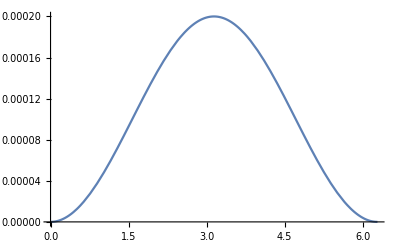

```mathematica
Plot[v10[t1,Pi-.0001]/.{bJ->1,bmu->1},{t1,0,2Pi}]
```

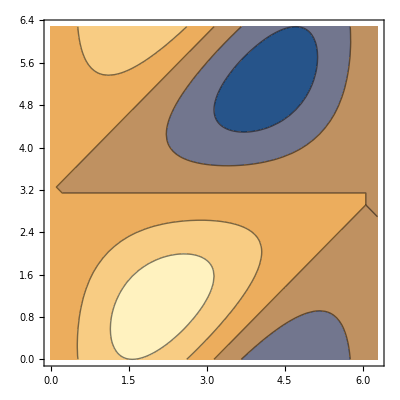

-Graphics-

```mathematica
ContourPlot[v10[t1,t2]/.{bJ->1,bmu->1},{t1,0,2Pi},{t2,0,2Pi}]
ContourPlot[v20[t1,t2]/.{bJ->1,bmu->1},{t1,0,2Pi},{t2,0,2Pi}]
```

## Poisson-equation approach, Series treatment

### Development of formulas

```mathematica
p[t1,t2,Ex,Ey]
```

ⅇ^(bJ Cos[t1-t2]-bmu (Ex Cos[t1]+Ey Sin[t1])-bmu (Ex Cos[t2]+Ey Sin[t2]))

```mathematica
TrigExpand[Cos[t2-t1]]
```

Cos[t1] Cos[t2]+Sin[t1] Sin[t2]

```mathematica
Table[((k/2) 2^(k/2)-1) ,{k,2,8,2}]
```

{1,7,23,63}

```mathematica
Clear[B]
A[n_,k_]:=If[EvenQ[k],(Gamma[(1+k)/2] Gamma[1/2 (1-k+n)])/(π Gamma[(n+2)/2]),0]
Aj[k_,j_]:=If[EvenQ[k],(Gamma[(1+k)/2] Gamma[(1+j)/2])/(π Gamma[(k+j+2)/2]),0]
B[n_,theta1_]:=Gamma[(n+1)/2]/Sqrt[Pi]/(n/2)!/;EvenQ[n]
```

```mathematica
CSInt[n_,k_]:=1/Pi Integrate[Cos[x]^k Sin[x]^(n-k),{x,0,Pi}]
CSIntj[k_,j_]:=1/Pi Integrate[Cos[x]^k Sin[x]^j,{x,0,Pi}]
```

```mathematica
kk=5;
Table[{kk,j,Aj[kk,j],CSIntj[kk,j]},{j,0,10}]//TableForm
```

5 | 0 | 0 | 0
5 | 1 | 0 | 0
5 | 2 | 0 | 0
5 | 3 | 0 | 0
5 | 4 | 0 | 0
5 | 5 | 0 | 0
5 | 6 | 0 | 0
5 | 7 | 0 | 0
5 | 8 | 0 | 0
5 | 9 | 0 | 0
5 | 10 | 0 | 0

```mathematica
nn=11;
Table[{nn,k,A[nn,k],CSInt[nn,k]},{k,0,nn}]//TableForm
```

11 | 0 | 512/(693 π) | 512/(693 π)
11 | 1 | 0 | 0
11 | 2 | 256/(3465 π) | 256/(3465 π)
11 | 3 | 0 | 0
11 | 4 | 32/(1155 π) | 32/(1155 π)
11 | 5 | 0 | 0
11 | 6 | 16/(693 π) | 16/(693 π)
11 | 7 | 0 | 0
11 | 8 | 4/(99 π) | 4/(99 π)
11 | 9 | 0 | 0
11 | 10 | 2/(11 π) | 2/(11 π)
11 | 11 | 0 | 0

```mathematica
Table[Limit[2^(2j-1)A[2j,k],k->2],{j,4,12}]
Table[(n)!/(n/2)!/((n/2)+1)!,{n,6,24,2}]
Table[Aguess[n,2],{n,6,24,2}]
```

{5,14,42,132,429,1430,4862,16796,58786}

{5,14,42,132,429,1430,4862,16796,58786,208012}

{5,14,42,132,429,1430,4862,16796,58786,208012}

```mathematica
Table[Limit[2^(2j-1)A[2j,k],k->4],{j,5,12}]
Table[6(n)!/(n/2)!/((n/2)+2)!,{n,6,24,2}]
Table[Aguess[n,4],{n,6,24,2}]
```

{6,14,36,99,286,858,2652,8398}

{6,14,36,99,286,858,2652,8398,27132,89148}

{6,14,36,99,286,858,2652,8398,27132,89148}

```mathematica
Table[Limit[2^(2j-1)A[2j,k],k->6],{j,6,12}]
Table[6 10(n)!/(n/2)!/((n/2)+3)!,{n,6,24,2}]
Table[Aguess[n,6],{n,6,24,2}]
```

{10,20,45,110,286,780,2210}

{10,20,45,110,286,780,2210,6460,19380,59432}

{10,20,45,110,286,780,2210,6460,19380,59432}

```mathematica
Table[Limit[2^(j-1)A[j,k],k->8],{j,14,28,2}]
Table[6 10 14(n)!/(n/2)!/((n/2)+4)!,{n,6,24,2}]
Table[Aguess[n,8],{n,6,24,2}]
```

{20,35,70,154,364,910,2380,6460}

{20,35,70,154,364,910,2380,6460,18088,52003}

{20,35,70,154,364,910,2380,6460,18088,52003}

```mathematica
Table[Limit[2^(2j-1)A[2j,k],k->10],{j,8,14}]
Table[6 10 14 18(n)!/(n/2)!/((n/2)+5)!,{n,6,24,2}]
Table[Aguess[n,10],{n,6,24,2}]
```

{45,70,126,252,546,1260,3060}

{45,70,126,252,546,1260,3060,7752,20349,55062}

{45,70,126,252,546,1260,3060,7752,20349,55062}

```mathematica
Table[Limit[2^(2j-1)A[2j,k],k->12],{j,9,14}]
Table[6 10 14 18 22(n)!/(n/2)!/((n/2)+6)!,{n,6,24,2}]
Table[Aguess[n,12],{n,6,24,2}]
```

{110,154,252,462,924,1980}

{110,154,252,462,924,1980,4488,10659,26334,67298}

{110,154,252,462,924,1980,4488,10659,26334,67298}

```mathematica
Table[Limit[2^(2j-1)A[2j,k],k->14],{j,10,18}]
Table[6 10 14 18 22 26(n)!/(n/2)!/((n/2)+7)!,{n,6,24,2}]
Table[Aguess[n,14],{n,6,24,2}]
```

{286,364,546,924,1716,3432,7293,16302,38038}

{286,364,546,924,1716,3432,7293,16302,38038,92092}

{286,364,546,924,1716,3432,7293,16302,38038,92092}

```mathematica
Table[Limit[2^(2j-1)A[2j,k],k->16],{j,11,19}]
Table[6 10 14 18 22 26 30(n)!/(n/2)!/((n/2)+8)!,{n,6,24,2}]
Table[Aguess[n,16],{n,6,24,2}]
```

{780,910,1260,1980,3432,6435,12870,27170,60060}

{780,910,1260,1980,3432,6435,12870,27170,60060,138138}

{780,910,1260,1980,3432,6435,12870,27170,60060,138138}

```mathematica
Table[{B[n,theta1],Sum[Binomial[n,k]Cos[theta1]^k Sin[theta1]^(n-k)A[n,k]/.theta1->0,{k,0,n}]},{n,0,12,1}]//N//TableForm
```

1. | 1.
0.63662 | 0.
0.5 | 0.5
0.424413 | 0.
0.375 | 0.375
0.339531 | 0.
0.3125 | 0.3125
0.291026 | 0.
0.273438 | 0.273438
0.25869 | 0.
0.246094 | 0.246094
0.235173 | 0.
0.225586 | 0.225586

```mathematica
Table[{n,(*2^(2n)(2n+1)*)Sum[Binomial[n,k]Cos[theta1]^(k+1) Sin[theta1]^(n-k)A[n,k],{k,0,n,2}]},{n,1,11,1}]//Simplify//TableForm
```

1 | Sin[2 theta1]/π
2 | Cos[theta1]/2
3 | (10 Sin[2 theta1]+Sin[4 theta1])/(12 π)
4 | (3 Cos[theta1])/8
5 | (175 Sin[2 theta1]+28 Sin[4 theta1]+3 Sin[6 theta1])/(240 π)
6 | (5 Cos[theta1])/16
7 | (1470 Sin[2 theta1]+294 Sin[4 theta1]+54 Sin[6 theta1]+5 Sin[8 theta1])/(2240 π)
8 | (35 Cos[theta1])/128
9 | (48510 Sin[2 theta1]+11088 Sin[4 theta1]+2673 Sin[6 theta1]+440 Sin[8 theta1]+35 Sin[10 theta1])/(80640 π)
10 | (63 Cos[theta1])/256
11 | (396396 Sin[2 theta1]+99099 Sin[4 theta1]+28314 Sin[6 theta1]+6292 Sin[8 theta1]+910 Sin[10 theta1]+63 Sin[12 theta1])/(709632 π)

```mathematica
Table[{n,2^n(*/Binomial[n+2,(n+1)/2+1]*) Sum[Binomial[n,k]Cos[theta1]^(k) Sin[theta1]^(n-k)A[n+1,k+1],{k,1,n,1}]},{n,1,11,2}]//Simplify//TableForm
```

1 | Cos[theta1]
3 | 3 Cos[theta1]
5 | 10 Cos[theta1]
7 | 35 Cos[theta1]
9 | 126 Cos[theta1]
11 | 462 Cos[theta1]

```mathematica
Table[{n, Sum[Binomial[n,k]Cos[theta1]^(k) Sin[theta1]^(n-k)A[n+1,k+1],{k,1,n,1}]},{n,0,12,2}]//Simplify//TableForm
```

0 | 0
2 | (4 Cos[theta1] Sin[theta1])/(3 π)
4 | (10 Sin[2 theta1]+Sin[4 theta1])/(15 π)
6 | (175 Sin[2 theta1]+28 Sin[4 theta1]+3 Sin[6 theta1])/(280 π)
8 | (1470 Sin[2 theta1]+294 Sin[4 theta1]+54 Sin[6 theta1]+5 Sin[8 theta1])/(2520 π)
10 | (48510 Sin[2 theta1]+11088 Sin[4 theta1]+2673 Sin[6 theta1]+440 Sin[8 theta1]+35 Sin[10 theta1])/(88704 π)
12 | (396396 Sin[2 theta1]+99099 Sin[4 theta1]+28314 Sin[6 theta1]+6292 Sin[8 theta1]+910 Sin[10 theta1]+63 Sin[12 theta1])/(768768 π)

```mathematica
Sum[x^n/n! B[n,t],{n,0,Infinity,2}]
```

$Aborted

```mathematica
Sum[x^(2m)/(2m)! Gamma[m+1/2]/Sqrt[Pi]/m!,{m,0,Infinity}]
```

BesselI[0,x]

```mathematica
TrigToExp[Sin[t2]]^k
Sum[Binomial[k,l1]Exp[I l1 t2]Exp[-I (k-l1)t2]/2^k Binomial[n-k,l2]Exp[I l2 t2](-1)^(n-k-l2)Exp[-I (n-k-l2) t2] ,{l1,0,k},{l2,0,n-k}]//HoldForm
```

(1/2 ⅈ ⅇ^(-ⅈ t2)-1/2 ⅈ ⅇ^(ⅈ t2))^k

∑_(l1=0)^k ∑_(l2=0)^(n-k) 1/2^k Binomial[k,l1] Exp[ⅈ l1 t2] Exp[-ⅈ (k-l1) t2] Binomial[n-k,l2] Exp[ⅈ l2 t2] (-1)^(n-k-l2) Exp[-ⅈ (n-k-l2) t2]

### cos(t1-t2)^j

```mathematica
j odd
```

j odd

```mathematica
Table[{j,(j-1)/2,Integrate[Cos[t1-t2]^j ,{t2,0,Pi}]},{j,1,15,2}]//Expand//TableForm
```

1 | 0 | 2 Sin[t1]
3 | 1 | (3 Sin[t1])/2+1/6 Sin[3 t1]
5 | 2 | (5 Sin[t1])/4+5/24 Sin[3 t1]+1/40 Sin[5 t1]
7 | 3 | (35 Sin[t1])/32+7/32 Sin[3 t1]+7/160 Sin[5 t1]+1/224 Sin[7 t1]
9 | 4 | (63 Sin[t1])/64+7/32 Sin[3 t1]+9/160 Sin[5 t1]+9/896 Sin[7 t1]+Sin[9 t1]/1152
11 | 5 | (231 Sin[t1])/256+55/256 Sin[3 t1]+33/512 Sin[5 t1]+(55 Sin[7 t1])/3584+(11 Sin[9 t1])/4608+Sin[11 t1]/5632
13 | 6 | (429 Sin[t1])/512+(429 Sin[3 t1])/2048+(143 Sin[5 t1])/2048+(143 Sin[7 t1])/7168+(13 Sin[9 t1])/3072+(13 Sin[11 t1])/22528+Sin[13 t1]/26624
15 | 7 | (6435 Sin[t1])/8192+(5005 Sin[3 t1])/24576+(3003 Sin[5 t1])/40960+(195 Sin[7 t1])/8192+(455 Sin[9 t1])/73728+(105 Sin[11 t1])/90112+(15 Sin[13 t1])/106496+Sin[15 t1]/122880

```mathematica
Table[{j,(j-1)/2,2^(2-j)Sum[1/l Binomial[j,(j+l)/2]Sin[l t1],{l,1,j,2}]},{j,1,15,2}]//Expand//TableForm
```

1 | 0 | 2 Sin[t1]
3 | 1 | (3 Sin[t1])/2+1/6 Sin[3 t1]
5 | 2 | (5 Sin[t1])/4+5/24 Sin[3 t1]+1/40 Sin[5 t1]
7 | 3 | (35 Sin[t1])/32+7/32 Sin[3 t1]+7/160 Sin[5 t1]+1/224 Sin[7 t1]
9 | 4 | (63 Sin[t1])/64+7/32 Sin[3 t1]+9/160 Sin[5 t1]+9/896 Sin[7 t1]+Sin[9 t1]/1152
11 | 5 | (231 Sin[t1])/256+55/256 Sin[3 t1]+33/512 Sin[5 t1]+(55 Sin[7 t1])/3584+(11 Sin[9 t1])/4608+Sin[11 t1]/5632
13 | 6 | (429 Sin[t1])/512+(429 Sin[3 t1])/2048+(143 Sin[5 t1])/2048+(143 Sin[7 t1])/7168+(13 Sin[9 t1])/3072+(13 Sin[11 t1])/22528+Sin[13 t1]/26624
15 | 7 | (6435 Sin[t1])/8192+(5005 Sin[3 t1])/24576+(3003 Sin[5 t1])/40960+(195 Sin[7 t1])/8192+(455 Sin[9 t1])/73728+(105 Sin[11 t1])/90112+(15 Sin[13 t1])/106496+Sin[15 t1]/122880

```mathematica
j even
```

even j

```mathematica
Table[{j,Gamma[(j+1)/2]Sqrt[Pi]/(j/2)!,Integrate[Cos[t1-t2]^j ,{t2,0,Pi}]},{j,0,14,2}]//Expand//TableForm
```

0 | π | π
2 | π/2 | π/2
4 | (3 π)/8 | (3 π)/8
6 | (5 π)/16 | (5 π)/16
8 | (35 π)/128 | (35 π)/128
10 | (63 π)/256 | (63 π)/256
12 | (231 π)/1024 | (231 π)/1024
14 | (429 π)/2048 | (429 π)/2048

```mathematica
nn=0;
Table[{j,(j-1)/2,Pi Binomial[j,(j+nn)/2]/2^j Cos[nn t1]},{j,0,20,2}]//Expand//TableForm
```

0 | -1/2 | π
2 | 1/2 | π/2
4 | 3/2 | (3 π)/8
6 | 5/2 | (5 π)/16
8 | 7/2 | (35 π)/128
10 | 9/2 | (63 π)/256
12 | 11/2 | (231 π)/1024
14 | 13/2 | (429 π)/2048
16 | 15/2 | (6435 π)/32768
18 | 17/2 | (12155 π)/65536
20 | 19/2 | (46189 π)/262144

### cos(t1-t2)^j cos(t2)

```mathematica
j even
```

even j

```mathematica
Table[{j,(j)/2, Integrate[Cos[t1-t2]^j Cos[t2],{t2,0,Pi}]},{j,2,20,2}]//Expand//TableForm
```

2 | 1 | 2/3 Sin[2 t1]
4 | 2 | 2/3 Sin[2 t1]+1/15 Sin[4 t1]
6 | 3 | 5/8 Sin[2 t1]+1/10 Sin[4 t1]+3/280 Sin[6 t1]
8 | 4 | 7/12 Sin[2 t1]+7/60 Sin[4 t1]+3/140 Sin[6 t1]+1/504 Sin[8 t1]
10 | 5 | 35/64 Sin[2 t1]+1/8 Sin[4 t1]+27/896 Sin[6 t1]+(5 Sin[8 t1])/1008+(5 Sin[10 t1])/12672
12 | 6 | 33/64 Sin[2 t1]+33/256 Sin[4 t1]+33/896 Sin[6 t1]+(11 Sin[8 t1])/1344+(5 Sin[10 t1])/4224+(3 Sin[12 t1])/36608
14 | 7 | (1001 Sin[2 t1])/2048+(1001 Sin[4 t1])/7680+(429 Sin[6 t1])/10240+(13 Sin[8 t1])/1152+(455 Sin[10 t1])/202752+(21 Sin[12 t1])/73216+(7 Sin[14 t1])/399360
16 | 8 | (715 Sin[2 t1])/1536+(1001 Sin[4 t1])/7680+(117 Sin[6 t1])/2560+(65 Sin[8 t1])/4608+(175 Sin[10 t1])/50688+(45 Sin[12 t1])/73216+(7 Sin[14 t1])/99840+Sin[16 t1]/261120
18 | 9 | (7293 Sin[2 t1])/16384+(663 Sin[4 t1])/5120+(1989 Sin[6 t1])/40960+(17 Sin[8 t1])/1024+(425 Sin[10 t1])/90112+(153 Sin[12 t1])/146432+(357 Sin[14 t1])/2129920+(3 Sin[16 t1])/174080+(9 Sin[18 t1])/10584064
20 | 10 | (20995 Sin[2 t1])/49152+(4199 Sin[4 t1])/32768+(2907 Sin[6 t1])/57344+(1615 Sin[8 t1])/86016+(1615 Sin[10 t1])/270336+(14535 Sin[12 t1])/9371648+(133 Sin[14 t1])/425984+(19 Sin[16 t1])/417792+(45 Sin[18 t1])/10584064+(5 Sin[20 t1])/26148864

```mathematica
Table[{j,(j)/2, 1/2^(j-2)Sum[el/(el+1)/(el-1)Binomial[j,(j+el)/2]Sin[el t1],{el,2,j,2}]},{j,2,20,2}]//Expand//TableForm
```

2 | 1 | 2/3 Sin[2 t1]
4 | 2 | 2/3 Sin[2 t1]+1/15 Sin[4 t1]
6 | 3 | 5/8 Sin[2 t1]+1/10 Sin[4 t1]+3/280 Sin[6 t1]
8 | 4 | 7/12 Sin[2 t1]+7/60 Sin[4 t1]+3/140 Sin[6 t1]+1/504 Sin[8 t1]
10 | 5 | 35/64 Sin[2 t1]+1/8 Sin[4 t1]+27/896 Sin[6 t1]+(5 Sin[8 t1])/1008+(5 Sin[10 t1])/12672
12 | 6 | 33/64 Sin[2 t1]+33/256 Sin[4 t1]+33/896 Sin[6 t1]+(11 Sin[8 t1])/1344+(5 Sin[10 t1])/4224+(3 Sin[12 t1])/36608
14 | 7 | (1001 Sin[2 t1])/2048+(1001 Sin[4 t1])/7680+(429 Sin[6 t1])/10240+(13 Sin[8 t1])/1152+(455 Sin[10 t1])/202752+(21 Sin[12 t1])/73216+(7 Sin[14 t1])/399360
16 | 8 | (715 Sin[2 t1])/1536+(1001 Sin[4 t1])/7680+(117 Sin[6 t1])/2560+(65 Sin[8 t1])/4608+(175 Sin[10 t1])/50688+(45 Sin[12 t1])/73216+(7 Sin[14 t1])/99840+Sin[16 t1]/261120
18 | 9 | (7293 Sin[2 t1])/16384+(663 Sin[4 t1])/5120+(1989 Sin[6 t1])/40960+(17 Sin[8 t1])/1024+(425 Sin[10 t1])/90112+(153 Sin[12 t1])/146432+(357 Sin[14 t1])/2129920+(3 Sin[16 t1])/174080+(9 Sin[18 t1])/10584064
20 | 10 | (20995 Sin[2 t1])/49152+(4199 Sin[4 t1])/32768+(2907 Sin[6 t1])/57344+(1615 Sin[8 t1])/86016+(1615 Sin[10 t1])/270336+(14535 Sin[12 t1])/9371648+(133 Sin[14 t1])/425984+(19 Sin[16 t1])/417792+(45 Sin[18 t1])/10584064+(5 Sin[20 t1])/26148864

```mathematica
(* work *)
Table[Binomial[2n,n+1]/2^(2n-3)/3,{n,1,15}] (*l=2*)
Table[Binomial[2n+2,n+3]/2^(2n-3)/5/6,{n,1,15}](*l=4*)
Table[Binomial[2n+4,n+5]/2^(2n-3)/7*3/80,{n,1,15}](*l=6*)
Table[Binomial[2n+6,n+7]/2^(2n-3)/9/112,{n,1,15}](*l=8*)
Table[Binomial[2n+8,n+9]/2^(2n-3)/11*5/2304,{n,1,10}](*l=10*)
Table[Binomial[2n+10,n+11]/2^(2n-3)/13*3/5632,{n,1,10}](*l=12*)
ll=8;
Table[Binomial[2n+ll-2,n+ll-1]/2^(2n-3)ll/(ll+1)/(ll-1)/2^(ll-1),{n,1,10}](*general l*)
```

{2/3,2/3,5/8,7/12,35/64,33/64,1001/2048,715/1536,7293/16384,20995/49152,323323/786432,52003/131072,2414425/6291456,780045/2097152,48474225/134217728}

{1/15,1/10,7/60,1/8,33/256,1001/7680,1001/7680,663/5120,4199/32768,24871/196608,81719/655360,96577/786432,2028117/16777216,3991995/33554432,1964315/16777216}

{3/280,3/140,27/896,33/896,429/10240,117/2560,1989/40960,2907/57344,95931/1835008,245157/4587520,3187041/58720256,460161/8388608,7413705/134217728,930465/16777216,104398173/1879048192}

{1/504,5/1008,11/1344,13/1152,65/4608,17/1024,1615/86016,3553/172032,81719/3670016,1562275/66060288,312455/12582912,216775/8388608,1344005/50331648,19332995/704643072,26363175/939524096}

{5/12672,5/4224,455/202752,175/50688,425/90112,1615/270336,11305/1572864,2185/262144,710125/75497472,261625/25165824}

{3/36608,21/73216,45/73216,153/146432,14535/9371648,3591/1703936,9177/3407872,1725/524288,65205/16777216,150075/33554432}

{1/504,5/1008,11/1344,13/1152,65/4608,17/1024,1615/86016,3553/172032,81719/3670016,1562275/66060288}

```mathematica
j odd
```

j odd

```mathematica
Table[{j,(j)/2, Integrate[Cos[t1-t2]^j Cos[t2],{t2,0,Pi}]},{j,1,20,2}]//Expand//TableForm
```

1 | 1/2 | 1/2 π Cos[t1]
3 | 3/2 | 3/8 π Cos[t1]
5 | 5/2 | 5/16 π Cos[t1]
7 | 7/2 | 35/128 π Cos[t1]
9 | 9/2 | 63/256 π Cos[t1]
11 | 11/2 | (231 π Cos[t1])/1024
13 | 13/2 | (429 π Cos[t1])/2048
15 | 15/2 | (6435 π Cos[t1])/32768
17 | 17/2 | (12155 π Cos[t1])/65536
19 | 19/2 | (46189 π Cos[t1])/262144

```mathematica
Table[{j,(j)/2, Pi Binomial[j,(j+1)/2]/2^j Cos[t1]},{j,1,20,2}]//Expand//TableForm
```

1 | 1/2 | 1/2 π Cos[t1]
3 | 3/2 | 3/8 π Cos[t1]
5 | 5/2 | 5/16 π Cos[t1]
7 | 7/2 | 35/128 π Cos[t1]
9 | 9/2 | 63/256 π Cos[t1]
11 | 11/2 | (231 π Cos[t1])/1024
13 | 13/2 | (429 π Cos[t1])/2048
15 | 15/2 | (6435 π Cos[t1])/32768
17 | 17/2 | (12155 π Cos[t1])/65536
19 | 19/2 | (46189 π Cos[t1])/262144

```mathematica
nn=1;
Table[{j,(j-1)/2,Pi Binomial[j,(j+nn)/2]/2^j Cos[nn t1]},{j,1,20,2}]//Expand//TableForm
```

1 | 0 | 1/2 π Cos[t1]
3 | 1 | 3/8 π Cos[t1]
5 | 2 | 5/16 π Cos[t1]
7 | 3 | 35/128 π Cos[t1]
9 | 4 | 63/256 π Cos[t1]
11 | 5 | (231 π Cos[t1])/1024
13 | 6 | (429 π Cos[t1])/2048
15 | 7 | (6435 π Cos[t1])/32768
17 | 8 | (12155 π Cos[t1])/65536
19 | 9 | (46189 π Cos[t1])/262144

### cos(t1-t2)^j cos(n t2)

```mathematica
j+n even
```

j+even n

```mathematica
(* j even, n = 2 even *)
Table[{j,(j)/2, Integrate[Cos[t1-t2]^j Cos[2t2],{t2,0,Pi}]},{j,2,20,2}]//Expand//TableForm
```

2 | 1 | 1/4 π Cos[2 t1]
4 | 2 | 1/4 π Cos[2 t1]
6 | 3 | 15/64 π Cos[2 t1]
8 | 4 | 7/32 π Cos[2 t1]
10 | 5 | 105/512 π Cos[2 t1]
12 | 6 | 99/512 π Cos[2 t1]
14 | 7 | (3003 π Cos[2 t1])/16384
16 | 8 | (715 π Cos[2 t1])/4096
18 | 9 | (21879 π Cos[2 t1])/131072
20 | 10 | (20995 π Cos[2 t1])/131072

```mathematica
nn=2;
Table[{j,(j-1)/2,Pi Binomial[j,(j+nn)/2]/2^j Cos[nn t1]},{j,2,20,2}]//Expand//TableForm
```

2 | 1/2 | 1/4 π Cos[2 t1]
4 | 3/2 | 1/4 π Cos[2 t1]
6 | 5/2 | 15/64 π Cos[2 t1]
8 | 7/2 | 7/32 π Cos[2 t1]
10 | 9/2 | 105/512 π Cos[2 t1]
12 | 11/2 | 99/512 π Cos[2 t1]
14 | 13/2 | (3003 π Cos[2 t1])/16384
16 | 15/2 | (715 π Cos[2 t1])/4096
18 | 17/2 | (21879 π Cos[2 t1])/131072
20 | 19/2 | (20995 π Cos[2 t1])/131072

```mathematica
(* j odd, n = 3 odd *)
Table[{j,(j)/2, Integrate[Cos[t1-t2]^j Cos[3t2],{t2,0,Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 1/2 | 0
3 | 3/2 | 1/8 π Cos[3 t1]
5 | 5/2 | 5/32 π Cos[3 t1]
7 | 7/2 | 21/128 π Cos[3 t1]
9 | 9/2 | 21/128 π Cos[3 t1]
11 | 11/2 | (165 π Cos[3 t1])/1024

```mathematica
nn=3;
Table[{j,(j-1)/2,Pi Binomial[j,(j+nn)/2]/2^j Cos[nn t1]},{j,1,20,2}]//Expand//TableForm
```

1 | 0 | 0
3 | 1 | 1/8 π Cos[3 t1]
5 | 2 | 5/32 π Cos[3 t1]
7 | 3 | 21/128 π Cos[3 t1]
9 | 4 | 21/128 π Cos[3 t1]
11 | 5 | (165 π Cos[3 t1])/1024
13 | 6 | (1287 π Cos[3 t1])/8192
15 | 7 | (5005 π Cos[3 t1])/32768
17 | 8 | (2431 π Cos[3 t1])/16384
19 | 9 | (37791 π Cos[3 t1])/262144

```mathematica
j+n odd
```

j+n odd

```mathematica
(* j even, n = 1 odd *)
Table[{j, Integrate[Cos[t1-t2]^j Cos[t2],{t2,0,Pi}]},{j,0,11,2}]//Expand//TableForm
```

0 | 0
2 | 2/3 Sin[2 t1]
4 | 2/3 Sin[2 t1]+1/15 Sin[4 t1]
6 | 5/8 Sin[2 t1]+1/10 Sin[4 t1]+3/280 Sin[6 t1]
8 | 7/12 Sin[2 t1]+7/60 Sin[4 t1]+3/140 Sin[6 t1]+1/504 Sin[8 t1]
10 | 35/64 Sin[2 t1]+1/8 Sin[4 t1]+27/896 Sin[6 t1]+(5 Sin[8 t1])/1008+(5 Sin[10 t1])/12672

```mathematica
nn=1;
Table[{j, 1/2^(j-2)Sum[el/(el-nn)/(el+nn)Binomial[j,(j+el)/2]Sin[el t1],{el,2,j,2}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0
2 | 2/3 Sin[2 t1]
4 | 2/3 Sin[2 t1]+1/15 Sin[4 t1]
6 | 5/8 Sin[2 t1]+1/10 Sin[4 t1]+3/280 Sin[6 t1]
8 | 7/12 Sin[2 t1]+7/60 Sin[4 t1]+3/140 Sin[6 t1]+1/504 Sin[8 t1]
10 | 35/64 Sin[2 t1]+1/8 Sin[4 t1]+27/896 Sin[6 t1]+(5 Sin[8 t1])/1008+(5 Sin[10 t1])/12672

```mathematica
(* j odd, n = 2 even *)
Table[{j,(j)/2, Integrate[Cos[t1-t2]^j Cos[2t2],{t2,0,Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 1/2 | -(2 Sin[t1])/3
3 | 3/2 | -Sin[t1]/2+3/10 Sin[3 t1]
5 | 5/2 | -(5 Sin[t1])/12+3/8 Sin[3 t1]+5/168 Sin[5 t1]
7 | 7/2 | -(35 Sin[t1])/96+63/160 Sin[3 t1]+5/96 Sin[5 t1]+(7 Sin[7 t1])/1440
9 | 9/2 | -(21 Sin[t1])/64+63/160 Sin[3 t1]+15/224 Sin[5 t1]+7/640 Sin[7 t1]+(9 Sin[9 t1])/9856
11 | 11/2 | -(77 Sin[t1])/256+99/256 Sin[3 t1]+(275 Sin[5 t1])/3584+(77 Sin[7 t1])/4608+(9 Sin[9 t1])/3584+(11 Sin[11 t1])/59904

```mathematica
(* j odd, n = 2 even *)Table[{j,(j)/2, 1/2^(j-2)Sum[el/(el-2)/(el+2)Binomial[j,(j+el)/2]Sin[el t1],{el,1,j,2}]},{j,1,11,2}]//Expand//TableForm
```

1 | 1/2 | -(2 Sin[t1])/3
3 | 3/2 | -Sin[t1]/2+3/10 Sin[3 t1]
5 | 5/2 | -(5 Sin[t1])/12+3/8 Sin[3 t1]+5/168 Sin[5 t1]
7 | 7/2 | -(35 Sin[t1])/96+63/160 Sin[3 t1]+5/96 Sin[5 t1]+(7 Sin[7 t1])/1440
9 | 9/2 | -(21 Sin[t1])/64+63/160 Sin[3 t1]+15/224 Sin[5 t1]+7/640 Sin[7 t1]+(9 Sin[9 t1])/9856
11 | 11/2 | -(77 Sin[t1])/256+99/256 Sin[3 t1]+(275 Sin[5 t1])/3584+(77 Sin[7 t1])/4608+(9 Sin[9 t1])/3584+(11 Sin[11 t1])/59904

```mathematica
(* j even, n = 3 odd *)
Table[{j,(j)/2, Integrate[Cos[t1-t2]^j Cos[3t2],{t2,0,Pi}]},{j,2,12,2}]//Expand//TableForm
```

2 | 1 | -2/5 Sin[2 t1]
4 | 2 | -2/5 Sin[2 t1]+1/7 Sin[4 t1]
6 | 3 | -3/8 Sin[2 t1]+3/14 Sin[4 t1]+1/72 Sin[6 t1]
8 | 4 | -7/20 Sin[2 t1]+1/4 Sin[4 t1]+1/36 Sin[6 t1]+1/440 Sin[8 t1]
10 | 5 | -21/64 Sin[2 t1]+15/56 Sin[4 t1]+5/128 Sin[6 t1]+1/176 Sin[8 t1]+(5 Sin[10 t1])/11648
12 | 6 | -99/320 Sin[2 t1]+(495 Sin[4 t1])/1792+(55 Sin[6 t1])/1152+3/320 Sin[8 t1]+(15 Sin[10 t1])/11648+Sin[12 t1]/11520

```mathematica
Table[{j,(j)/2, 1/2^(j-2)Sum[el/(el-3)/(el+3)Binomial[j,(j+el)/2]Sin[el t1],{el,2,j,2}]},{j,2,12,2}]//Expand//TableForm
```

2 | 1 | -2/5 Sin[2 t1]
4 | 2 | -2/5 Sin[2 t1]+1/7 Sin[4 t1]
6 | 3 | -3/8 Sin[2 t1]+3/14 Sin[4 t1]+1/72 Sin[6 t1]
8 | 4 | -7/20 Sin[2 t1]+1/4 Sin[4 t1]+1/36 Sin[6 t1]+1/440 Sin[8 t1]
10 | 5 | -21/64 Sin[2 t1]+15/56 Sin[4 t1]+5/128 Sin[6 t1]+1/176 Sin[8 t1]+(5 Sin[10 t1])/11648
12 | 6 | -99/320 Sin[2 t1]+(495 Sin[4 t1])/1792+(55 Sin[6 t1])/1152+3/320 Sin[8 t1]+(15 Sin[10 t1])/11648+Sin[12 t1]/11520

```mathematica
nn=5
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2],{t2,0,Pi}]},{j,0,11,2}]//TrigReduce//Expand//TableForm
```

5

0 | 0
2 | -2/21 Sin[2 t1]
4 | -2/21 Sin[2 t1]-1/9 Sin[4 t1]
6 | -5/56 Sin[2 t1]-1/6 Sin[4 t1]+3/88 Sin[6 t1]
8 | -1/12 Sin[2 t1]-7/36 Sin[4 t1]+3/44 Sin[6 t1]+1/312 Sin[8 t1]
10 | -5/64 Sin[2 t1]-5/24 Sin[4 t1]+(135 Sin[6 t1])/1408+5/624 Sin[8 t1]+Sin[10 t1]/1920

```mathematica
nn=5;
Table[{j, 1/2^(j-2)Sum[el/(el-nn)/(el+nn)Binomial[j,(j+el)/2]Sin[el t1],{el,2,j,2}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0
2 | -2/21 Sin[2 t1]
4 | -2/21 Sin[2 t1]-1/9 Sin[4 t1]
6 | -5/56 Sin[2 t1]-1/6 Sin[4 t1]+3/88 Sin[6 t1]
8 | -1/12 Sin[2 t1]-7/36 Sin[4 t1]+3/44 Sin[6 t1]+1/312 Sin[8 t1]
10 | -5/64 Sin[2 t1]-5/24 Sin[4 t1]+(135 Sin[6 t1])/1408+5/624 Sin[8 t1]+Sin[10 t1]/1920

```mathematica
nn=10
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2],{t2,0,Pi}]},{j,1,11,2}]//TrigReduce//Expand//TableForm
```

10

1 | -(2 Sin[t1])/99
3 | -Sin[t1]/66-3/182 Sin[3 t1]
5 | -(5 Sin[t1])/396-15/728 Sin[3 t1]-1/120 Sin[5 t1]
7 | -(35 Sin[t1])/3168-9/416 Sin[3 t1]-7/480 Sin[5 t1]-(7 Sin[7 t1])/1632
9 | -(7 Sin[t1])/704-9/416 Sin[3 t1]-3/160 Sin[5 t1]-(21 Sin[7 t1])/2176-(9 Sin[9 t1])/2432
11 | -(7 Sin[t1])/768-(495 Sin[3 t1])/23296-11/512 Sin[5 t1]-(385 Sin[7 t1])/26112-(99 Sin[9 t1])/9728+(11 Sin[11 t1])/10752

```mathematica
nn=10;
Table[{j, 1/2^(j-2)Sum[el/(el-nn)/(el+nn)Binomial[j,(j+el)/2]Sin[el t1],{el,1,j,2}]},{j,1,11,2}]//Expand//TableForm
```

1 | -(2 Sin[t1])/99
3 | -Sin[t1]/66-3/182 Sin[3 t1]
5 | -(5 Sin[t1])/396-15/728 Sin[3 t1]-1/120 Sin[5 t1]
7 | -(35 Sin[t1])/3168-9/416 Sin[3 t1]-7/480 Sin[5 t1]-(7 Sin[7 t1])/1632
9 | -(7 Sin[t1])/704-9/416 Sin[3 t1]-3/160 Sin[5 t1]-(21 Sin[7 t1])/2176-(9 Sin[9 t1])/2432
11 | -(7 Sin[t1])/768-(495 Sin[3 t1])/23296-11/512 Sin[5 t1]-(385 Sin[7 t1])/26112-(99 Sin[9 t1])/9728+(11 Sin[11 t1])/10752

### cos(t1-t2)^j cos(n t2) cos(t2)

```mathematica
j+n odd
```

j+n odd

```mathematica
nn=0;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 1/2 π Cos[t1]
3 | 3/8 π Cos[t1]
5 | 5/16 π Cos[t1]
7 | 35/128 π Cos[t1]
9 | 63/256 π Cos[t1]
11 | (231 π Cos[t1])/1024

```mathematica
nn=0;
Table[{j,Pi( Binomial[j,(j+nn-1)/2] Cos[(nn-1) t1]+Binomial[j,(j+nn+1)/2]Cos[(nn+1)t1])/2^(j+1)},{j,1,11,2}]//Expand//TableForm
```

1 | 1/2 π Cos[t1]
3 | 3/8 π Cos[t1]
5 | 5/16 π Cos[t1]
7 | 35/128 π Cos[t1]
9 | 63/256 π Cos[t1]
11 | (231 π Cos[t1])/1024

```mathematica
nn=1;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,0,11,2}]//Expand//TableForm
```

0 | π/2
2 | π/4+1/8 π Cos[2 t1]
4 | (3 π)/16+1/8 π Cos[2 t1]
6 | (5 π)/32+15/128 π Cos[2 t1]
8 | (35 π)/256+7/64 π Cos[2 t1]
10 | (63 π)/512+(105 π Cos[2 t1])/1024

```mathematica
nn=1;
Table[{j,Pi( Binomial[j,j/2] Cos[(nn-1) t1]+Binomial[j,j/2+1]Cos[(nn+1)t1])/2^(j+1)},{j,0,11,2}]//Expand//TableForm
```

0 | π/2
2 | π/4+1/8 π Cos[2 t1]
4 | (3 π)/16+1/8 π Cos[2 t1]
6 | (5 π)/32+15/128 π Cos[2 t1]
8 | (35 π)/256+7/64 π Cos[2 t1]
10 | (63 π)/512+(105 π Cos[2 t1])/1024

```mathematica
nn=2;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,1,11,2}]//TrigReduce//Expand//TableForm
```

1 | 1/4 π Cos[t1]
3 | 3/16 π Cos[t1]+1/16 π Cos[3 t1]
5 | 5/32 π Cos[t1]+5/64 π Cos[3 t1]
7 | 35/256 π Cos[t1]+21/256 π Cos[3 t1]
9 | 63/512 π Cos[t1]+21/256 π Cos[3 t1]
11 | (231 π Cos[t1])/2048+(165 π Cos[3 t1])/2048

```mathematica
nn=2;
Table[{j,Pi( Binomial[j,j/2+1/2] Cos[(nn-1) t1]+Binomial[j,j/2+3/2]Cos[(nn+1)t1])/2^(j+1)},{j,1,11,2}]//Expand//TableForm
```

1 | 1/4 π Cos[t1]
3 | 3/16 π Cos[t1]+1/16 π Cos[3 t1]
5 | 5/32 π Cos[t1]+5/64 π Cos[3 t1]
7 | 35/256 π Cos[t1]+21/256 π Cos[3 t1]
9 | 63/512 π Cos[t1]+21/256 π Cos[3 t1]
11 | (231 π Cos[t1])/2048+(165 π Cos[3 t1])/2048

```mathematica
nn=3;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,0,11,2}]//TrigReduce//Expand//TableForm
```

0 | 0
2 | 1/8 π Cos[2 t1]
4 | 1/8 π Cos[2 t1]+1/32 π Cos[4 t1]
6 | 15/128 π Cos[2 t1]+3/64 π Cos[4 t1]
8 | 7/64 π Cos[2 t1]+7/128 π Cos[4 t1]
10 | (105 π Cos[2 t1])/1024+15/256 π Cos[4 t1]

```mathematica
nn=3;
Table[{j,Pi( Binomial[j,j/2+(nn-1)/2] Cos[(nn-1) t1]+Binomial[j,j/2+(nn+1)/2]Cos[(nn+1)t1])/2^(j+1)},{j,0,11,2}]//Expand//TableForm
```

0 | 0
2 | 1/8 π Cos[2 t1]
4 | 1/8 π Cos[2 t1]+1/32 π Cos[4 t1]
6 | 15/128 π Cos[2 t1]+3/64 π Cos[4 t1]
8 | 7/64 π Cos[2 t1]+7/128 π Cos[4 t1]
10 | (105 π Cos[2 t1])/1024+15/256 π Cos[4 t1]

```mathematica
nn=4;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,1,11,2}]//TrigReduce//Expand//TableForm
```

1 | 0
3 | 1/16 π Cos[3 t1]
5 | 5/64 π Cos[3 t1]+1/64 π Cos[5 t1]
7 | 21/256 π Cos[3 t1]+7/256 π Cos[5 t1]
9 | 21/256 π Cos[3 t1]+9/256 π Cos[5 t1]
11 | (165 π Cos[3 t1])/2048+(165 π Cos[5 t1])/4096

```mathematica
nn=4;
Table[{j,Pi( Binomial[j,j/2+(nn-1)/2] Cos[(nn-1) t1]+Binomial[j,j/2+(nn+1)/2]Cos[(nn+1)t1])/2^(j+1)},{j,1,11,2}]//Expand//TableForm
```

1 | 0
3 | 1/16 π Cos[3 t1]
5 | 5/64 π Cos[3 t1]+1/64 π Cos[5 t1]
7 | 21/256 π Cos[3 t1]+7/256 π Cos[5 t1]
9 | 21/256 π Cos[3 t1]+9/256 π Cos[5 t1]
11 | (165 π Cos[3 t1])/2048+(165 π Cos[5 t1])/4096

```mathematica
nn=5;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,0,20,2}]//TrigReduce//Expand//TableForm
```

0 | 0
2 | 0
4 | 1/32 π Cos[4 t1]
6 | 3/64 π Cos[4 t1]+1/128 π Cos[6 t1]
8 | 7/128 π Cos[4 t1]+1/64 π Cos[6 t1]
10 | 15/256 π Cos[4 t1]+(45 π Cos[6 t1])/2048
12 | (495 π Cos[4 t1])/8192+(55 π Cos[6 t1])/2048
14 | (1001 π Cos[4 t1])/16384+(1001 π Cos[6 t1])/32768
16 | (1001 π Cos[4 t1])/16384+(273 π Cos[6 t1])/8192
18 | (1989 π Cos[4 t1])/32768+(4641 π Cos[6 t1])/131072
20 | (62985 π Cos[4 t1])/1048576+(4845 π Cos[6 t1])/131072

```mathematica
nn=5;
Table[{j,Pi( Binomial[j,j/2+(nn-1)/2] Cos[(nn-1) t1]+Binomial[j,j/2+(nn+1)/2]Cos[(nn+1)t1])/2^(j+1)},{j,0,20,2}]//Expand//TableForm
```

0 | 0
2 | 0
4 | 1/32 π Cos[4 t1]
6 | 3/64 π Cos[4 t1]+1/128 π Cos[6 t1]
8 | 7/128 π Cos[4 t1]+1/64 π Cos[6 t1]
10 | 15/256 π Cos[4 t1]+(45 π Cos[6 t1])/2048
12 | (495 π Cos[4 t1])/8192+(55 π Cos[6 t1])/2048
14 | (1001 π Cos[4 t1])/16384+(1001 π Cos[6 t1])/32768
16 | (1001 π Cos[4 t1])/16384+(273 π Cos[6 t1])/8192
18 | (1989 π Cos[4 t1])/32768+(4641 π Cos[6 t1])/131072
20 | (62985 π Cos[4 t1])/1048576+(4845 π Cos[6 t1])/131072

```mathematica
nn=6;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,1,20,2}]//TrigReduce//Expand//TableForm
```

1 | 0
3 | 0
5 | 1/64 π Cos[5 t1]
7 | 7/256 π Cos[5 t1]+1/256 π Cos[7 t1]
9 | 9/256 π Cos[5 t1]+(9 π Cos[7 t1])/1024
11 | (165 π Cos[5 t1])/4096+(55 π Cos[7 t1])/4096
13 | (715 π Cos[5 t1])/16384+(143 π Cos[7 t1])/8192
15 | (3003 π Cos[5 t1])/65536+(1365 π Cos[7 t1])/65536
17 | (1547 π Cos[5 t1])/32768+(1547 π Cos[7 t1])/65536
19 | (12597 π Cos[5 t1])/262144+(6783 π Cos[7 t1])/262144

```mathematica
nn=7;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,0,20,2}]//TrigReduce//Expand//TableForm
```

0 | 0
2 | 0
4 | 0
6 | 1/128 π Cos[6 t1]
8 | 1/64 π Cos[6 t1]+1/512 π Cos[8 t1]
10 | (45 π Cos[6 t1])/2048+(5 π Cos[8 t1])/1024
12 | (55 π Cos[6 t1])/2048+(33 π Cos[8 t1])/4096
14 | (1001 π Cos[6 t1])/32768+(91 π Cos[8 t1])/8192
16 | (273 π Cos[6 t1])/8192+(455 π Cos[8 t1])/32768
18 | (4641 π Cos[6 t1])/131072+(1071 π Cos[8 t1])/65536
20 | (4845 π Cos[6 t1])/131072+(4845 π Cos[8 t1])/262144

```mathematica
nn=7;
Table[{j,Pi( Binomial[j,(j+nn-1)/2] Cos[(nn-1) t1]+Binomial[j,(j+nn+1)/2]Cos[(nn+1)t1])/2^(j+1)},{j,0,20,2}]//Expand//TableForm
```

0 | 0
2 | 0
4 | 0
6 | 1/128 π Cos[6 t1]
8 | 1/64 π Cos[6 t1]+1/512 π Cos[8 t1]
10 | (45 π Cos[6 t1])/2048+(5 π Cos[8 t1])/1024
12 | (55 π Cos[6 t1])/2048+(33 π Cos[8 t1])/4096
14 | (1001 π Cos[6 t1])/32768+(91 π Cos[8 t1])/8192
16 | (273 π Cos[6 t1])/8192+(455 π Cos[8 t1])/32768
18 | (4641 π Cos[6 t1])/131072+(1071 π Cos[8 t1])/65536
20 | (4845 π Cos[6 t1])/131072+(4845 π Cos[8 t1])/262144

```mathematica
nn=8;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,1,20,2}]//TrigReduce//Expand//TableForm
```

1 | 0
3 | 0
5 | 0
7 | 1/256 π Cos[7 t1]
9 | (9 π Cos[7 t1])/1024+(π Cos[9 t1])/1024
11 | (55 π Cos[7 t1])/4096+(11 π Cos[9 t1])/4096
13 | (143 π Cos[7 t1])/8192+(39 π Cos[9 t1])/8192
15 | (1365 π Cos[7 t1])/65536+(455 π Cos[9 t1])/65536
17 | (1547 π Cos[7 t1])/65536+(595 π Cos[9 t1])/65536
19 | (6783 π Cos[7 t1])/262144+(2907 π Cos[9 t1])/262144

```mathematica
nn=8;
Table[{j,Pi( Binomial[j,(j+nn-1)/2] Cos[(nn-1) t1]+Binomial[j,(j+nn+1)/2]Cos[(nn+1)t1])/2^(j+1)},{j,1,20,2}]//Expand//TableForm
```

1 | 0
3 | 0
5 | 0
7 | 1/256 π Cos[7 t1]
9 | (9 π Cos[7 t1])/1024+(π Cos[9 t1])/1024
11 | (55 π Cos[7 t1])/4096+(11 π Cos[9 t1])/4096
13 | (143 π Cos[7 t1])/8192+(39 π Cos[9 t1])/8192
15 | (1365 π Cos[7 t1])/65536+(455 π Cos[9 t1])/65536
17 | (1547 π Cos[7 t1])/65536+(595 π Cos[9 t1])/65536
19 | (6783 π Cos[7 t1])/262144+(2907 π Cos[9 t1])/262144

```mathematica
j+n even
```

j+even n

```mathematica
nn=1;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | (2 Sin[t1])/3
3 | Sin[t1]/2+7/30 Sin[3 t1]
5 | (5 Sin[t1])/12+7/24 Sin[3 t1]+23/840 Sin[5 t1]
7 | (35 Sin[t1])/96+49/160 Sin[3 t1]+23/480 Sin[5 t1]+(47 Sin[7 t1])/10080
9 | (21 Sin[t1])/64+49/160 Sin[3 t1]+(69 Sin[5 t1])/1120+(47 Sin[7 t1])/4480+(79 Sin[9 t1])/88704
11 | (77 Sin[t1])/256+77/256 Sin[3 t1]+(253 Sin[5 t1])/3584+(517 Sin[7 t1])/32256+(79 Sin[9 t1])/32256+(119 Sin[11 t1])/658944

```mathematica
Table[{j, 1/2^(j-2)Sum[(*el/(el-nn+1)/(el+nn+1)*)Binomial[j,(j+el)/2]Sin[el t1],{el,1,j,2}]},{j,1,11,2}]//Expand//TableForm
```

1 | 2 Sin[t1]
3 | (3 Sin[t1])/2+1/2 Sin[3 t1]
5 | (5 Sin[t1])/4+5/8 Sin[3 t1]+1/8 Sin[5 t1]
7 | (35 Sin[t1])/32+21/32 Sin[3 t1]+7/32 Sin[5 t1]+1/32 Sin[7 t1]
9 | (63 Sin[t1])/64+21/32 Sin[3 t1]+9/32 Sin[5 t1]+9/128 Sin[7 t1]+1/128 Sin[9 t1]
11 | (231 Sin[t1])/256+165/256 Sin[3 t1]+165/512 Sin[5 t1]+55/512 Sin[7 t1]+11/512 Sin[9 t1]+1/512 Sin[11 t1]

```mathematica
nn=2;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,2,12,2}]//Expand//TableForm
```

2 | 2/15 Sin[2 t1]
4 | 2/15 Sin[2 t1]+11/105 Sin[4 t1]
6 | 1/8 Sin[2 t1]+11/70 Sin[4 t1]+(31 Sin[6 t1])/2520
8 | 7/60 Sin[2 t1]+11/60 Sin[4 t1]+(31 Sin[6 t1])/1260+(59 Sin[8 t1])/27720
10 | 7/64 Sin[2 t1]+11/56 Sin[4 t1]+31/896 Sin[6 t1]+(59 Sin[8 t1])/11088+(475 Sin[10 t1])/1153152
12 | 33/320 Sin[2 t1]+(363 Sin[4 t1])/1792+(341 Sin[6 t1])/8064+(59 Sin[8 t1])/6720+(475 Sin[10 t1])/384384+(139 Sin[12 t1])/1647360

```mathematica
Table[{j, 1/2^(j-2)Sum[(*el/(el-nn+1)/(el+nn+1)*)Binomial[j,(j+el)/2]Sin[el t1],{el,2,j,2}]},{j,2,12,2}]//Expand//TableForm
```

2 | Sin[2 t1]
4 | Sin[2 t1]+1/4 Sin[4 t1]
6 | 15/16 Sin[2 t1]+3/8 Sin[4 t1]+1/16 Sin[6 t1]
8 | 7/8 Sin[2 t1]+7/16 Sin[4 t1]+1/8 Sin[6 t1]+1/64 Sin[8 t1]
10 | 105/128 Sin[2 t1]+15/32 Sin[4 t1]+45/256 Sin[6 t1]+5/128 Sin[8 t1]+1/256 Sin[10 t1]
12 | 99/128 Sin[2 t1]+(495 Sin[4 t1])/1024+55/256 Sin[6 t1]+33/512 Sin[8 t1]+3/256 Sin[10 t1]+Sin[12 t1]/1024

```mathematica
SinList[x_,n_]:=Simplify[Table[Coefficient[x,Sin[j t1]],{j,n}]]
```

```mathematica
nn=1;
Table[{j, Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,Pi}]},{j,1,11,2}]//Expand//TableForm
```

Fix j, variable n

```mathematica
jj=1;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m+1) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[EvenQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2
```

-(2 Sin[t1])/(-3+4 m+4 m^2)

{-2/(-3+4 m+4 m^2)}

{2}

{-1/(-3+4 m+4 m^2)}

```mathematica
jj=2;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[OddQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2
```

-(2 (-3 Sin[2 t1]+4 m^2 Sin[2 t1]))/(9-40 m^2+16 m^4)

{0,(6-8 m^2)/(9-40 m^2+16 m^4)}

{0,1}

{Indeterminate,(6-8 m^2)/(9-40 m^2+16 m^4)}

```mathematica
jj=3;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m+1) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[EvenQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2//Simplify
```

-(3 (-15 Sin[t1]+4 m Sin[t1]+4 m^2 Sin[t1]-7 Sin[3 t1]+4 m Sin[3 t1]+4 m^2 Sin[3 t1]))/(2 (45-72 m-56 m^2+32 m^3+16 m^4))

{3/(6-8 m-8 m^2),0,-(3 (-7+4 m+4 m^2))/(2 (45-72 m-56 m^2+32 m^3+16 m^4))}

{3/2,0,1/2}

{1/(3-4 m-4 m^2),Indeterminate,-(3 (-7+4 m+4 m^2))/(45-72 m-56 m^2+32 m^3+16 m^4)}

```mathematica
jj=4;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[OddQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2//Simplify
```

(-150 Sin[2 t1]+224 m^2 Sin[2 t1]-32 m^4 Sin[2 t1]-15 Sin[4 t1]+64 m^2 Sin[4 t1]-16 m^4 Sin[4 t1])/(-225+1036 m^2-560 m^4+64 m^6)

{0,(6-8 m^2)/(9-40 m^2+16 m^4),0,(15-4 m^2)/(225-136 m^2+16 m^4)}

{0,1,0,1/4}

{Indeterminate,(6-8 m^2)/(9-40 m^2+16 m^4),Indeterminate,(60-16 m^2)/(225-136 m^2+16 m^4)}

```mathematica
jj=5;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m+1) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[EvenQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2//Simplify
```

{-5/(4 (-3+4 m+4 m^2)),0,-(15 (-7+4 m+4 m^2))/(8 (-3+2 m) (-1+2 m) (3+2 m) (5+2 m)),0,-(5 (-23+4 m+4 m^2))/(8 (-5+2 m) (-3+2 m) (5+2 m) (7+2 m))}

{5/4,0,5/8,0,1/8}

{1/(3-4 m-4 m^2),Indeterminate,-(3 (-7+4 m+4 m^2))/(45-72 m-56 m^2+32 m^3+16 m^4),Indeterminate,-(5 (-23+4 m+4 m^2))/((-5+2 m) (-3+2 m) (5+2 m) (7+2 m))}

```mathematica
jj=6;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[OddQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2//Simplify
```

-((3 (-18375 Sin[2 t1]+28940 m^2 Sin[2 t1]-6160 m^4 Sin[2 t1]+320 m^6 Sin[2 t1]-2940 Sin[4 t1]+12784 m^2 Sin[4 t1]-4160 m^4 Sin[4 t1]+256 m^6 Sin[4 t1]-315 Sin[6 t1]+1436 m^2 Sin[6 t1]-720 m^4 Sin[6 t1]+64 m^6 Sin[6 t1]))/(8 (11025-51664 m^2+31584 m^4-5376 m^6+256 m^8)))

{0,(45-60 m^2)/(72-320 m^2+128 m^4),0,(45-12 m^2)/(450-272 m^2+32 m^4),0,(105-12 m^2)/(9800-2368 m^2+128 m^4)}

{0,15/16,0,3/8,0,1/16}

{Indeterminate,(6-8 m^2)/(9-40 m^2+16 m^4),Indeterminate,(60-16 m^2)/(225-136 m^2+16 m^4),Indeterminate,(210-24 m^2)/(1225-296 m^2+16 m^4)}

```mathematica
jj=7;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m+1) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[EvenQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2//Simplify
```

{-35/(32 (-3+4 m+4 m^2)),0,-(63 (-7+4 m+4 m^2))/(32 (-3+2 m) (-1+2 m) (3+2 m) (5+2 m)),0,-(35 (-23+4 m+4 m^2))/(32 (-5+2 m) (-3+2 m) (5+2 m) (7+2 m)),0,-(7 (-47+4 m+4 m^2))/(32 (-7+2 m) (-5+2 m) (7+2 m) (9+2 m))}

{35/32,0,21/32,0,7/32,0,1/32}

{1/(3-4 m-4 m^2),Indeterminate,-(3 (-7+4 m+4 m^2))/(45-72 m-56 m^2+32 m^3+16 m^4),Indeterminate,-(5 (-23+4 m+4 m^2))/((-5+2 m) (-3+2 m) (5+2 m) (7+2 m)),Indeterminate,-(7 (-47+4 m+4 m^2))/((-7+2 m) (-5+2 m) (7+2 m) (9+2 m))}

```mathematica
jj=8;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[OddQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2//Simplify
```

{0,(21-28 m^2)/(36-160 m^2+64 m^4),0,(105-28 m^2)/(900-544 m^2+64 m^4),0,(105-12 m^2)/(4900-1184 m^2+64 m^4),0,(63-4 m^2)/(31752-4160 m^2+128 m^4)}

{0,7/8,0,7/16,0,1/8,0,1/64}

{Indeterminate,(6-8 m^2)/(9-40 m^2+16 m^4),Indeterminate,(60-16 m^2)/(225-136 m^2+16 m^4),Indeterminate,(210-24 m^2)/(1225-296 m^2+16 m^4),Indeterminate,(504-32 m^2)/(3969-520 m^2+16 m^4)}

```mathematica
jj=9;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m+1) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[EvenQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2//Simplify
```

{-63/(64 (-3+4 m+4 m^2)),0,-(63 (-7+4 m+4 m^2))/(32 (-3+2 m) (-1+2 m) (3+2 m) (5+2 m)),0,-(45 (-23+4 m+4 m^2))/(32 (-5+2 m) (-3+2 m) (5+2 m) (7+2 m)),0,-(63 (-47+4 m+4 m^2))/(128 (-7+2 m) (-5+2 m) (7+2 m) (9+2 m)),0,-(9 (-79+4 m+4 m^2))/(128 (-9+2 m) (-7+2 m) (9+2 m) (11+2 m))}

{63/64,0,21/32,0,9/32,0,9/128,0,1/128}

{1/(3-4 m-4 m^2),Indeterminate,-(3 (-7+4 m+4 m^2))/(45-72 m-56 m^2+32 m^3+16 m^4),Indeterminate,-(5 (-23+4 m+4 m^2))/((-5+2 m) (-3+2 m) (5+2 m) (7+2 m)),Indeterminate,-(7 (-47+4 m+4 m^2))/((-7+2 m) (-5+2 m) (7+2 m) (9+2 m)),Indeterminate,-(9 (-79+4 m+4 m^2))/((-9+2 m) (-7+2 m) (9+2 m) (11+2 m))}

```mathematica
Factor[3-4 m-4 m^2]
Factor[45-72 m-56 m^2+32 m^3+16 m^4]
Factor[(-5+2 m) (-3+2 m) (5+2 m) (7+2 m)]
Factor[(-7+2 m) (-5+2 m) (7+2 m) (9+2 m)]
Factor[(-9+2 m) (-7+2 m) (9+2 m) (11+2 m)]
```

-(-1+2 m) (3+2 m)

(-3+2 m) (-1+2 m) (3+2 m) (5+2 m)

(-5+2 m) (-3+2 m) (5+2 m) (7+2 m)

(-7+2 m) (-5+2 m) (7+2 m) (9+2 m)

(-9+2 m) (-7+2 m) (9+2 m) (11+2 m)

```mathematica
Factor[{3-4 m-4 m^2,45-72 m-56 m^2+32 m^3+16 m^4,(-5+2 m) (-3+2 m) (5+2 m) (7+2 m),(-7+2 m) (-5+2 m) (7+2 m) (9+2 m),(-9+2 m) (-7+2 m) (9+2 m) (11+2 m)}]/.{m->(n-1)/2}//TableForm
```

-(-2+n) (2+n)
(-4+n) (-2+n) (2+n) (4+n)
(-6+n) (-4+n) (4+n) (6+n)
(-8+n) (-6+n) (6+n) (8+n)
(-10+n) (-8+n) (8+n) (10+n)

```mathematica
-el(n^2-el^2+1)/(n+el+1)/(n+el-1)/(n-el+1)/(n-el-1)/.{el->4}
```

-(4 (-15+n^2))/((-5+n) (-3+n) (3+n) (5+n))

```mathematica
Factor[{1, (-7+4 m+4 m^2), (-23+4 m+4 m^2),(-47+4 m+4 m^2),(-79+4 m+4 m^2)}/.{m->(n-1)/2}]
```

{1,-8+n^2,-24+n^2,-48+n^2,-80+n^2}

```mathematica
4 l2(l2+1)/.{l2->(l-1)/2}//Simplify
```

-1+l^2

```mathematica
(* 4 el(el+1) *)
```

```mathematica
Factor[9-40 m^2+16 m^4]
Factor[225-136 m^2+16 m^4]
Factor[1225-296 m^2+16 m^4]
Factor[3969-520 m^2+16 m^4]
```

(-3+2 m) (-1+2 m) (1+2 m) (3+2 m)

(-5+2 m) (-3+2 m) (3+2 m) (5+2 m)

(-7+2 m) (-5+2 m) (5+2 m) (7+2 m)

(-9+2 m) (-7+2 m) (7+2 m) (9+2 m)

```mathematica
Factor[{6-8 m^2,60-16 m^2,210-24 m^2,504-32 m^2}/.{m->n/2}]
```

{-2 (-3+n^2),-4 (-15+n^2),-6 (-35+n^2),-8 (-63+n^2)}

```mathematica
(* 4 el^2 - 1 + n^2 *)
```

### cos(t1-t2)^j cos(n t2) cos(t2)^2

```mathematica
j+n even
```

j+even n

```mathematica
jj=0; n = 2;
Simplify[Integrate[Cos[t1-t2]^jj Cos[2 t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[OddQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2//Simplify
```

π/4

{}

{}

{}

```mathematica
For[jj=0,jj<11,jj++,
entry[jj]=Table[{jj,n,Simplify[2^(jj+2)/Pi Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,Mod[jj,2],20,2}];
Print[TableForm[entry[jj]]]
]
```

0 | 0 | 2
0 | 2 | 1
0 | 4 | 0
0 | 6 | 0
0 | 8 | 0
0 | 10 | 0
0 | 12 | 0
0 | 14 | 0
0 | 16 | 0
0 | 18 | 0
0 | 20 | 0

1 | 1 | 3 Cos[t1]
1 | 3 | Cos[t1]
1 | 5 | 0
1 | 7 | 0
1 | 9 | 0
1 | 11 | 0
1 | 13 | 0
1 | 15 | 0
1 | 17 | 0
1 | 19 | 0

2 | 0 | 2 (2+Cos[2 t1])
2 | 2 | 2 (1+Cos[2 t1])
2 | 4 | Cos[2 t1]
2 | 6 | 0
2 | 8 | 0
2 | 10 | 0
2 | 12 | 0
2 | 14 | 0
2 | 16 | 0
2 | 18 | 0
2 | 20 | 0

3 | 1 | 9 Cos[t1]+Cos[3 t1]
3 | 3 | 3 Cos[t1]+2 Cos[3 t1]
3 | 5 | Cos[3 t1]
3 | 7 | 0
3 | 9 | 0
3 | 11 | 0
3 | 13 | 0
3 | 15 | 0
3 | 17 | 0
3 | 19 | 0

4 | 0 | 4 (3+2 Cos[2 t1])
4 | 2 | 6+8 Cos[2 t1]+Cos[4 t1]
4 | 4 | 2 (2 Cos[2 t1]+Cos[4 t1])
4 | 6 | Cos[4 t1]
4 | 8 | 0
4 | 10 | 0
4 | 12 | 0
4 | 14 | 0
4 | 16 | 0
4 | 18 | 0
4 | 20 | 0

5 | 1 | 5 (6 Cos[t1]+Cos[3 t1])
5 | 3 | 10 Cos[t1]+10 Cos[3 t1]+Cos[5 t1]
5 | 5 | 5 Cos[3 t1]+2 Cos[5 t1]
5 | 7 | Cos[5 t1]
5 | 9 | 0
5 | 11 | 0
5 | 13 | 0
5 | 15 | 0
5 | 17 | 0
5 | 19 | 0

6 | 0 | 10 (4+3 Cos[2 t1])
6 | 2 | 2 (10+15 Cos[2 t1]+3 Cos[4 t1])
6 | 4 | 15 Cos[2 t1]+12 Cos[4 t1]+Cos[6 t1]
6 | 6 | 2 (3 Cos[4 t1]+Cos[6 t1])
6 | 8 | Cos[6 t1]
6 | 10 | 0
6 | 12 | 0
6 | 14 | 0
6 | 16 | 0
6 | 18 | 0
6 | 20 | 0

7 | 1 | 21 (5 Cos[t1]+Cos[3 t1])
7 | 3 | 7 (5 Cos[t1]+6 Cos[3 t1]+Cos[5 t1])
7 | 5 | 21 Cos[3 t1]+14 Cos[5 t1]+Cos[7 t1]
7 | 7 | 7 Cos[5 t1]+2 Cos[7 t1]
7 | 9 | Cos[7 t1]
7 | 11 | 0
7 | 13 | 0
7 | 15 | 0
7 | 17 | 0
7 | 19 | 0

8 | 0 | 28 (5+4 Cos[2 t1])
8 | 2 | 14 (5+8 Cos[2 t1]+2 Cos[4 t1])
8 | 4 | 8 (7 Cos[2 t1]+7 Cos[4 t1]+Cos[6 t1])
8 | 6 | 28 Cos[4 t1]+16 Cos[6 t1]+Cos[8 t1]
8 | 8 | 2 (4 Cos[6 t1]+Cos[8 t1])
8 | 10 | Cos[8 t1]
8 | 12 | 0
8 | 14 | 0
8 | 16 | 0
8 | 18 | 0
8 | 20 | 0

9 | 1 | 42 (9 Cos[t1]+2 Cos[3 t1])
9 | 3 | 6 (21 Cos[t1]+28 Cos[3 t1]+6 Cos[5 t1])
9 | 5 | 3 (28 Cos[3 t1]+24 Cos[5 t1]+3 Cos[7 t1])
9 | 7 | 36 Cos[5 t1]+18 Cos[7 t1]+Cos[9 t1]
9 | 9 | 9 Cos[7 t1]+2 Cos[9 t1]
9 | 11 | Cos[9 t1]
9 | 13 | 0
9 | 15 | 0
9 | 17 | 0
9 | 19 | 0

10 | 0 | 84 (6+5 Cos[2 t1])
10 | 2 | 12 (21+35 Cos[2 t1]+10 Cos[4 t1])
10 | 4 | 15 (14 Cos[2 t1]+16 Cos[4 t1]+3 Cos[6 t1])
10 | 6 | 10 (12 Cos[4 t1]+9 Cos[6 t1]+Cos[8 t1])
10 | 8 | 45 Cos[6 t1]+20 Cos[8 t1]+Cos[10 t1]
10 | 10 | 2 (5 Cos[8 t1]+Cos[10 t1])
10 | 12 | Cos[10 t1]
10 | 14 | 0
10 | 16 | 0
10 | 18 | 0
10 | 20 | 0

```mathematica
jj=0;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,Mod[jj,2],20,2}]//TableForm
```

0 | 0 | π/2
0 | 2 | π/4
0 | 4 | 0
0 | 6 | 0
0 | 8 | 0
0 | 10 | 0
0 | 12 | 0
0 | 14 | 0
0 | 16 | 0

```mathematica
jj=1;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,1,16,2}]//TableForm
```

1 | 1 | 3/8 π Cos[t1]
1 | 3 | 1/8 π Cos[t1]
1 | 5 | 0
1 | 7 | 0
1 | 9 | 0
1 | 11 | 0
1 | 13 | 0
1 | 15 | 0

```mathematica
jj=2;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,0,16,2}]//TableForm
```

2 | 0 | 1/8 (2 π+π Cos[2 t1])
2 | 2 | 1/8 (π+π Cos[2 t1])
2 | 4 | 1/16 π Cos[2 t1]
2 | 6 | 0
2 | 8 | 0
2 | 10 | 0
2 | 12 | 0
2 | 14 | 0
2 | 16 | 0

```mathematica
jj=3;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,1,16,2}]//TableForm
```

3 | 1 | 1/32 (9 π Cos[t1]+π Cos[3 t1])
3 | 3 | 1/32 (3 π Cos[t1]+2 π Cos[3 t1])
3 | 5 | 1/32 π Cos[3 t1]
3 | 7 | 0
3 | 9 | 0
3 | 11 | 0
3 | 13 | 0
3 | 15 | 0

```mathematica
jj=4;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,0,16,2}]//TableForm
```

4 | 0 | 1/16 (3 π+2 π Cos[2 t1])
4 | 2 | 1/64 (6 π+8 π Cos[2 t1]+π Cos[4 t1])
4 | 4 | 1/32 (2 π Cos[2 t1]+π Cos[4 t1])
4 | 6 | 1/64 π Cos[4 t1]
4 | 8 | 0
4 | 10 | 0
4 | 12 | 0
4 | 14 | 0
4 | 16 | 0

```mathematica
jj=5;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,1,16,2}]//TableForm
```

5 | 1 | 5/128 (6 π Cos[t1]+π Cos[3 t1])
5 | 3 | 1/128 (10 π Cos[t1]+10 π Cos[3 t1]+π Cos[5 t1])
5 | 5 | 1/128 (5 π Cos[3 t1]+2 π Cos[5 t1])
5 | 7 | 1/128 π Cos[5 t1]
5 | 9 | 0
5 | 11 | 0
5 | 13 | 0
5 | 15 | 0

```mathematica
jj=6;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,0,16,2}]//TableForm
```

6 | 0 | 5/128 (4 π+3 π Cos[2 t1])
6 | 2 | 1/128 (10 π+15 π Cos[2 t1]+3 π Cos[4 t1])
6 | 4 | 1/256 (15 π Cos[2 t1]+12 π Cos[4 t1]+π Cos[6 t1])
6 | 6 | 1/128 (3 π Cos[4 t1]+π Cos[6 t1])
6 | 8 | 1/256 π Cos[6 t1]
6 | 10 | 0
6 | 12 | 0
6 | 14 | 0
6 | 16 | 0

```mathematica
jj=7;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,1,16,2}]//TableForm
```

7 | 1 | 21/512 (5 π Cos[t1]+π Cos[3 t1])
7 | 3 | 7/512 (5 π Cos[t1]+6 π Cos[3 t1]+π Cos[5 t1])
7 | 5 | 1/512 (21 π Cos[3 t1]+14 π Cos[5 t1]+π Cos[7 t1])
7 | 7 | 1/512 (7 π Cos[5 t1]+2 π Cos[7 t1])
7 | 9 | 1/512 π Cos[7 t1]
7 | 11 | 0
7 | 13 | 0
7 | 15 | 0

```mathematica
jj=8;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,0,16,2}]//TableForm
```

8 | 0 | 7/256 (5 π+4 π Cos[2 t1])
8 | 2 | 7/512 (5 π+8 π Cos[2 t1]+2 π Cos[4 t1])
8 | 4 | 1/128 (7 π Cos[2 t1]+7 π Cos[4 t1]+π Cos[6 t1])
8 | 6 | (28 π Cos[4 t1]+16 π Cos[6 t1]+π Cos[8 t1])/1024
8 | 8 | 1/512 (4 π Cos[6 t1]+π Cos[8 t1])
8 | 10 | (π Cos[8 t1])/1024
8 | 12 | 0
8 | 14 | 0
8 | 16 | 0

```mathematica
jj=9;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,1,16,2}]//TableForm
```

9 | 1 | (21 (9 π Cos[t1]+2 π Cos[3 t1]))/1024
9 | 3 | (3 (21 π Cos[t1]+28 π Cos[3 t1]+6 π Cos[5 t1]))/1024
9 | 5 | (3 (28 π Cos[3 t1]+24 π Cos[5 t1]+3 π Cos[7 t1]))/2048
9 | 7 | (36 π Cos[5 t1]+18 π Cos[7 t1]+π Cos[9 t1])/2048
9 | 9 | (9 π Cos[7 t1]+2 π Cos[9 t1])/2048
9 | 11 | (π Cos[9 t1])/2048
9 | 13 | 0
9 | 15 | 0

```mathematica
jj=10;
Table[{jj,n,Simplify[Integrate[Cos[t1-t2]^jj Cos[n t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce},{n,0,20,2}]//TableForm
```

10 | 0 | (21 (6 π+5 π Cos[2 t1]))/1024
10 | 2 | (3 (21 π+35 π Cos[2 t1]+10 π Cos[4 t1]))/1024
10 | 4 | (15 (14 π Cos[2 t1]+16 π Cos[4 t1]+3 π Cos[6 t1]))/4096
10 | 6 | (5 (12 π Cos[4 t1]+9 π Cos[6 t1]+π Cos[8 t1]))/2048
10 | 8 | (45 π Cos[6 t1]+20 π Cos[8 t1]+π Cos[10 t1])/4096
10 | 10 | (5 π Cos[8 t1]+π Cos[10 t1])/2048
10 | 12 | (π Cos[10 t1])/4096
10 | 14 | 0
10 | 16 | 0
10 | 18 | 0
10 | 20 | 0

```mathematica
jj=4;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m) t2]Cos[t2]^2,{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[OddQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2/.{m->n/2}//Simplify
```

0

{0,0,0,0}

{0,1,0,1/4}

{Indeterminate,0,Indeterminate,0}

```mathematica
jj=6;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[OddQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2/.{m->n/2}//Simplify
```

-((3 (-18375 Sin[2 t1]+28940 m^2 Sin[2 t1]-6160 m^4 Sin[2 t1]+320 m^6 Sin[2 t1]-2940 Sin[4 t1]+12784 m^2 Sin[4 t1]-4160 m^4 Sin[4 t1]+256 m^6 Sin[4 t1]-315 Sin[6 t1]+1436 m^2 Sin[6 t1]-720 m^4 Sin[6 t1]+64 m^6 Sin[6 t1]))/(8 (11025-51664 m^2+31584 m^4-5376 m^6+256 m^8)))

{0,(45-60 m^2)/(72-320 m^2+128 m^4),0,(45-12 m^2)/(450-272 m^2+32 m^4),0,(105-12 m^2)/(9800-2368 m^2+128 m^4)}

{0,15/16,0,3/8,0,1/16}

{Indeterminate,(6-2 n^2)/(9-10 n^2+n^4),Indeterminate,(60-4 n^2)/(225-34 n^2+n^4),Indeterminate,-(6 (-35+n^2))/(1225-74 n^2+n^4)}

```mathematica
jj=8;
Simplify[Integrate[Cos[t1-t2]^jj Cos[(2m) t2]Cos[t2],{t2,0,Pi}],Assumptions->m∈Integers&&m≥0]//TrigReduce
list1=SinList[%,jj]
list2=Table[If[OddQ[el],0,1/2^(jj-2)Binomial[jj,(jj+el)/2]],{el,1,jj}]
list1/list2/.{m->n/2}//Simplify
```

{0,(21-28 m^2)/(36-160 m^2+64 m^4),0,(105-28 m^2)/(900-544 m^2+64 m^4),0,(105-12 m^2)/(4900-1184 m^2+64 m^4),0,(63-4 m^2)/(31752-4160 m^2+128 m^4)}

{0,7/8,0,7/16,0,1/8,0,1/64}

{Indeterminate,(6-2 n^2)/(9-10 n^2+n^4),Indeterminate,(60-4 n^2)/(225-34 n^2+n^4),Indeterminate,-(6 (-35+n^2))/(1225-74 n^2+n^4),Indeterminate,-(8 (-63+n^2))/(3969-130 n^2+n^4)}

```mathematica
j+n odd
```

j+n odd

### Formula implementation

```mathematica
A[j_,n_,theta_]:=Pi/2^j Binomial[j,(j+n)/2]Cos[n theta]/;EvenQ[j+n]
A[j_,n_,theta_]:=1/2^(j-2)Sum[el/(el-n)/(el+n)Binomial[j,(j+el)/2]Sin[el theta],{el,If[OddQ[j],1,2],j,2}]/;OddQ[j+n]
Adirect[j_,n_,theta_]:=Integrate[Cos[theta-theta2]^j Cos[n theta2],{theta2,0,Pi}]

B[j_,n_,theta_]:=Pi/2^(j+1)(Binomial[j,(j+n-1)/2]Cos[(n-1)theta]+Binomial[j,(j+n+1)/2]Cos[(n+1)theta])/;OddQ[j+n]
B[j_,n_,theta_]:=-1/2^(j-2)Sum[el(n^2-el^2+1)/(n+el-1)/(n+el+1)/(n-el+1)/(n-el-1)Binomial[j,(j+el)/2]Sin[el theta],{el,If[OddQ[j],1,2],j,2}]/;EvenQ[j+n]
Bdirect[j_,n_,theta_]:=Integrate[Cos[theta-theta2]^j Cos[n theta2]Cos[theta2],{theta2,0,Pi}]

(*C[j_,n_,theta_]:=Pi/2^(j+2)(Binomial[j,(j+n-2)/2]Cos[(n-2)theta]+Binomial[j,(j+n)/2]Cos[n theta]+Binomial[j,(j+n+2)/2]Cos[(n+2)theta])/;EvenQ[j+n]

C[j_,n_,theta_]:=-1/2^(j-2)Sum[el(n^2-el^2+1)/(n+el-1)/(n+el+1)/(n-el+1)/(n-el-1)Binomial[j,(j+el)/2]Sin[el theta],{el,If[OddQ[j],1,2],j,2}]/;OddQ[j+n]
Cdirect[j_,n_,theta_]:=Integrate[Cos[theta-theta2]^j Cos[n theta2]Cos[theta2]^2,{theta2,0,Pi}]*)
```

#### Check for many j, n values

```mathematica
Flatten[Table[Block[{a1=A[j,n,theta],a2=Adirect[j,n,theta]},{j,n,a1,Simplify[a1-a2]}],{j,0,10},{n,0,10}],1]//TableForm
```

0 | 0 | π | 0
0 | 1 | 0 | 0
0 | 2 | 0 | 0
0 | 3 | 0 | 0
0 | 4 | 0 | 0
0 | 5 | 0 | 0
0 | 6 | 0 | 0
0 | 7 | 0 | 0
0 | 8 | 0 | 0
0 | 9 | 0 | 0
0 | 10 | 0 | 0
1 | 0 | 2 Sin[theta] | 0
1 | 1 | 1/2 π Cos[theta] | 0
1 | 2 | -(2 Sin[theta])/3 | 0
1 | 3 | 0 | 0
1 | 4 | -(2 Sin[theta])/15 | 0
1 | 5 | 0 | 0
1 | 6 | -(2 Sin[theta])/35 | 0
1 | 7 | 0 | 0
1 | 8 | -(2 Sin[theta])/63 | 0
1 | 9 | 0 | 0
1 | 10 | -(2 Sin[theta])/99 | 0
2 | 0 | π/2 | 0
2 | 1 | 2/3 Sin[2 theta] | 0
2 | 2 | 1/4 π Cos[2 theta] | 0
2 | 3 | -2/5 Sin[2 theta] | 0
2 | 4 | 0 | 0
2 | 5 | -2/21 Sin[2 theta] | 0
2 | 6 | 0 | 0
2 | 7 | -2/45 Sin[2 theta] | 0
2 | 8 | 0 | 0
2 | 9 | -2/77 Sin[2 theta] | 0
2 | 10 | 0 | 0
3 | 0 | 1/2 (3 Sin[theta]+1/3 Sin[3 theta]) | 0
3 | 1 | 3/8 π Cos[theta] | 0
3 | 2 | 1/2 (-Sin[theta]+3/5 Sin[3 theta]) | 0
3 | 3 | 1/8 π Cos[3 theta] | 0
3 | 4 | 1/2 (-Sin[theta]/5-3/7 Sin[3 theta]) | 0
3 | 5 | 0 | 0
3 | 6 | 1/2 (-(3 Sin[theta])/35-1/9 Sin[3 theta]) | 0
3 | 7 | 0 | 0
3 | 8 | 1/2 (-Sin[theta]/21-3/55 Sin[3 theta]) | 0
3 | 9 | 0 | 0
3 | 10 | 1/2 (-Sin[theta]/33-3/91 Sin[3 theta]) | 0
4 | 0 | (3 π)/8 | 0
4 | 1 | 1/4 (8/3 Sin[2 theta]+4/15 Sin[4 theta]) | 0
4 | 2 | 1/4 π Cos[2 theta] | 0
4 | 3 | 1/4 (-8/5 Sin[2 theta]+4/7 Sin[4 theta]) | 0
4 | 4 | 1/16 π Cos[4 theta] | 0
4 | 5 | 1/4 (-8/21 Sin[2 theta]-4/9 Sin[4 theta]) | 0
4 | 6 | 0 | 0
4 | 7 | 1/4 (-8/45 Sin[2 theta]-4/33 Sin[4 theta]) | 0
4 | 8 | 0 | 0
4 | 9 | 1/4 (-8/77 Sin[2 theta]-4/65 Sin[4 theta]) | 0
4 | 10 | 0 | 0
5 | 0 | 1/8 (10 Sin[theta]+5/3 Sin[3 theta]+1/5 Sin[5 theta]) | 0
5 | 1 | 5/16 π Cos[theta] | 0
5 | 2 | 1/8 (-(10 Sin[theta])/3+3 Sin[3 theta]+5/21 Sin[5 theta]) | 0
5 | 3 | 5/32 π Cos[3 theta] | 0
5 | 4 | 1/8 (-(2 Sin[theta])/3-15/7 Sin[3 theta]+5/9 Sin[5 theta]) | 0
5 | 5 | 1/32 π Cos[5 theta] | 0
5 | 6 | 1/8 (-(2 Sin[theta])/7-5/9 Sin[3 theta]-5/11 Sin[5 theta]) | 0
5 | 7 | 0 | 0
5 | 8 | 1/8 (-(10 Sin[theta])/63-3/11 Sin[3 theta]-5/39 Sin[5 theta]) | 0
5 | 9 | 0 | 0
5 | 10 | 1/8 (-(10 Sin[theta])/99-15/91 Sin[3 theta]-1/15 Sin[5 theta]) | 0
6 | 0 | (5 π)/16 | 0
6 | 1 | 1/16 (10 Sin[2 theta]+8/5 Sin[4 theta]+6/35 Sin[6 theta]) | 0
6 | 2 | 15/64 π Cos[2 theta] | 0
6 | 3 | 1/16 (-6 Sin[2 theta]+24/7 Sin[4 theta]+2/9 Sin[6 theta]) | 0
6 | 4 | 3/32 π Cos[4 theta] | 0
6 | 5 | 1/16 (-10/7 Sin[2 theta]-8/3 Sin[4 theta]+6/11 Sin[6 theta]) | 0
6 | 6 | 1/64 π Cos[6 theta] | 0
6 | 7 | 1/16 (-2/3 Sin[2 theta]-8/11 Sin[4 theta]-6/13 Sin[6 theta]) | 0
6 | 8 | 0 | 0
6 | 9 | 1/16 (-30/77 Sin[2 theta]-24/65 Sin[4 theta]-2/15 Sin[6 theta]) | 0
6 | 10 | 0 | 0
7 | 0 | 1/32 (35 Sin[theta]+7 Sin[3 theta]+7/5 Sin[5 theta]+1/7 Sin[7 theta]) | 0
7 | 1 | 35/128 π Cos[theta] | 0
7 | 2 | 1/32 (-(35 Sin[theta])/3+63/5 Sin[3 theta]+5/3 Sin[5 theta]+7/45 Sin[7 theta]) | 0
7 | 3 | 21/128 π Cos[3 theta] | 0
7 | 4 | 1/32 (-(7 Sin[theta])/3-9 Sin[3 theta]+35/9 Sin[5 theta]+7/33 Sin[7 theta]) | 0
7 | 5 | 7/128 π Cos[5 theta] | 0
7 | 6 | 1/32 (-Sin[theta]-7/3 Sin[3 theta]-35/11 Sin[5 theta]+7/13 Sin[7 theta]) | 0
7 | 7 | 1/128 π Cos[7 theta] | 0
7 | 8 | 1/32 (-(5 Sin[theta])/9-63/55 Sin[3 theta]-35/39 Sin[5 theta]-7/15 Sin[7 theta]) | 0
7 | 9 | 0 | 0
7 | 10 | 1/32 (-(35 Sin[theta])/99-9/13 Sin[3 theta]-7/15 Sin[5 theta]-7/51 Sin[7 theta]) | 0
8 | 0 | (35 π)/128 | 0
8 | 1 | 1/64 (112/3 Sin[2 theta]+112/15 Sin[4 theta]+48/35 Sin[6 theta]+8/63 Sin[8 theta]) | 0
8 | 2 | 7/32 π Cos[2 theta] | 0
8 | 3 | 1/64 (-112/5 Sin[2 theta]+16 Sin[4 theta]+16/9 Sin[6 theta]+8/55 Sin[8 theta]) | 0
8 | 4 | 7/64 π Cos[4 theta] | 0
8 | 5 | 1/64 (-16/3 Sin[2 theta]-112/9 Sin[4 theta]+48/11 Sin[6 theta]+8/39 Sin[8 theta]) | 0
8 | 6 | 1/32 π Cos[6 theta] | 0
8 | 7 | 1/64 (-112/45 Sin[2 theta]-112/33 Sin[4 theta]-48/13 Sin[6 theta]+8/15 Sin[8 theta]) | 0
8 | 8 | 1/256 π Cos[8 theta] | 0
8 | 9 | 1/64 (-16/11 Sin[2 theta]-112/65 Sin[4 theta]-16/15 Sin[6 theta]-8/17 Sin[8 theta]) | 0
8 | 10 | 0 | 0
9 | 0 | 1/128 (126 Sin[theta]+28 Sin[3 theta]+36/5 Sin[5 theta]+9/7 Sin[7 theta]+1/9 Sin[9 theta]) | 0
9 | 1 | 63/256 π Cos[theta] | 0
9 | 2 | 1/128 (-42 Sin[theta]+252/5 Sin[3 theta]+60/7 Sin[5 theta]+7/5 Sin[7 theta]+9/77 Sin[9 theta]) | 0
9 | 3 | 21/128 π Cos[3 theta] | 0
9 | 4 | 1/128 (-(42 Sin[theta])/5-36 Sin[3 theta]+20 Sin[5 theta]+21/11 Sin[7 theta]+9/65 Sin[9 theta]) | 0
9 | 5 | 9/128 π Cos[5 theta] | 0
9 | 6 | 1/128 (-(18 Sin[theta])/5-28/3 Sin[3 theta]-180/11 Sin[5 theta]+63/13 Sin[7 theta]+1/5 Sin[9 theta]) | 0
9 | 7 | 9/512 π Cos[7 theta] | 0
9 | 8 | 1/128 (-2 Sin[theta]-252/55 Sin[3 theta]-60/13 Sin[5 theta]-21/5 Sin[7 theta]+9/17 Sin[9 theta]) | 0
9 | 9 | 1/512 π Cos[9 theta] | 0
9 | 10 | 1/128 (-(14 Sin[theta])/11-36/13 Sin[3 theta]-12/5 Sin[5 theta]-21/17 Sin[7 theta]-9/19 Sin[9 theta]) | 0
10 | 0 | (63 π)/256 | 0
10 | 1 | 1/256 (140 Sin[2 theta]+32 Sin[4 theta]+54/7 Sin[6 theta]+80/63 Sin[8 theta]+10/99 Sin[10 theta]) | 0
10 | 2 | 105/512 π Cos[2 theta] | 0
10 | 3 | 1/256 (-84 Sin[2 theta]+480/7 Sin[4 theta]+10 Sin[6 theta]+16/11 Sin[8 theta]+10/91 Sin[10 theta]) | 0
10 | 4 | 15/128 π Cos[4 theta] | 0
10 | 5 | 1/256 (-20 Sin[2 theta]-160/3 Sin[4 theta]+270/11 Sin[6 theta]+80/39 Sin[8 theta]+2/15 Sin[10 theta]) | 0
10 | 6 | (45 π Cos[6 theta])/1024 | 0
10 | 7 | 1/256 (-28/3 Sin[2 theta]-160/11 Sin[4 theta]-270/13 Sin[6 theta]+16/3 Sin[8 theta]+10/51 Sin[10 theta]) | 0
10 | 8 | 5/512 π Cos[8 theta] | 0
10 | 9 | 1/256 (-60/11 Sin[2 theta]-96/13 Sin[4 theta]-6 Sin[6 theta]-80/17 Sin[8 theta]+10/19 Sin[10 theta]) | 0
10 | 10 | (π Cos[10 theta])/1024 | 0

```mathematica
Flatten[Table[Block[{a1=B[j,n,theta],a2=Bdirect[j,n,theta]},{j,n,a1,Simplify[a1-a2]}],{j,0,10},{n,0,10}],1]//TableForm
```

0 | 0 | 0 | 0
0 | 1 | π/2 | 0
0 | 2 | 0 | 0
0 | 3 | 0 | 0
0 | 4 | 0 | 0
0 | 5 | 0 | 0
0 | 6 | 0 | 0
0 | 7 | 0 | 0
0 | 8 | 0 | 0
0 | 9 | 0 | 0
0 | 10 | 0 | 0
1 | 0 | 1/2 π Cos[theta] | 0
1 | 1 | (2 Sin[theta])/3 | 0
1 | 2 | 1/4 π Cos[theta] | 0
1 | 3 | -(2 Sin[theta])/5 | 0
1 | 4 | 0 | 0
1 | 5 | -(2 Sin[theta])/21 | 0
1 | 6 | 0 | 0
1 | 7 | -(2 Sin[theta])/45 | 0
1 | 8 | 0 | 0
1 | 9 | -(2 Sin[theta])/77 | 0
1 | 10 | 0 | 0
2 | 0 | 2/3 Sin[2 theta] | 0
2 | 1 | 1/8 π (2+Cos[2 theta]) | 0
2 | 2 | 2/15 Sin[2 theta] | 0
2 | 3 | 1/8 π Cos[2 theta] | 0
2 | 4 | -26/105 Sin[2 theta] | 0
2 | 5 | 0 | 0
2 | 6 | -22/315 Sin[2 theta] | 0
2 | 7 | 0 | 0
2 | 8 | -(122 Sin[2 theta])/3465 | 0
2 | 9 | 0 | 0
2 | 10 | -(194 Sin[2 theta])/9009 | 0
3 | 0 | 3/8 π Cos[theta] | 0
3 | 1 | 1/2 (Sin[theta]+7/15 Sin[3 theta]) | 0
3 | 2 | 1/16 π (3 Cos[theta]+Cos[3 theta]) | 0
3 | 3 | 1/2 (-(3 Sin[theta])/5+3/35 Sin[3 theta]) | 0
3 | 4 | 1/16 π Cos[3 theta] | 0
3 | 5 | 1/2 (-Sin[theta]/7-17/63 Sin[3 theta]) | 0
3 | 6 | 0 | 0
3 | 7 | 1/2 (-Sin[theta]/15-41/495 Sin[3 theta]) | 0
3 | 8 | 0 | 0
3 | 9 | 1/2 (-(3 Sin[theta])/77-(219 Sin[3 theta])/5005) | 0
3 | 10 | 0 | 0
4 | 0 | 1/4 (8/3 Sin[2 theta]+4/15 Sin[4 theta]) | 0
4 | 1 | 1/32 π (6+4 Cos[2 theta]) | 0
4 | 2 | 1/4 (8/15 Sin[2 theta]+44/105 Sin[4 theta]) | 0
4 | 3 | 1/32 π (4 Cos[2 theta]+Cos[4 theta]) | 0
4 | 4 | 1/4 (-104/105 Sin[2 theta]+4/63 Sin[4 theta]) | 0
4 | 5 | 1/32 π Cos[4 theta] | 0
4 | 6 | 1/4 (-88/315 Sin[2 theta]-28/99 Sin[4 theta]) | 0
4 | 7 | 0 | 0
4 | 8 | 1/4 (-(488 Sin[2 theta])/3465-(196 Sin[4 theta])/2145) | 0
4 | 9 | 0 | 0
4 | 10 | 1/4 (-(776 Sin[2 theta])/9009-(68 Sin[4 theta])/1365) | 0
5 | 0 | 5/16 π Cos[theta] | 0
5 | 1 | 1/8 ((10 Sin[theta])/3+7/3 Sin[3 theta]+23/105 Sin[5 theta]) | 0
5 | 2 | 1/64 π (10 Cos[theta]+5 Cos[3 theta]) | 0
5 | 3 | 1/8 (-2 Sin[theta]+3/7 Sin[3 theta]+25/63 Sin[5 theta]) | 0
5 | 4 | 1/64 π (5 Cos[3 theta]+Cos[5 theta]) | 0
5 | 5 | 1/8 (-(10 Sin[theta])/21-85/63 Sin[3 theta]+5/99 Sin[5 theta]) | 0
5 | 6 | 1/64 π Cos[5 theta] | 0
5 | 7 | 1/8 (-(2 Sin[theta])/9-41/99 Sin[3 theta]-125/429 Sin[5 theta]) | 0
5 | 8 | 0 | 0
5 | 9 | 1/8 (-(10 Sin[theta])/77-(219 Sin[3 theta])/1001-19/195 Sin[5 theta]) | 0
5 | 10 | 0 | 0
6 | 0 | 1/16 (10 Sin[2 theta]+8/5 Sin[4 theta]+6/35 Sin[6 theta]) | 0
6 | 1 | 1/128 π (20+15 Cos[2 theta]) | 0
6 | 2 | 1/16 (2 Sin[2 theta]+88/35 Sin[4 theta]+62/315 Sin[6 theta]) | 0
6 | 3 | 1/128 π (15 Cos[2 theta]+6 Cos[4 theta]) | 0
6 | 4 | 1/16 (-26/7 Sin[2 theta]+8/21 Sin[4 theta]+38/99 Sin[6 theta]) | 0
6 | 5 | 1/128 π (6 Cos[4 theta]+Cos[6 theta]) | 0
6 | 6 | 1/16 (-22/21 Sin[2 theta]-56/33 Sin[4 theta]+6/143 Sin[6 theta]) | 0
6 | 7 | 1/128 π Cos[6 theta] | 0
6 | 8 | 1/16 (-122/231 Sin[2 theta]-392/715 Sin[4 theta]-58/195 Sin[6 theta]) | 0
6 | 9 | 0 | 0
6 | 10 | 1/16 (-(970 Sin[2 theta])/3003-136/455 Sin[4 theta]-26/255 Sin[6 theta]) | 0
7 | 0 | 35/128 π Cos[theta] | 0
7 | 1 | 1/32 ((35 Sin[theta])/3+49/5 Sin[3 theta]+23/15 Sin[5 theta]+47/315 Sin[7 theta]) | 0
7 | 2 | 1/256 π (35 Cos[theta]+21 Cos[3 theta]) | 0
7 | 3 | 1/32 (-7 Sin[theta]+9/5 Sin[3 theta]+25/9 Sin[5 theta]+91/495 Sin[7 theta]) | 0
7 | 4 | 1/256 π (21 Cos[3 theta]+7 Cos[5 theta]) | 0
7 | 5 | 1/32 (-(5 Sin[theta])/3-17/3 Sin[3 theta]+35/99 Sin[5 theta]+161/429 Sin[7 theta]) | 0
7 | 6 | 1/256 π (7 Cos[5 theta]+Cos[7 theta]) | 0
7 | 7 | 1/32 (-(7 Sin[theta])/9-287/165 Sin[3 theta]-875/429 Sin[5 theta]+7/195 Sin[7 theta]) | 0
7 | 8 | 1/256 π Cos[7 theta] | 0
7 | 9 | 1/32 (-(5 Sin[theta])/11-657/715 Sin[3 theta]-133/195 Sin[5 theta]-77/255 Sin[7 theta]) | 0
7 | 10 | 0 | 0
8 | 0 | 1/64 (112/3 Sin[2 theta]+112/15 Sin[4 theta]+48/35 Sin[6 theta]+8/63 Sin[8 theta]) | 0
8 | 1 | 1/512 π (70+56 Cos[2 theta]) | 0
8 | 2 | 1/64 (112/15 Sin[2 theta]+176/15 Sin[4 theta]+496/315 Sin[6 theta]+(472 Sin[8 theta])/3465) | 0
8 | 3 | 1/512 π (56 Cos[2 theta]+28 Cos[4 theta]) | 0
8 | 4 | 1/64 (-208/15 Sin[2 theta]+16/9 Sin[4 theta]+304/99 Sin[6 theta]+(376 Sin[8 theta])/2145) | 0
8 | 5 | 1/512 π (28 Cos[4 theta]+8 Cos[6 theta]) | 0
8 | 6 | 1/64 (-176/45 Sin[2 theta]-784/99 Sin[4 theta]+48/143 Sin[6 theta]+24/65 Sin[8 theta]) | 0
8 | 7 | 1/512 π (8 Cos[6 theta]+Cos[8 theta]) | 0
8 | 8 | 1/64 (-976/495 Sin[2 theta]-(5488 Sin[4 theta])/2145-464/195 Sin[6 theta]+8/255 Sin[8 theta]) | 0
8 | 9 | 1/512 π Cos[8 theta] | 0
8 | 10 | 1/64 (-(1552 Sin[2 theta])/1287-272/195 Sin[4 theta]-208/255 Sin[6 theta]-296/969 Sin[8 theta]) | 0
9 | 0 | 63/256 π Cos[theta] | 0
9 | 1 | 1/128 (42 Sin[theta]+196/5 Sin[3 theta]+276/35 Sin[5 theta]+47/35 Sin[7 theta]+79/693 Sin[9 theta]) | 0
9 | 2 | (π (126 Cos[theta]+84 Cos[3 theta]))/1024 | 0
9 | 3 | 1/128 (-(126 Sin[theta])/5+36/5 Sin[3 theta]+100/7 Sin[5 theta]+91/55 Sin[7 theta]+(639 Sin[9 theta])/5005) | 0
9 | 4 | (π (84 Cos[3 theta]+36 Cos[5 theta]))/1024 | 0
9 | 5 | 1/128 (-6 Sin[theta]-68/3 Sin[3 theta]+20/11 Sin[5 theta]+483/143 Sin[7 theta]+11/65 Sin[9 theta]) | 0
9 | 6 | (π (36 Cos[5 theta]+9 Cos[7 theta]))/1024 | 0
9 | 7 | 1/128 (-(14 Sin[theta])/5-1148/165 Sin[3 theta]-1500/143 Sin[5 theta]+21/65 Sin[7 theta]+31/85 Sin[9 theta]) | 0
9 | 8 | (π (9 Cos[7 theta]+Cos[9 theta]))/1024 | 0
9 | 9 | 1/128 (-(18 Sin[theta])/11-2628/715 Sin[3 theta]-228/65 Sin[5 theta]-231/85 Sin[7 theta]+9/323 Sin[9 theta]) | 0
9 | 10 | (π Cos[9 theta])/1024 | 0
10 | 0 | 1/256 (140 Sin[2 theta]+32 Sin[4 theta]+54/7 Sin[6 theta]+80/63 Sin[8 theta]+10/99 Sin[10 theta]) | 0
10 | 1 | (π (252+210 Cos[2 theta]))/2048 | 0
10 | 2 | 1/256 (28 Sin[2 theta]+352/7 Sin[4 theta]+62/7 Sin[6 theta]+944/693 Sin[8 theta]+(950 Sin[10 theta])/9009) | 0
10 | 3 | (π (210 Cos[2 theta]+120 Cos[4 theta]))/2048 | 0
10 | 4 | 1/256 (-52 Sin[2 theta]+160/21 Sin[4 theta]+190/11 Sin[6 theta]+752/429 Sin[8 theta]+(166 Sin[10 theta])/1365) | 0
10 | 5 | (π (120 Cos[4 theta]+45 Cos[6 theta]))/2048 | 0
10 | 6 | 1/256 (-44/3 Sin[2 theta]-1120/33 Sin[4 theta]+270/143 Sin[6 theta]+48/13 Sin[8 theta]+14/85 Sin[10 theta]) | 0
10 | 7 | (π (45 Cos[6 theta]+10 Cos[8 theta]))/2048 | 0
10 | 8 | 1/256 (-244/33 Sin[2 theta]-1568/143 Sin[4 theta]-174/13 Sin[6 theta]+16/51 Sin[8 theta]+350/969 Sin[10 theta]) | 0
10 | 9 | (π (10 Cos[8 theta]+Cos[10 theta]))/2048 | 0
10 | 10 | 1/256 (-1940/429 Sin[2 theta]-544/91 Sin[4 theta]-78/17 Sin[6 theta]-2960/969 Sin[8 theta]+10/399 Sin[10 theta]) | 0

### theta1 integration

```mathematica
H0[j_,t1_]:=1/Pi(bmu Cos[t1]A[j,0,t1]+B[j,0,t1])
H1[j_,t1_]:=2/Pi(bmu Cos[t1]A[j,1,t1]+B[j,1,t1])
```

```mathematica
Table[{j,H1[j,t]//Simplify},{j,0,10}]//TableForm
```

0 | 1
1 | bmu Cos[t]^2+(4 Sin[t])/(3 π)
2 | 1/2+1/4 Cos[2 t]+(8 bmu Cos[t]^2 Sin[t])/(3 π)
3 | 3/4 bmu Cos[t]^2+Sin[t]/π+(7 Sin[3 t])/(15 π)
4 | (45 π+30 π Cos[2 t]+32 bmu Cos[t]^2 (9 Sin[t]+Sin[3 t]))/(120 π)
5 | (525 bmu π Cos[t]^2+700 Sin[t]+490 Sin[3 t]+46 Sin[5 t])/(840 π)
6 | (5 π (4+3 Cos[2 t])+8 bmu Cos[t] (10 Sin[2 t]+8/5 Sin[4 t]+6/35 Sin[6 t]))/(64 π)
7 | (11025 bmu π Cos[t]^2+4 (3675 Sin[t]+3087 Sin[3 t]+483 Sin[5 t]+47 Sin[7 t]))/(20160 π)
8 | (14 π (5+4 Cos[2 t])+64/315 bmu Cos[t] (1470 Sin[2 t]+294 Sin[4 t]+54 Sin[6 t]+5 Sin[8 t]))/(256 π)
9 | (218295 bmu π Cos[t]^2+291060 Sin[t]+271656 Sin[3 t]+54648 Sin[5 t]+9306 Sin[7 t]+790 Sin[9 t])/(443520 π)
10 | (42 π (6+5 Cos[2 t])+8 bmu Cos[t] (140 Sin[2 t]+32 Sin[4 t]+54/7 Sin[6 t]+80/63 Sin[8 t]+10/99 Sin[10 t]))/(1024 π)

```mathematica
Table[{j,A0[j]=Integrate[H0[j,t],{t,0,t1}]//Simplify},{j,0,10}]//TableForm
```

0 | bmu Sin[t1]
1 | (Sin[t1] (π+2 bmu Sin[t1]))/(2 π)
2 | (Sin[t1] (3 bmu π+4 Sin[t1]))/(6 π)
3 | (Sin[t1] (9 π+21 bmu Sin[t1]+bmu Sin[3 t1]))/(24 π)
4 | (Sin[t1] (45 bmu π+84 Sin[t1]+4 Sin[3 t1]))/(120 π)
5 | (Sin[t1] (75 π+190 bmu Sin[t1]+15 bmu Sin[3 t1]+bmu Sin[5 t1]))/(240 π)
6 | (Sin[t1] (175 bmu π+380 Sin[t1]+30 Sin[3 t1]+2 Sin[5 t1]))/(560 π)
7 | (Sin[t1] (2450 π+6545 bmu Sin[t1]+665 bmu Sin[3 t1]+77 bmu Sin[5 t1]+5 bmu Sin[7 t1]))/(8960 π)
8 | (Sin[t1] (11025 bmu π+26180 Sin[t1]+2660 Sin[3 t1]+308 Sin[5 t1]+20 Sin[7 t1]))/(40320 π)
9 | (Sin[t1] (19845 π+55062 bmu Sin[t1]+6552 bmu Sin[3 t1]+1008 bmu Sin[5 t1]+117 bmu Sin[7 t1]+7 bmu Sin[9 t1]))/(80640 π)
10 | (Sin[t1] (43659 bmu π+110124 Sin[t1]+13104 Sin[3 t1]+2016 Sin[5 t1]+234 Sin[7 t1]+14 Sin[9 t1]))/(177408 π)

```mathematica
Table[{j,A1[j]=Integrate[H1[j,t]Cosh[t1-t],{t,0,t1}]-Sinh[t1]/Sinh[Pi]Integrate[H1[j,t]Cosh[Pi-t],{t,0,Pi}]//Simplify},{j,0,10}]//TableForm
```

0 | 0
1 | (2 (5 Cosh[t1]+Cos[t1] (-5+3 bmu π Sin[t1])-5 (Coth[π]+Csch[π]) Sinh[t1]))/(15 π)
2 | (8 bmu Cosh[t1]+Cos[t1] (-2 bmu-6 bmu Cos[2 t1]+3 π Sin[t1])-8 bmu Coth[π/2] Sinh[t1])/(15 π)
3 | (-25 Cos[t1]-7 Cos[3 t1]+32 Cosh[t1]+15 bmu π Cos[t1] Sin[t1]-32 Coth[π/2] Sinh[t1])/(50 π)
4 | -(-552 bmu Cosh[t1]+Cos[t1] (123 bmu+404 bmu Cos[2 t1]+25 bmu Cos[4 t1]-195 π Sin[t1])+552 bmu Coth[π/2] Sinh[t1])/(975 π)
5 | -(-3288 Cosh[t1]+Cos[t1] (1377+1796 Cos[2 t1]+115 Cos[4 t1]-1365 bmu π Sin[t1])+3288 (Coth[π]+Csch[π]) Sinh[t1])/(5460 π)
6 | -(-100608 bmu Cosh[t1]+Cos[t1] (20892 bmu+71966 bmu Cos[2 t1]+7204 bmu Cos[4 t1]+546 bmu Cos[6 t1]-34125 π Sin[t1])+100608 bmu Coth[π/2] Sinh[t1])/(182000 π)
7 | -(-265856 Cosh[t1]+Cos[t1] (92644+155962 Cos[2 t1]+16028 Cos[4 t1]+1222 Cos[6 t1]-102375 bmu π Sin[t1])+265856 (Coth[π]+Csch[π]) Sinh[t1])/(468000 π)
8 | (35709184 bmu Cosh[t1]-2 Cos[t1] (3531283 bmu+12525184 bmu Cos[2 t1]+1577996 bmu Cos[4 t1]+205504 bmu Cos[6 t1]+14625 bmu Cos[8 t1]-5876325 π Sin[t1])-35709184 bmu Coth[π/2] Sinh[t1])/(67158000 π)
9 | -(-176871296 Cosh[t1]+Cos[t1] (54281829+106901592 Cos[2 t1]+13758948 Cos[4 t1]+1800552 Cos[6 t1]+128375 Cos[8 t1]-64639575 bmu π Sin[t1])+176871296 (Coth[π]+Csch[π]) Sinh[t1])/(328328000 π)
10 | -(-36798096384 bmu Cosh[t1]+Cos[t1] (7018828866 bmu+25392483018 bmu Cos[2 t1]+3673163592 bmu Cos[4 t1]+628869033 bmu Cos[6 t1]+79621750 bmu Cos[8 t1]+5130125 bmu Cos[10 t1]-11829042225 π Sin[t1])+36798096384 bmu Coth[π/2] Sinh[t1])/(72100828800 π)

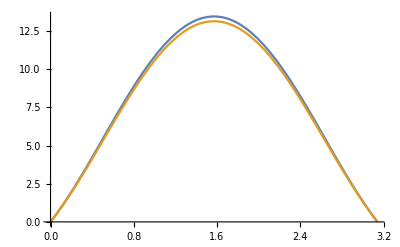

```mathematica
Plot[{Sum[A0[j](3)^j/j!,{j,0,10}]/.bmu->1,Sum[A0[j](3)^j/j!,{j,0,6}]/.bmu->1},{t1,0,Pi}]
```

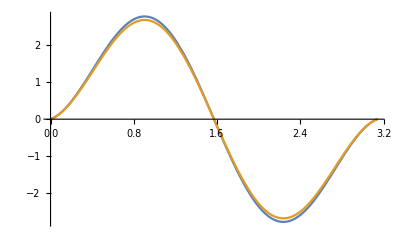

```mathematica
Plot[{Sum[A1[j](3)^j/j!,{j,0,10}]/.bmu->1,Sum[A1[j](3)^j/j!,{j,0,6}]/.bmu->1},{t1,0,Pi}]
```

```mathematica
Table[{j,bmu Cos[t1]A[j,0,t1]+B[j,0,t1]},{j,0,10}]//TableForm
```

0 | bmu π Cos[t1]
1 | 1/2 π Cos[t1]+2 bmu Cos[t1] Sin[t1]
2 | 1/2 bmu π Cos[t1]+2/3 Sin[2 t1]
3 | 3/8 π Cos[t1]+1/2 bmu Cos[t1] (3 Sin[t1]+1/3 Sin[3 t1])
4 | 3/8 bmu π Cos[t1]+1/4 (8/3 Sin[2 t1]+4/15 Sin[4 t1])
5 | 5/16 π Cos[t1]+1/8 bmu Cos[t1] (10 Sin[t1]+5/3 Sin[3 t1]+1/5 Sin[5 t1])
6 | 5/16 bmu π Cos[t1]+1/16 (10 Sin[2 t1]+8/5 Sin[4 t1]+6/35 Sin[6 t1])
7 | 35/128 π Cos[t1]+1/32 bmu Cos[t1] (35 Sin[t1]+7 Sin[3 t1]+7/5 Sin[5 t1]+1/7 Sin[7 t1])
8 | 35/128 bmu π Cos[t1]+1/64 (112/3 Sin[2 t1]+112/15 Sin[4 t1]+48/35 Sin[6 t1]+8/63 Sin[8 t1])
9 | 63/256 π Cos[t1]+1/128 bmu Cos[t1] (126 Sin[t1]+28 Sin[3 t1]+36/5 Sin[5 t1]+9/7 Sin[7 t1]+1/9 Sin[9 t1])
10 | 63/256 bmu π Cos[t1]+1/256 (140 Sin[2 t1]+32 Sin[4 t1]+54/7 Sin[6 t1]+80/63 Sin[8 t1]+10/99 Sin[10 t1])

## Poisson-equation approach, Series treatment -- (0, 2Pi) integration

```mathematica
Brute force solution
```

```mathematica
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qx0+bmu(Cos[theta1]+Cos[theta2]))
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qx1+bmu^2(Cos[theta1]+Cos[theta2])^2+Qx0 bmu(Cos[theta1]+Cos[theta2]))
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n/2 theta2],{theta2,0,2Pi}]
H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n/2 theta2],{theta2,0,2Pi}]
A0[0,j_,theta1_]:=Integrate[h0[0,j](theta1-t1),{t1,0,theta1}]
A0[n_,j_,theta1_]:=2/n Integrate[h0[n,j]Sinh[n/2(theta1-t1)],{t1,0,theta1}]-2Cosh[n/2 theta1]/(n Sinh[n Pi])Integrate[h0[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
A1[0,j_,theta1_]:=Integrate[h1[0,j](theta1-t1),{t1,0,theta1}]
A1[n_,j_,theta1_]:=2/n Integrate[h1[n,j]Sinh[n/2(theta1-t1)],{t1,0,theta1}]-2Cosh[n/2 theta1]/(n Sinh[n Pi])Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
dA0[0,j_,theta1_]:=Integrate[h0[0,j],{t1,0,theta1}]
dA0[n_,j_,theta1_]:=Integrate[h0[n,j]Cosh[n/2(theta1-t1)],{t1,0,theta1}]-Sinh[n/2 theta1]/Sinh[n Pi]Integrate[h0[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
dA1[0,j_,theta1_]:=Integrate[h1[0,j],{t1,0,theta1}]
dA1[n_,j_,theta1_]:=Integrate[h1[n,j]Cosh[n/2(theta1-t1)],{t1,0,theta1}]-2Sinh[n/2 theta1]/Sinh[n Pi]Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
pv10[bJ_,bmu_]:=Sum[da0[n,j]Cos[n/2 theta2]/.{Qx0->0},{n,0,nmax},{j,0,jmax}]
pv20[bJ_,bmu_]:=-Sum[n/2a0[n,j]Sin[n/2 theta2]/.{Qx0->0},{n,1,nmax},{j,0,jmax}]
```

```mathematica
Flatten[Table[{n,j,h0[n,j]=H0[n,j,t1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm
```

0 | 0 | Qx0+bmu Cos[t1]
0 | 1 | 1/2 bJ bmu Cos[t1]
0 | 2 | 1/4 bJ^2 (Qx0+bmu Cos[t1])
0 | 3 | 1/16 bJ^3 bmu Cos[t1]
0 | 4 | 1/64 bJ^4 (Qx0+bmu Cos[t1])
0 | 5 | 1/384 bJ^5 bmu Cos[t1]
0 | 6 | (bJ^6 (Qx0+bmu Cos[t1]))/2304
0 | 7 | (bJ^7 bmu Cos[t1])/18432
0 | 8 | (bJ^8 (Qx0+bmu Cos[t1]))/147456
0 | 9 | (bJ^9 bmu Cos[t1])/1474560
0 | 10 | (bJ^10 (Qx0+bmu Cos[t1]))/14745600
1 | 0 | 0
1 | 1 | (8 bJ (bmu+5 Qx0+5 bmu Cos[t1]) Sin[t1])/(15 π)
1 | 2 | (4 bJ^2 (11 bmu+7 Qx0+7 bmu Cos[t1]) Sin[2 t1])/(105 π)
1 | 3 | (bJ^3 (94 bmu+342 Qx0+369 bmu Cos[t1]+(62 bmu+54 Qx0) Cos[2 t1]+27 bmu Cos[3 t1]) Sin[t1])/(945 π)
1 | 4 | (bJ^4 (517 bmu Cos[t1]+2 (59 bmu+55 Qx0) Cos[2 t1]+11 (66 bmu+42 Qx0+5 bmu Cos[3 t1])) Sin[2 t1])/(20790 π)
1 | 5 | (bJ^5 (10914 bmu+34346 Qx0+38662 bmu Cos[t1]+(9816 bmu+8632 Qx0) Cos[2 t1]+4771 bmu Cos[3 t1]+950 bmu Cos[4 t1]+910 Qx0 Cos[4 t1]+455 bmu Cos[5 t1]) Sin[t1])/(2162160 π)
1 | 6 | (bJ^6 (71758 bmu+45990 Qx0+54570 bmu Cos[t1]+312 (59 bmu+55 Qx0) Cos[2 t1]+9525 bmu Cos[3 t1]+1946 bmu Cos[4 t1]+1890 Qx0 Cos[4 t1]+945 bmu Cos[5 t1]) Sin[2 t1])/(64864800 π)
1 | 7 | (bJ^7 (525724 bmu+1515788 Qx0+1755301 bmu Cos[t1]+(540938 bmu+479026 Qx0) Cos[2 t1]+282115 bmu Cos[3 t1]+88772 bmu Cos[4 t1]+85204 Qx0 Cos[4 t1]+46529 bmu Cos[5 t1]+8022 bmu Cos[6 t1]+7854 Qx0 Cos[6 t1]+3927 bmu Cos[7 t1]) Sin[t1])/(4410806400 π)
1 | 8 | (bJ^8 (1/15 (11 bmu+7 Qx0+7 bmu Cos[t1]) Sin[2 t1]+(8398 (59 bmu+55 Qx0+55 bmu Cos[t1]) Sin[4 t1]+646 (139 bmu+135 Qx0+135 bmu Cos[t1]) Sin[6 t1]+33 (251 bmu+247 Qx0+247 bmu Cos[t1]) Sin[8 t1])/4157010))/(40320 π)
1 | 9 | (bJ^9 (21/80 (bmu+5 Qx0+5 bmu Cos[t1]) Sin[t1]+1/120 (31 bmu+27 Qx0+27 bmu Cos[t1]) Sin[3 t1]+(32300 (95 bmu+91 Qx0+91 bmu Cos[t1]) Sin[5 t1]+2793 (191 bmu+187 Qx0+187 bmu Cos[t1]) Sin[7 t1]+143 (319 bmu+315 Qx0+315 bmu Cos[t1]) Sin[9 t1])/51731680))/(362880 π)
1 | 10 | (bJ^10 (7/8 bmu Cos[t1]^2 Sin[t1]+1/462 (59 bmu+55 Qx0) Sin[4 t1]+(139 bmu Sin[6 t1])/4576+(135 Qx0 Sin[6 t1])/4576+(251 bmu Sin[8 t1])/50388+1/204 Qx0 Sin[8 t1]+(1975 bmu Sin[10 t1])/4992288+(5 Qx0 Sin[10 t1])/12768+Cos[t1] (1/8 (11 bmu+7 Qx0) Sin[t1]+5/42 bmu Sin[4 t1]+(135 bmu Sin[6 t1])/4576+1/204 bmu Sin[8 t1]+(5 bmu Sin[10 t1])/12768)))/(3628800 π)
2 | 0 | bmu
2 | 1 | bJ Cos[t1] (Qx0+bmu Cos[t1])
2 | 2 | 1/8 bJ^2 bmu (2+Cos[2 t1])
2 | 3 | 1/8 bJ^3 Cos[t1] (Qx0+bmu Cos[t1])
2 | 4 | 1/192 bJ^4 bmu (3+2 Cos[2 t1])
2 | 5 | 1/192 bJ^5 Cos[t1] (Qx0+bmu Cos[t1])
2 | 6 | (bJ^6 bmu (4+3 Cos[2 t1]))/9216
2 | 7 | (bJ^7 Cos[t1] (Qx0+bmu Cos[t1]))/9216
2 | 8 | (bJ^8 bmu (5+4 Cos[2 t1]))/737280
2 | 9 | (bJ^9 Cos[t1] (Qx0+bmu Cos[t1]))/737280
2 | 10 | (bJ^10 bmu (6+5 Cos[2 t1]))/88473600
3 | 0 | 0
3 | 1 | -(8 bJ (-5 bmu+7 Qx0+7 bmu Cos[t1]) Sin[t1])/(35 π)
3 | 2 | (4 bJ^2 (-7 bmu+45 Qx0+45 bmu Cos[t1]) Sin[2 t1])/(315 π)
3 | 3 | (bJ^3 (-297 (-5 bmu+7 Qx0+7 bmu Cos[t1]) Sin[t1]+(621 bmu+385 Qx0+385 bmu Cos[t1]) Sin[3 t1]))/(10395 π)
3 | 4 | (bJ^4 (13689 bmu Cos[t1]+2 (935 bmu+819 Qx0) Cos[2 t1]+13 (-154 bmu+990 Qx0+63 bmu Cos[3 t1])) Sin[2 t1])/(270270 π)
3 | 5 | (bJ^5 (-12870 (-5 bmu+7 Qx0+7 bmu Cos[t1]) Sin[t1]+65 (621 bmu+385 Qx0+385 bmu Cos[t1]) Sin[3 t1]+(2639 bmu+2475 Qx0+2475 bmu Cos[t1]) Sin[5 t1]))/(10810800 π)
3 | 6 | (bJ^6 (-237570 bmu+1657942 Qx0+1825018 bmu Cos[t1]+408 (935 bmu+819 Qx0) Cos[2 t1]+184093 bmu Cos[3 t1]+35370 bmu Cos[4 t1]+34034 Qx0 Cos[4 t1]+17017 bmu Cos[5 t1]) Sin[2 t1])/(1102701600 π)
3 | 7 | (bJ^7 (-1/8 (-5 bmu+7 Qx0+7 bmu Cos[t1]) Sin[t1]+((621 bmu+385 Qx0+385 bmu Cos[t1]) Sin[3 t1])/1320+(203 bmu Sin[5 t1])/3960+5/104 Qx0 Sin[5 t1]+5/104 bmu Cos[t1] Sin[5 t1]+(427 bmu Sin[7 t1])/88920+(7 Qx0 Sin[7 t1])/1496+(7 bmu Cos[t1] Sin[7 t1])/1496))/(5040 π)
3 | 8 | (bJ^8 ((-(7 bmu)/32+Qx0) Sin[2 t1]+17/117 bmu Sin[4 t1]+7/55 Qx0 Sin[4 t1]+(393 bmu Sin[6 t1])/17017+1/45 Qx0 Sin[6 t1]+(27 bmu Sin[8 t1])/13090+1/494 Qx0 Sin[8 t1]+Cos[t1] (91/720 bmu Sin[t1]+bmu Sin[2 t1]+7/55 bmu Sin[4 t1]+1/45 bmu Sin[6 t1]+1/494 bmu Sin[8 t1])))/(40320 π)
3 | 9 | (bJ^9 (-9/80 (-5 bmu+7 Qx0+7 bmu Cos[t1]) Sin[t1]+((621 bmu+385 Qx0+385 bmu Cos[t1]) Sin[3 t1])/1320+29/440 bmu Sin[5 t1]+45/728 Qx0 Sin[5 t1]+45/728 bmu Cos[t1] Sin[5 t1]+(427 bmu Sin[7 t1])/39520+(63 Qx0 Sin[7 t1])/5984+(63 bmu Cos[t1] Sin[7 t1])/5984+(2799 bmu Sin[9 t1])/3090464+(Qx0 Sin[9 t1])/1120+(bmu Cos[t1] Sin[9 t1])/1120))/(362880 π)
3 | 10 | (bJ^10 (-2015911498 bmu+17296829550 Qx0+19820890950 bmu Cos[t1]+9200 (624017 bmu+548709 Qx0) Cos[2 t1]+3088925700 bmu Cos[3 t1]+1173677304 bmu Cos[4 t1]+1129728600 Qx0 Cos[4 t1]+655185300 bmu Cos[5 t1]+184064400 bmu Cos[6 t1]+180642000 Qx0 Cos[6 t1]+97453125 bmu Cos[7 t1]+14425554 bmu Cos[8 t1]+14264250 Qx0 Cos[8 t1]+7132125 bmu Cos[9 t1]) Sin[2 t1])/(64764752532480000 π)
4 | 0 | 0
4 | 1 | 1/2 bJ bmu Cos[t1]
4 | 2 | 1/4 bJ^2 (Qx0+bmu Cos[t1]) Cos[2 t1]
4 | 3 | 1/12 bJ^3 bmu Cos[t1]^3
4 | 4 | 1/48 bJ^4 (Qx0+bmu Cos[t1]) Cos[2 t1]
4 | 5 | 1/768 bJ^5 bmu (2 Cos[t1]+Cos[3 t1])
4 | 6 | (bJ^6 (Qx0+bmu Cos[t1]) Cos[2 t1])/1536
4 | 7 | (bJ^7 bmu (5 Cos[t1]+3 Cos[3 t1]))/92160
4 | 8 | (bJ^8 (Qx0+bmu Cos[t1]) Cos[2 t1])/92160
4 | 9 | (bJ^9 bmu (3 Cos[t1]+2 Cos[3 t1]))/4423680
4 | 10 | (bJ^10 (Qx0+bmu Cos[t1]) Cos[2 t1])/8847360
5 | 0 | 0
5 | 1 | -(8 bJ (7 bmu+3 Qx0+3 bmu Cos[t1]) Sin[t1])/(63 π)
5 | 2 | -(4 bJ^2 (-39 bmu+77 Qx0+77 bmu Cos[t1]) Sin[2 t1])/(693 π)
5 | 3 | (bJ^3 (-3542 bmu+1170 Qx0+3627 bmu Cos[t1]-14 (77 bmu-351 Qx0) Cos[2 t1]+2457 bmu Cos[3 t1]) Sin[t1])/(27027 π)
5 | 4 | (bJ^4 (-8855 bmu Cos[t1]+42 (91 bmu+55 Qx0) Cos[2 t1]+5 (1014 bmu-2002 Qx0+231 bmu Cos[3 t1])) Sin[2 t1])/(270270 π)
5 | 5 | (bJ^5 (-1021350 bmu+730626 Qx0+1825902 bmu Cos[t1]+8 (-42625 bmu+273819 Qx0) Cos[2 t1]+1146327 bmu Cos[3 t1]+66 (1775 bmu+1547 Qx0) Cos[4 t1]+51051 bmu Cos[5 t1]) Sin[t1])/(183783600 π)
5 | 6 | (bJ^6 (12673466 bmu-23882430 Qx0-19405650 bmu Cos[t1]+162792 (91 bmu+55 Qx0) Cos[2 t1]+4843575 bmu Cos[3 t1]+782782 bmu Cos[4 t1]+733590 Qx0 Cos[4 t1]+366795 bmu Cos[5 t1]) Sin[2 t1])/(20951330400 π)
5 | 7 | (bJ^7 (-5/72 (7 bmu+3 Qx0+3 bmu Cos[t1]) Sin[t1]+(7 (-77 bmu+351 Qx0+351 bmu Cos[t1]) Sin[3 t1])/3432+(355 bmu Sin[5 t1])/5304+7/120 Qx0 Sin[5 t1]+7/120 bmu Cos[t1] Sin[5 t1]+(167 bmu Sin[7 t1])/31416+(7 Qx0 Sin[7 t1])/1368+(7 bmu Cos[t1] Sin[7 t1])/1368))/(5040 π)
5 | 8 | (bJ^8 (281659196 bmu-503677460 Qx0-382101875 bmu Cos[t1]+34 (11778893 bmu+7151505 Qx0) Cos[2 t1]+138448155 bmu Cos[3 t1]+36007972 bmu Cos[4 t1]+33745140 Qx0 Cos[4 t1]+18321225 bmu Cos[5 t1]+2971430 bmu Cos[6 t1]+2897310 Qx0 Cos[6 t1]+1448655 bmu Cos[7 t1]) Sin[2 t1])/(26985313555200 π)
5 | 9 | (bJ^9 (-1/16 (7 bmu+3 Qx0+3 bmu Cos[t1]) Sin[t1]+(7 (-77 bmu+351 Qx0+351 bmu Cos[t1]) Sin[3 t1])/3432+(1065 bmu Sin[5 t1])/12376+3/40 Qx0 Sin[5 t1]+3/40 bmu Cos[t1] Sin[5 t1]+(501 bmu Sin[7 t1])/41888+7/608 Qx0 Sin[7 t1]+7/608 bmu Cos[t1] Sin[7 t1]+(59 bmu Sin[9 t1])/61600+(9 Qx0 Sin[9 t1])/9568+(9 bmu Cos[t1] Sin[9 t1])/9568))/(362880 π)
5 | 10 | (bJ^10 (65466614150 bmu-111362336514 Qx0-79603361514 bmu Cos[t1]+20400 (5098037 bmu+3113625 Qx0) Cos[2 t1]+37520395236 bmu Cos[3 t1]+88 (139640725 bmu+130941369 Qx0) Cos[4 t1]+6630613236 bmu Cos[5 t1]+102000 (17479 bmu+17043 Qx0) Cos[6 t1]+936120861 bmu Cos[7 t1]+2926 (46375 bmu+45747 Qx0) Cos[8 t1]+66927861 bmu Cos[9 t1]) Sin[2 t1])/(582882772792320000 π)
6 | 0 | 0
6 | 1 | 0
6 | 2 | 1/8 bJ^2 bmu Cos[2 t1]
6 | 3 | 1/24 bJ^3 (Qx0+bmu Cos[t1]) Cos[3 t1]
6 | 4 | 1/384 bJ^4 bmu (4 Cos[2 t1]+Cos[4 t1])
6 | 5 | 1/384 bJ^5 (Qx0+bmu Cos[t1]) Cos[3 t1]
6 | 6 | (bJ^6 bmu (5 Cos[2 t1]+2 Cos[4 t1]))/15360
6 | 7 | (bJ^7 (Qx0+bmu Cos[t1]) Cos[3 t1])/15360
6 | 8 | (bJ^8 bmu (2 Cos[2 t1]+Cos[4 t1]))/368640
6 | 9 | (bJ^9 (Qx0+bmu Cos[t1]) Cos[3 t1])/1105920
6 | 10 | (bJ^10 bmu (7 Cos[2 t1]+4 Cos[4 t1]))/123863040
7 | 0 | 0
7 | 1 | -(8 bJ (15 bmu+11 Qx0+11 bmu Cos[t1]) Sin[t1])/(495 π)
7 | 2 | -(4 bJ^2 (407 bmu+195 Qx0+195 bmu Cos[t1]) Sin[2 t1])/(6435 π)
7 | 3 | -(bJ^3 (-26 bmu+638 Qx0+1133 bmu Cos[t1]+(-442 bmu+990 Qx0) Cos[2 t1]+495 bmu Cos[3 t1]) Sin[t1])/(6435 π)
7 | 4 | (bJ^4 (663 bmu Cos[t1]-66 (55 bmu-221 Qx0) Cos[2 t1]+17 (-814 bmu-390 Qx0+429 bmu Cos[3 t1])) Sin[2 t1])/(656370 π)
7 | 5 | (bJ^5 (783666 bmu-2656390 Qx0-4850890 bmu Cos[t1]+24 (117793 bmu-182875 Qx0) Cos[2 t1]-1990725 bmu Cos[3 t1]+685542 bmu Cos[4 t1]+407550 Qx0 Cos[4 t1]+203775 bmu Cos[5 t1]) Sin[t1])/(498841200 π)
7 | 6 | (bJ^6 (-4424530 bmu-2051322 Qx0+1828554 bmu Cos[t1]-35112 (55 bmu-221 Qx0) Cos[2 t1]+4033029 bmu Cos[3 t1]+353210 bmu Cos[4 t1]+306306 Qx0 Cos[4 t1]+153153 bmu Cos[5 t1]) Sin[2 t1])/(6983776800 π)
7 | 7 | (bJ^7 (772454228 bmu-1636398940 Qx0-3012522865 bmu Cos[t1]+(2254749406 bmu-2752247850 Qx0) Cos[2 t1]-1130534295 bmu Cos[3 t1]+806673868 bmu Cos[4 t1]+491179260 Qx0 Cos[4 t1]+261524835 bmu Cos[5 t1]+34068034 bmu Cos[6 t1]+31870410 Qx0 Cos[6 t1]+15935205 bmu Cos[7 t1]) Sin[t1])/(13492656777600 π)
7 | 8 | (bJ^8 ((-(7 bmu)/32-(7 Qx0)/33) Sin[2 t1]-77/663 bmu Sin[4 t1]+7/15 Qx0 Sin[4 t1]+13/357 bmu Sin[6 t1]+3/95 Qx0 Sin[6 t1]+(29 bmu Sin[8 t1])/11550+1/414 Qx0 Sin[8 t1]+Cos[t1] (-(4193 bmu Sin[t1])/9360-7/33 bmu Sin[2 t1]+7/15 bmu Sin[4 t1]+3/95 bmu Sin[6 t1]+1/414 bmu Sin[8 t1])))/(40320 π)
7 | 9 | (bJ^9 (-(7 (60 bmu+44 Qx0+209 bmu Cos[t1]) Sin[t1])/3520-(7 (-1768 bmu+3960 Qx0+1815 bmu Cos[t1]) Sin[3 t1])/45760-21/128 bmu Sin[4 t1]+141/760 bmu Sin[5 t1]+15/136 Qx0 Sin[5 t1]+15/136 bmu Cos[t1] Sin[5 t1]+(1001 bmu Sin[7 t1])/69920+3/224 Qx0 Sin[7 t1]+3/224 bmu Cos[t1] Sin[7 t1]+(271 bmu Sin[9 t1])/258336+(9 Qx0 Sin[9 t1])/8800+(9 bmu Cos[t1] Sin[9 t1])/8800))/(362880 π)
7 | 10 | (bJ^10 (-1692795710178 bmu-717408891850 Qx0+1639809771950 bmu Cos[t1]-132240 (8324229 bmu-35650615 Qx0) Cos[2 t1]+2566152211700 bmu Cos[3 t1]+481294456344 bmu Cos[4 t1]+417867095800 Qx0 Cos[4 t1]+237062648900 bmu Cos[5 t1]+58479305040 bmu Cos[6 t1]+56258202000 Qx0 Cos[6 t1]+30202720625 bmu Cos[7 t1]+4222539594 bmu Cos[8 t1]+4147239250 Qx0 Cos[8 t1]+2073619625 bmu Cos[9 t1]) Sin[2 t1])/(16903600410977280000 π)
8 | 0 | 0
8 | 1 | 0
8 | 2 | 0
8 | 3 | 1/48 bJ^3 bmu Cos[3 t1]
8 | 4 | 1/192 bJ^4 (Qx0+bmu Cos[t1]) Cos[4 t1]
8 | 5 | (bJ^5 bmu (5 Cos[3 t1]+Cos[5 t1]))/3840
8 | 6 | (bJ^6 (Qx0+bmu Cos[t1]) Cos[4 t1])/3840
8 | 7 | (bJ^7 bmu (3 Cos[3 t1]+Cos[5 t1]))/92160
8 | 8 | (bJ^8 (Qx0+bmu Cos[t1]) Cos[4 t1])/184320
8 | 9 | (bJ^9 bmu (7 Cos[3 t1]+3 Cos[5 t1]))/15482880
8 | 10 | (bJ^10 (Qx0+bmu Cos[t1]) Cos[4 t1])/15482880
9 | 0 | 0
9 | 1 | -(8 bJ (77 bmu+65 Qx0+65 bmu Cos[t1]) Sin[t1])/(5005 π)
9 | 2 | -(4 bJ^2 (299 bmu+231 Qx0+231 bmu Cos[t1]) Sin[2 t1])/(15015 π)
9 | 3 | -(bJ^3 (45738 bmu+26962 Qx0+43979 bmu Cos[t1]+154 (441 bmu+221 Qx0) Cos[2 t1]+17017 bmu Cos[3 t1]) Sin[t1])/(765765 π)
9 | 4 | -(bJ^4 (434511 bmu Cos[t1]-2002 (119 bmu-285 Qx0) Cos[2 t1]+19 (10166 bmu+7854 Qx0+15015 bmu Cos[3 t1])) Sin[2 t1])/(29099070 π)
9 | 5 | -(bJ^5 (862334 bmu+194038 Qx0+262106 bmu Cos[t1]+88 (16207 bmu+1547 Qx0) Cos[2 t1]-187187 bmu Cos[3 t1]+135850 bmu Cos[4 t1]-510510 Qx0 Cos[4 t1]-255255 bmu Cos[5 t1]) Sin[t1])/(232792560 π)
9 | 6 | (bJ^6 (-24283038 bmu-20429750 Qx0-99168410 bmu Cos[t1]+552552 (119 bmu-285 Qx0) Cos[2 t1]-73426925 bmu Cos[3 t1]+18072054 bmu Cos[4 t1]+10623470 Qx0 Cos[4 t1]+5311735 bmu Cos[5 t1]) Sin[2 t1])/(160626866400 π)
9 | 7 | (bJ^7 (-2092525556 bmu+27010620 Qx0+307535865 bmu Cos[t1]+(-3584416462 bmu+561050490 Qx0) Cos[2 t1]+1341875535 bmu Cos[3 t1]-468182572 bmu Cos[4 t1]+2122700580 Qx0 Cos[4 t1]+1095299205 bmu Cos[5 t1]+78613678 bmu Cos[6 t1]+67897830 Qx0 Cos[6 t1]+33948915 bmu Cos[7 t1]) Sin[t1])/(22487761296000 π)
9 | 8 | (bJ^8 (-((299 bmu+231 Qx0+231 bmu Cos[t1]) Sin[2 t1])/2145+((49 bmu)/285-(7 Qx0)/17-7/17 bmu Cos[t1]) Sin[4 t1]+(177 bmu Sin[6 t1])/2185+1/21 Qx0 Sin[6 t1]+1/21 bmu Cos[t1] Sin[6 t1]+(19 bmu Sin[8 t1])/6210+1/350 Qx0 Sin[8 t1]+1/350 bmu Cos[t1] Sin[8 t1]))/(40320 π)
9 | 9 | (bJ^9 (-((36 (77 bmu+65 Qx0)+7345 bmu Cos[t1]) Sin[t1])/45760-(7 (3528 bmu+1768 Qx0+663 bmu Cos[t1]) Sin[3 t1])/70720-7/128 bmu Sin[4 t1]-75/952 bmu Sin[5 t1]+45/152 Qx0 Sin[5 t1]+45/152 bmu Cos[t1] Sin[5 t1]+(111 bmu Sin[7 t1])/5600+(63 Qx0 Sin[7 t1])/3680+(63 bmu Cos[t1] Sin[7 t1])/3680+(2151 bmu Sin[9 t1])/1786400+1/864 Qx0 Sin[9 t1]+1/864 bmu Cos[t1] Sin[9 t1]))/(362880 π)
9 | 10 | (bJ^10 (-21/104 bmu Cos[t1]^2 Sin[t1]-21/208 Qx0 Sin[2 t1]+7/38 bmu Sin[4 t1]-15/34 Qx0 Sin[4 t1]+(1593 bmu Sin[6 t1])/13984+15/224 Qx0 Sin[6 t1]+(19 bmu Sin[8 t1])/2484+1/140 Qx0 Sin[8 t1]+(175 bmu Sin[10 t1])/348192+(5 Qx0 Sin[10 t1])/10208+Cos[t1] (-23/88 bmu Sin[t1]-15/34 bmu Sin[4 t1]+15/224 bmu Sin[6 t1]+1/140 bmu Sin[8 t1]+(5 bmu Sin[10 t1])/10208)))/(3628800 π)
10 | 0 | 0
10 | 1 | 0
10 | 2 | 0
10 | 3 | 0
10 | 4 | 1/384 bJ^4 bmu Cos[4 t1]
10 | 5 | (bJ^5 (Qx0+bmu Cos[t1]) Cos[5 t1])/1920
10 | 6 | (bJ^6 bmu (6 Cos[4 t1]+Cos[6 t1]))/46080
10 | 7 | (bJ^7 (Qx0+bmu Cos[t1]) Cos[5 t1])/46080
10 | 8 | (bJ^8 bmu (7 Cos[4 t1]+2 Cos[6 t1]))/2580480
10 | 9 | (bJ^9 (Qx0+bmu Cos[t1]) Cos[5 t1])/2580480
10 | 10 | (bJ^10 bmu (8 Cos[4 t1]+3 Cos[6 t1]))/247726080

```mathematica
Flatten[Table[{n,j,h1[n,j]=H1[n,j,t1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm
```

0 | 0 | 1/2 (bmu^2+2 Qx1+2 bmu Cos[t1] (Qx0+bmu Cos[t1]))
0 | 1 | 1/2 bJ bmu Cos[t1] (Qx0+2 bmu Cos[t1])
0 | 2 | 1/16 bJ^2 (4 (bmu^2+Qx1)+4 bmu Qx0 Cos[t1]+3 bmu^2 Cos[2 t1])
0 | 3 | 1/16 bJ^3 bmu Cos[t1] (Qx0+2 bmu Cos[t1])
0 | 4 | 1/384 bJ^4 (6 (bmu^2+Qx1)+6 bmu Qx0 Cos[t1]+5 bmu^2 Cos[2 t1])
0 | 5 | 1/384 bJ^5 bmu Cos[t1] (Qx0+2 bmu Cos[t1])
0 | 6 | (bJ^6 (8 (bmu^2+Qx1)+8 bmu Qx0 Cos[t1]+7 bmu^2 Cos[2 t1]))/18432
0 | 7 | (bJ^7 bmu Cos[t1] (Qx0+2 bmu Cos[t1]))/18432
0 | 8 | (bJ^8 (10 (bmu^2+Qx1)+10 bmu Qx0 Cos[t1]+9 bmu^2 Cos[2 t1]))/1474560
0 | 9 | (bJ^9 bmu Cos[t1] (Qx0+2 bmu Cos[t1]))/1474560
0 | 10 | (bJ^10 (12 (bmu^2+Qx1)+12 bmu Qx0 Cos[t1]+11 bmu^2 Cos[2 t1]))/176947200
1 | 0 | 0
1 | 1 | (4 bJ (57 bmu^2+14 bmu Qx0+70 Qx1+14 bmu (2 bmu+5 Qx0) Cos[t1]+35 bmu^2 Cos[2 t1]) Sin[t1])/(105 π)
1 | 2 | (2 bJ^2 (47 bmu^2+66 bmu Qx0+42 Qx1+6 bmu (22 bmu+7 Qx0) Cos[t1]+21 bmu^2 Cos[2 t1]) Sin[2 t1])/(315 π)
1 | 3 | (bJ^3 (7199 bmu^2+2068 bmu Qx0+7524 Qx1+22 bmu (250 bmu+369 Qx0) Cos[t1]+4 (1570 bmu^2+341 bmu Qx0+297 Qx1) Cos[2 t1]+22 bmu (62 bmu+27 Qx0) Cos[3 t1]+297 bmu^2 Cos[4 t1]) Sin[t1])/(20790 π)
1 | 4 | (bJ^4 (429 (33 bmu^2+44 bmu Qx0+28 Qx1)+26 bmu (1570 bmu+517 Qx0) Cos[t1]+4 (2710 bmu^2+767 bmu Qx0+715 Qx1) Cos[2 t1]+26 bmu (118 bmu+55 Qx0) Cos[3 t1]+715 bmu^2 Cos[4 t1]) Sin[2 t1])/(540540 π)
1 | 5 | (bJ^5 (2145 (167 bmu^2+56 bmu Qx0+280 Qx1) Sin[t1]+1430 bmu (146 bmu+237 Qx0) Sin[2 t1]+65 (4863 bmu^2+1364 bmu Qx0+1188 Qx1) Sin[3 t1]+40 bmu (2454 bmu+1079 Qx0) Sin[4 t1]+(33883 bmu^2+9500 bmu Qx0+9100 Qx1) Sin[5 t1]+50 bmu (190 bmu+91 Qx0) Sin[6 t1]+2275 bmu^2 Sin[7 t1]))/(43243200 π)
1 | 6 | (bJ^6 (2 (955003 bmu^2+1219886 bmu Qx0+781830 Qx1)+68 bmu (80962 bmu+27285 Qx0) Cos[t1]+51 (34981 bmu^2+12272 bmu Qx0+11440 Qx1) Cos[2 t1]+34 bmu (20354 bmu+9525 Qx0) Cos[3 t1]+14 (17603 bmu^2+4726 bmu Qx0+4590 Qx1) Cos[4 t1]+238 bmu (278 bmu+135 Qx0) Cos[5 t1]+16065 bmu^2 Cos[6 t1]) Sin[2 t1])/(2205403200 π)
1 | 7 | (bJ^7 (62486983 bmu^2+19977512 bmu Qx0+57599944 Qx1+38 bmu (1592386 bmu+1755301 Qx0) Cos[t1]+4 (16624673 bmu^2+5138911 bmu Qx0+4550747 Qx1) Cos[2 t1]+23928980 bmu^2 Cos[3 t1]+10720370 bmu Qx0 Cos[3 t1]+9795396 bmu^2 Cos[4 t1]+3373336 bmu Qx0 Cos[4 t1]+3237752 Qx1 Cos[4 t1]+3678172 bmu^2 Cos[5 t1]+1768102 bmu Qx0 Cos[5 t1]+1270780 bmu^2 Cos[6 t1]+304836 bmu Qx0 Cos[6 t1]+298452 Qx1 Cos[6 t1]+304836 bmu^2 Cos[7 t1]+149226 bmu Qx0 Cos[7 t1]+74613 bmu^2 Cos[8 t1]) Sin[t1])/(167610643200 π)
1 | 8 | (bJ^8 (35593707 bmu^2+43935752 bmu Qx0+28380072 Qx1+14 bmu (7284066 bmu+2497189 Qx0) Cos[t1]+4 (9252493 bmu^2+3526355 bmu Qx0+3290287 Qx1) Cos[2 t1]+16619652 bmu^2 Cos[3 t1]+7801514 bmu Qx0 Cos[3 t1]+7169460 bmu^2 Cos[4 t1]+2514232 bmu Qx0 Cos[4 t1]+2441880 Qx1 Cos[4 t1]+2746156 bmu^2 Cos[5 t1]+1335054 bmu Qx0 Cos[5 t1]+960588 bmu^2 Cos[6 t1]+231924 bmu Qx0 Cos[6 t1]+228228 Qx1 Cos[6 t1]+231924 bmu^2 Cos[7 t1]+114114 bmu Qx0 Cos[7 t1]+57057 bmu^2 Cos[8 t1]) Sin[2 t1])/(2346549004800 π)
1 | 9 | (bJ^9 (12850103162 bmu^2+4221580540 bmu Qx0+11460084972 Qx1+92 bmu (142808282 bmu+147285537 Qx0) Cos[t1]+2 (7161234977 bmu^2+2347600432 bmu Qx0+2090184432 Qx1) Cos[2 t1]+5701932944 bmu^2 Cos[3 t1]+2574100200 bmu Qx0 Cos[3 t1]+2625643176 bmu^2 Cos[4 t1]+1006732080 bmu Qx0 Cos[4 t1]+967831536 Qx1 Cos[4 t1]+1166558160 bmu^2 Cos[5 t1]+562208136 bmu Qx0 Cos[5 t1]+486871221 bmu^2 Cos[6 t1]+159826080 bmu Qx0 Cos[6 t1]+156584736 Qx1 Cos[6 t1]+172416372 bmu^2 Cos[7 t1]+84508578 bmu Qx0 Cos[7 t1]+58123230 bmu^2 Cos[8 t1]+12590292 bmu Qx0 Cos[8 t1]+12432420 Qx1 Cos[8 t1]+12590292 bmu^2 Cos[9 t1]+6216210 bmu Qx0 Cos[9 t1]+3108105 bmu^2 Cos[10 t1]) Sin[t1])/(2590590101299200 π)
1 | 10 | (bJ^10 (21357339602 bmu^2+25638599500 bmu Qx0+16683539900 Qx1+100 bmu (607496846 bmu+211079027 Qx0) Cos[t1]+3450 (6891841 bmu^2+2745648 bmu Qx0+2564848 Qx1) Cos[2 t1]+11669253200 bmu^2 Cos[3 t1]+5491401800 bmu Qx0 Cos[3 t1]+5638768904 bmu^2 Cos[4 t1]+2196767600 bmu Qx0 Cos[4 t1]+2134078000 Qx1 Cos[4 t1]+2552384400 bmu^2 Cos[5 t1]+1242013800 bmu Qx0 Cos[5 t1]+1077356225 bmu^2 Cos[6 t1]+355616800 bmu Qx0 Cos[6 t1]+349949600 Qx1 Cos[6 t1]+383859300 bmu^2 Cos[7 t1]+188953050 bmu Qx0 Cos[7 t1]+130012454 bmu^2 Cos[8 t1]+28242500 bmu Qx0 Cos[8 t1]+27956500 Qx1 Cos[8 t1]+28242500 bmu^2 Cos[9 t1]+13978250 bmu Qx0 Cos[9 t1]+6989125 bmu^2 Cos[10 t1]) Sin[2 t1])/(129529505064960000 π)
2 | 0 | bmu (Qx0+2 bmu Cos[t1])
2 | 1 | 1/4 bJ Cos[t1] (5 bmu^2+4 Qx1+4 bmu Qx0 Cos[t1]+2 bmu^2 Cos[2 t1])
2 | 2 | 1/8 bJ^2 bmu (Qx0+2 bmu Cos[t1]) (2+Cos[2 t1])
2 | 3 | 1/48 bJ^3 Cos[t1] (7 bmu^2+6 Qx1+6 bmu Qx0 Cos[t1]+4 bmu^2 Cos[2 t1])
2 | 4 | 1/192 bJ^4 bmu (Qx0+2 bmu Cos[t1]) (3+2 Cos[2 t1])
2 | 5 | (bJ^5 Cos[t1] (9 bmu^2+8 Qx1+8 bmu Qx0 Cos[t1]+6 bmu^2 Cos[2 t1]))/1536
2 | 6 | (bJ^6 bmu (Qx0+2 bmu Cos[t1]) (4+3 Cos[2 t1]))/9216
2 | 7 | (bJ^7 Cos[t1] (11 bmu^2+10 Qx1+10 bmu Qx0 Cos[t1]+8 bmu^2 Cos[2 t1]))/92160
2 | 8 | (bJ^8 bmu (Qx0+2 bmu Cos[t1]) (5+4 Cos[2 t1]))/737280
2 | 9 | (bJ^9 Cos[t1] (13 bmu^2+12 Qx1+12 bmu Qx0 Cos[t1]+10 bmu^2 Cos[2 t1]))/8847360
2 | 10 | (bJ^10 bmu (Qx0+2 bmu Cos[t1]) (6+5 Cos[2 t1]))/88473600
3 | 0 | 0
3 | 1 | -(4 bJ (77 bmu^2-90 bmu Qx0+126 Qx1-18 bmu (10 bmu-7 Qx0) Cos[t1]+63 bmu^2 Cos[2 t1]) Sin[t1])/(315 π)
3 | 2 | (2 bJ^2 (1053 bmu^2-154 bmu Qx0+990 Qx1-22 bmu (14 bmu-45 Qx0) Cos[t1]+495 bmu^2 Cos[2 t1]) Sin[2 t1])/(3465 π)
3 | 3 | (bJ^3 (-21285 bmu^2+54756 bmu Qx0-44044 Qx1+26 bmu (5454 bmu-1309 Qx0) Cos[t1]+(-8536 bmu^2+32292 bmu Qx0+20020 Qx1) Cos[2 t1]+32292 bmu^2 Cos[3 t1]+10010 bmu Qx0 Cos[3 t1]+5005 bmu^2 Cos[4 t1]) Sin[t1])/(270270 π)
3 | 4 | (bJ^4 (28197 bmu^2-4004 bmu Qx0+25740 Qx1-2 bmu (2134 bmu-13689 Qx0) Cos[t1]+4 (4966 bmu^2+935 bmu Qx0+819 Qx1) Cos[2 t1]+3740 bmu^2 Cos[3 t1]+1638 bmu Qx0 Cos[3 t1]+819 bmu^2 Cos[4 t1]) Sin[2 t1])/(540540 π)
3 | 5 | (bJ^5 (-36465 (49 bmu^2-120 bmu Qx0+168 Qx1) Sin[t1]+2210 bmu (3222 bmu-1001 Qx0) Sin[2 t1]-85 (4037 bmu^2-32292 bmu Qx0-20020 Qx1) Sin[3 t1]+136 bmu (21502 bmu+6875 Qx0) Sin[4 t1]+(707475 bmu^2+179452 bmu Qx0+168300 Qx1) Sin[5 t1]+34 bmu (5278 bmu+2475 Qx0) Sin[6 t1]+42075 bmu^2 Sin[7 t1]))/(735134400 π)
3 | 6 | (bJ^6 (70526642 bmu^2-9027660 bmu Qx0+63001796 Qx1-76 bmu (46830 bmu-912509 Qx0) Cos[t1]+323 (182455 bmu^2+44880 bmu Qx0+39312 Qx1) Cos[2 t1]+15840300 bmu^2 Cos[3 t1]+6995534 bmu Qx0 Cos[3 t1]+5232430 bmu^2 Cos[4 t1]+1344060 bmu Qx0 Cos[4 t1]+1293292 Qx1 Cos[4 t1]+1344060 bmu^2 Cos[5 t1]+646646 bmu Qx0 Cos[5 t1]+323323 bmu^2 Cos[6 t1]) Sin[2 t1])/(41902660800 π)
3 | 7 | (bJ^7 (-18198903 bmu^2+268065112 bmu Qx0-123514440 Qx1+14 bmu (55804982 bmu-3095385 Qx0) Cos[t1]+4 (19191311 bmu^2+61284881 bmu Qx0+40089525 Qx1) Cos[2 t1]+271242412 bmu^2 Cos[3 t1]+92460270 bmu Qx0 Cos[3 t1]+81540476 bmu^2 Cos[4 t1]+26102888 bmu Qx0 Cos[4 t1]+24562440 Qx1 Cos[4 t1]+28338660 bmu^2 Cos[5 t1]+13370490 bmu Qx0 Cos[5 t1]+9534276 bmu^2 Cos[6 t1]+2235772 bmu Qx0 Cos[6 t1]+2178540 Qx1 Cos[6 t1]+2235772 bmu^2 Cos[7 t1]+1089270 bmu Qx0 Cos[7 t1]+544635 bmu^2 Cos[8 t1]) Sin[t1])/(1173274502400 π)
3 | 8 | (bJ^8 (1557607541 bmu^2-177306632 bmu Qx0+1368302936 Qx1+46 bmu (867198 bmu+33508139 Qx0) Cos[t1]+4 (358697619 bmu^2+98626093 bmu Qx0+86535729 Qx1) Cos[2 t1]+456331132 bmu^2 Cos[3 t1]+202817174 bmu Qx0 Cos[3 t1]+182557900 bmu^2 Cos[4 t1]+61826760 bmu Qx0 Cos[4 t1]+59491432 Qx1 Cos[4 t1]+67348692 bmu^2 Cos[5 t1]+32455346 bmu Qx0 Cos[5 t1]+23221044 bmu^2 Cos[6 t1]+5521932 bmu Qx0 Cos[6 t1]+5419260 Qx1 Cos[6 t1]+5521932 bmu^2 Cos[7 t1]+2709630 bmu Qx0 Cos[7 t1]+1354815 bmu^2 Cos[8 t1]) Sin[2 t1])/(53970627110400 π)
3 | 9 | (bJ^9 (679364754 bmu^2+39641781900 bmu Qx0-15084619460 Qx1+100 bmu (1184104110 bmu-20595373 Qx0) Cos[t1]+2 (8227340189 bmu^2+19563423600 bmu Qx0+13025082160 Qx1) Cos[2 t1]+44668076880 bmu^2 Cos[3 t1]+15639163720 bmu Qx0 Cos[3 t1]+15380075528 bmu^2 Cos[4 t1]+5541229680 bmu Qx0 Cos[4 t1]+5228163120 Qx1 Cos[4 t1]+6377227920 bmu^2 Cos[5 t1]+3021750120 bmu Qx0 Cos[5 t1]+2591325153 bmu^2 Cos[6 t1]+835998240 bmu Qx0 Cos[6 t1]+815337120 Qx1 Cos[6 t1]+900655140 bmu^2 Cos[7 t1]+439538970 bmu Qx0 Cos[7 t1]+301368678 bmu^2 Cos[8 t1]+64656900 bmu Qx0 Cos[8 t1]+63740820 Qx1 Cos[8 t1]+64656900 bmu^2 Cos[9 t1]+31870410 bmu Qx0 Cos[9 t1]+15935205 bmu^2 Cos[10 t1]) Sin[t1])/(12952950506496000 π)
3 | 10 | (bJ^10 (359228330450 bmu^2-36286406964 bmu Qx0+311342931900 Qx1+36 bmu (854566702 bmu+9910445475 Qx0) Cos[t1]+150 (2352096599 bmu^2+688914768 bmu Qx0+605774736 Qx1) Cos[2 t1]+124463406672 bmu^2 Cos[3 t1]+55600662600 bmu Qx0 Cos[3 t1]+55870837000 bmu^2 Cos[4 t1]+21126191472 bmu Qx0 Cos[4 t1]+20335114800 Qx1 Cos[4 t1]+24439350672 bmu^2 Cos[5 t1]+11793335400 bmu Qx0 Cos[5 t1]+10156879425 bmu^2 Cos[6 t1]+3313159200 bmu Qx0 Cos[6 t1]+3251556000 Qx1 Cos[6 t1]+3572819172 bmu^2 Cos[7 t1]+1754156250 bmu Qx0 Cos[7 t1]+1204051750 bmu^2 Cos[8 t1]+259659972 bmu Qx0 Cos[8 t1]+256756500 Qx1 Cos[8 t1]+259659972 bmu^2 Cos[9 t1]+128378250 bmu Qx0 Cos[9 t1]+64189125 bmu^2 Cos[10 t1]) Sin[2 t1])/(1165765545584640000 π)
4 | 0 | bmu^2/2
4 | 1 | 1/2 bJ bmu Cos[t1] (Qx0+2 bmu Cos[t1])
4 | 2 | 1/16 bJ^2 (2 bmu Qx0 Cos[t1]+4 (bmu^2+Qx1) Cos[2 t1]+bmu (2 Qx0 Cos[3 t1]+bmu (3+Cos[4 t1])))
4 | 3 | 1/12 bJ^3 bmu Cos[t1]^3 (Qx0+2 bmu Cos[t1])
4 | 4 | 1/768 bJ^4 (8 bmu Qx0 Cos[t1]+16 (bmu^2+Qx1) Cos[2 t1]+bmu (8 Qx0 Cos[3 t1]+5 bmu (2+Cos[4 t1])))
4 | 5 | 1/768 bJ^5 bmu (Qx0+2 bmu Cos[t1]) (2 Cos[t1]+Cos[3 t1])
4 | 6 | (bJ^6 (30 bmu Qx0 Cos[t1]+60 (bmu^2+Qx1) Cos[2 t1]+bmu (30 Qx0 Cos[3 t1]+7 bmu (5+3 Cos[4 t1]))))/92160
4 | 7 | (bJ^7 bmu (Qx0+2 bmu Cos[t1]) (5 Cos[t1]+3 Cos[3 t1]))/92160
4 | 8 | (bJ^8 (8 bmu Qx0 Cos[t1]+16 (bmu^2+Qx1) Cos[2 t1]+bmu (9 bmu+8 Qx0 Cos[3 t1]+6 bmu Cos[4 t1])))/1474560
4 | 9 | (bJ^9 bmu (Qx0+2 bmu Cos[t1]) (3 Cos[t1]+2 Cos[3 t1]))/4423680
4 | 10 | (bJ^10 (70 bmu Qx0 Cos[t1]+140 (bmu^2+Qx1) Cos[2 t1]+bmu (77 bmu+70 Qx0 Cos[3 t1]+55 bmu Cos[4 t1])))/1238630400
5 | 0 | 0
5 | 1 | -(4 bJ (-45 bmu^2+154 bmu Qx0+66 Qx1+22 bmu (14 bmu+3 Qx0) Cos[t1]+33 bmu^2 Cos[2 t1]) Sin[t1])/(693 π)
5 | 2 | -(2 bJ^2 (1771 bmu^2-1014 bmu Qx0+2002 Qx1-26 bmu (78 bmu-77 Qx0) Cos[t1]+1001 bmu^2 Cos[2 t1]) Sin[2 t1])/(9009 π)
5 | 3 | (bJ^3 (46059 bmu^2-35420 bmu Qx0+11700 Qx1+10 bmu (-8162 bmu+3627 Qx0) Cos[t1]+4 (13962 bmu^2-2695 bmu Qx0+12285 Qx1) Cos[2 t1]+35 bmu ((-308 bmu+702 Qx0) Cos[3 t1]+351 bmu Cos[4 t1])) Sin[t1])/(270270 π)
5 | 4 | (bJ^4 (34 bmu (13962 bmu-8855 Qx0) Cos[t1]+(-124520 bmu^2+129948 bmu Qx0+78540 Qx1) Cos[2 t1]+17 (42 bmu (182 bmu+55 Qx0) Cos[3 t1]+5 (-3311 bmu^2+2028 bmu Qx0-4004 Qx1+231 bmu^2 Cos[4 t1]))) Sin[2 t1])/(9189180 π)
5 | 5 | (bJ^5 (74853142 bmu^2-38811300 bmu Qx0+27763788 Qx1-76 bmu (1191850 bmu-912951 Qx0) Cos[t1]+(104042159 bmu^2-12958000 bmu Qx0+83240976 Qx1) Cos[2 t1]-8506300 bmu^2 Cos[3 t1]+43560426 bmu Qx0 Cos[3 t1]+29253770 bmu^2 Cos[4 t1]+4451700 bmu Qx0 Cos[4 t1]+3879876 Qx1 Cos[4 t1]+4451700 bmu^2 Cos[5 t1]+1939938 bmu Qx0 Cos[5 t1]+969969 bmu^2 Cos[6 t1]) Sin[t1])/(6983776800 π)
5 | 6 | (bJ^6 (-37193070 bmu^2+25346932 bmu Qx0-47764860 Qx1+4 bmu (20080502 bmu-9702825 Qx0) Cos[t1]-57 (229955 bmu^2-519792 bmu Qx0-314160 Qx1) Cos[2 t1]+2 bmu (15596854 bmu+4843575 Qx0) Cos[3 t1]+2 (3471015 bmu^2+782782 bmu Qx0+733590 Qx1) Cos[4 t1]+286 bmu (5474 bmu+2565 Qx0) Cos[5 t1]+366795 bmu^2 Cos[6 t1]) Sin[2 t1])/(41902660800 π)
5 | 7 | (bJ^7 (7470339359 bmu^2-3056815000 bmu Qx0+3057404168 Qx1-46 bmu (152646950 bmu-157179841 Qx0) Cos[t1]+4 (2736322057 bmu^2-227032425 bmu Qx0+2086434259 Qx1) Cos[2 t1]-134482380 bmu^2 Cos[3 t1]+4512595906 bmu Qx0 Cos[3 t1]+3546717412 bmu^2 Cos[4 t1]+773647320 bmu Qx0 Cos[4 t1]+679454776 Qx1 Cos[4 t1]+830570940 bmu^2 Cos[5 t1]+367124758 bmu Qx0 Cos[5 t1]+257040476 bmu^2 Cos[6 t1]+56923620 bmu Qx0 Cos[6 t1]+54794740 Qx1 Cos[6 t1]+56923620 bmu^2 Cos[7 t1]+27397370 bmu Qx0 Cos[7 t1]+13698685 bmu^2 Cos[8 t1]) Sin[t1])/(26985313555200 π)
5 | 8 | (bJ^8 (-3713483975 bmu^2+2816591960 bmu Qx0-5036774600 Qx1+10 bmu (963800754 bmu-382101875 Qx0) Cos[t1]+(-992495172 bmu^2+4004823620 bmu Qx0+2431511700 Qx1) Cos[2 t1]+4364903340 bmu^2 Cos[3 t1]+1384481550 bmu Qx0 Cos[3 t1]+1182128700 bmu^2 Cos[4 t1]+360079720 bmu Qx0 Cos[4 t1]+337451400 Qx1 Cos[4 t1]+389794020 bmu^2 Cos[5 t1]+183212250 bmu Qx0 Cos[5 t1]+129458628 bmu^2 Cos[6 t1]+29714300 bmu Qx0 Cos[6 t1]+28973100 Qx1 Cos[6 t1]+29714300 bmu^2 Cos[7 t1]+14486550 bmu Qx0 Cos[7 t1]+7243275 bmu^2 Cos[8 t1]) Sin[2 t1])/(269853135552000 π)
5 | 9 | (bJ^9 (462898971010 bmu^2-159206723028 bmu Qx0+197848250460 Qx1-36 bmu (9881385442 bmu-12664765995 Qx0) Cos[t1]+(698547432170 bmu^2-37316429856 bmu Qx0+516166650720 Qx1) Cos[2 t1]+26273761488 bmu^2 Cos[3 t1]+286178182920 bmu Qx0 Cos[3 t1]+248609675720 bmu^2 Cos[4 t1]+63590191344 bmu Qx0 Cos[4 t1]+56189715120 Qx1 Cos[4 t1]+71890268688 bmu^2 Cos[5 t1]+32095685160 bmu Qx0 Cos[5 t1]+26897526425 bmu^2 Cos[6 t1]+8300077344 bmu Qx0 Cos[6 t1]+8001655200 Qx1 Cos[6 t1]+8915465988 bmu^2 Cos[7 t1]+4303010250 bmu Qx0 Cos[7 t1]+2930554550 bmu^2 Cos[8 t1]+615388644 bmu Qx0 Cos[8 t1]+604365300 Qx1 Cos[8 t1]+615388644 bmu^2 Cos[9 t1]+302182650 bmu Qx0 Cos[9 t1]+151091325 bmu^2 Cos[10 t1]) Sin[t1])/(116576554558464000 π)
5 | 10 | (bJ^10 (-4527446095062 bmu^2+3797063620700 bmu Qx0-6459015517812 Qx1+116 bmu (117466591550 bmu-39801680757 Qx0) Cos[t1]-174 (4728807153 bmu^2-34666651600 bmu Qx0-21172650000 Qx1) Cos[2 t1]+6744723638800 bmu^2 Cos[3 t1]+2176182923688 bmu Qx0 Cos[3 t1]+2068003478376 bmu^2 Cos[4 t1]+712726260400 bmu Qx0 Cos[4 t1]+668324747376 Qx1 Cos[4 t1]+816132024400 bmu^2 Cos[5 t1]+384575567688 bmu Qx0 Cos[5 t1]+325955402253 bmu^2 Cos[6 t1]+103405764000 bmu Qx0 Cos[6 t1]+100826388000 Qx1 Cos[6 t1]+111275972500 bmu^2 Cos[7 t1]+54295009938 bmu Qx0 Cos[7 t1]+37076022126 bmu^2 Cos[8 t1]+7870208500 bmu Qx0 Cos[8 t1]+7763631876 Qx1 Cos[8 t1]+7870208500 bmu^2 Cos[9 t1]+3881815938 bmu Qx0 Cos[9 t1]+1940907969 bmu^2 Cos[10 t1]) Sin[2 t1])/(33807200821954560000 π)
6 | 0 | 0
6 | 1 | 1/4 bJ bmu^2 Cos[t1]
6 | 2 | 1/8 bJ^2 bmu (Qx0+2 bmu Cos[t1]) Cos[2 t1]
6 | 3 | 1/96 bJ^3 Cos[t1] (bmu^2-4 Qx1+(6 bmu^2+8 Qx1) Cos[2 t1]+4 bmu Qx0 Cos[3 t1]+2 bmu^2 Cos[4 t1])
6 | 4 | 1/384 bJ^4 bmu (Qx0+2 bmu Cos[t1]) (4 Cos[2 t1]+Cos[4 t1])
6 | 5 | (bJ^5 Cos[t1] (bmu^2-20 Qx1+4 (7 bmu^2+10 Qx1) Cos[2 t1]+20 bmu Qx0 Cos[3 t1]+12 bmu^2 Cos[4 t1]))/7680
6 | 6 | (bJ^6 bmu (Qx0+2 bmu Cos[t1]) (5 Cos[2 t1]+2 Cos[4 t1]))/15360
6 | 7 | (bJ^7 Cos[t1] (-3 Qx1+(4 bmu^2+6 Qx1) Cos[2 t1]+3 bmu Qx0 Cos[3 t1]+2 bmu^2 Cos[4 t1]))/46080
6 | 8 | (bJ^8 bmu (Qx0+2 bmu Cos[t1]) (2 Cos[2 t1]+Cos[4 t1]))/368640
6 | 9 | (bJ^9 Cos[t1] (-bmu^2-56 Qx1+8 (9 bmu^2+14 Qx1) Cos[2 t1]+56 bmu Qx0 Cos[3 t1]+40 bmu^2 Cos[4 t1]))/61931520
6 | 10 | (bJ^10 bmu (Qx0+2 bmu Cos[t1]) (7 Cos[2 t1]+4 Cos[4 t1]))/123863040
7 | 0 | 0
7 | 1 | -(4 bJ (957 bmu^2+390 bmu Qx0+286 Qx1+26 bmu (30 bmu+11 Qx0) Cos[t1]+143 bmu^2 Cos[2 t1]) Sin[t1])/(6435 π)
7 | 2 | -(2 bJ^2 (-39 bmu^2+814 bmu Qx0+390 Qx1+2 bmu (814 bmu+195 Qx0) Cos[t1]+195 bmu^2 Cos[2 t1]) Sin[2 t1])/(6435 π)
7 | 3 | -(bJ^3 (120395 bmu^2-2652 bmu Qx0+65076 Qx1-102 bmu (494 bmu-1133 Qx0) Cos[t1]+4 (31306 bmu^2-11271 bmu Qx0+25245 Qx1) Cos[2 t1]-45084 bmu^2 Cos[3 t1]+50490 bmu Qx0 Cos[3 t1]+25245 bmu^2 Cos[4 t1]) Sin[t1])/(656370 π)
7 | 4 | (bJ^4 (-38 bmu (31306 bmu-663 Qx0) Cos[t1]+12 (35802 bmu^2-11495 bmu Qx0+46189 Qx1) Cos[2 t1]+19 (-66 bmu (110 bmu-221 Qx0) Cos[3 t1]+17 (507 bmu^2-1628 bmu Qx0-780 Qx1+429 bmu^2 Cos[4 t1]))) Sin[2 t1])/(24942060 π)
7 | 5 | (bJ^5 (-66296890 bmu^2+10971324 bmu Qx0-37189460 Qx1+28 bmu (2197182 bmu-2425445 Qx0) Cos[t1]+(-75763545 bmu^2+39578448 bmu Qx0-61446000 Qx1) Cos[2 t1]+49176036 bmu^2 Cos[3 t1]-27870150 bmu Qx0 Cos[3 t1]-12320550 bmu^2 Cos[4 t1]+9597588 bmu Qx0 Cos[4 t1]+5705700 Qx1 Cos[4 t1]+9597588 bmu^2 Cos[5 t1]+2852850 bmu Qx0 Cos[5 t1]+1426425 bmu^2 Cos[6 t1]) Sin[t1])/(6983776800 π)
7 | 6 | (bJ^6 (344810830 bmu^2-610585140 bmu Qx0-283082436 Qx1-276 bmu (5390110 bmu-914277 Qx0) Cos[t1]+1449 (650403 bmu^2-183920 bmu Qx0+739024 Qx1) Cos[2 t1]-217757100 bmu^2 Cos[3 t1]+556558002 bmu Qx0 Cos[3 t1]+361066706 bmu^2 Cos[4 t1]+48742980 bmu Qx0 Cos[4 t1]+42270228 Qx1 Cos[4 t1]+48742980 bmu^2 Cos[5 t1]+21135114 bmu Qx0 Cos[5 t1]+10567557 bmu^2 Cos[6 t1]) Sin[2 t1])/(963761198400 π)
7 | 7 | (bJ^7 (-28982228493 bmu^2+7724542280 bmu Qx0-16363989400 Qx1+110 bmu (345423442 bmu-273865715 Qx0) Cos[t1]-4 (8434714859 bmu^2-5636873515 bmu Qx0+6880619625 Qx1) Cos[2 t1]+30614232740 bmu^2 Cos[3 t1]-11305342950 bmu Qx0 Cos[3 t1]-3815476716 bmu^2 Cos[4 t1]+8066738680 bmu Qx0 Cos[4 t1]+4911792600 Qx1 Cos[4 t1]+8407419020 bmu^2 Cos[5 t1]+2615248350 bmu Qx0 Cos[5 t1]+1765450284 bmu^2 Cos[6 t1]+340680340 bmu Qx0 Cos[6 t1]+318704100 Qx1 Cos[6 t1]+340680340 bmu^2 Cos[7 t1]+159352050 bmu Qx0 Cos[7 t1]+79676025 bmu^2 Cos[8 t1]) Sin[t1])/(134926567776000 π)
7 | 8 | (bJ^8 (6535432995 bmu^2-8158248120 bmu Qx0-3624992280 Qx1-6 bmu (3479903542 bmu-965567785 Qx0) Cos[t1]+4 (4360916245 bmu^2-1140731253 bmu Qx0+4709199495 Qx1) Cos[2 t1]-3100635612 bmu^2 Cos[3 t1]+10052452410 bmu Qx0 Cos[3 t1]+7534106580 bmu^2 Cos[4 t1]+1462289400 bmu Qx0 Cos[4 t1]+1268106840 Qx1 Cos[4 t1]+1563115788 bmu^2 Cos[5 t1]+682551870 bmu Qx0 Cos[5 t1]+471527980 bmu^2 Cos[6 t1]+100826388 bmu Qx0 Cos[6 t1]+96996900 Qx1 Cos[6 t1]+100826388 bmu^2 Cos[7 t1]+48498450 bmu Qx0 Cos[7 t1]+24249225 bmu^2 Cos[8 t1]) Sin[2 t1])/(809559406656000 π)
7 | 9 | (bJ^9 (-9375701046390 bmu^2+3279619543900 bmu Qx0-5296904256564 Qx1+116 bmu (132256034750 bmu-84298510053 Qx0) Cos[t1]-2 (5440883390775 bmu^2-4391230471600 bmu Qx0+4481722909584 Qx1) Cos[2 t1]+12525619014160 bmu^2 Cos[3 t1]-3319882647768 bmu Qx0 Cos[3 t1]-627888504600 bmu^2 Cos[4 t1]+3743158070960 bmu Qx0 Cos[4 t1]+2323680523632 Qx1 Cos[4 t1]+4029456896080 bmu^2 Cos[5 t1]+1296141010632 bmu Qx0 Cos[5 t1]+1036217382525 bmu^2 Cos[6 t1]+286298825120 bmu Qx0 Cos[6 t1]+268601497632 Qx1 Cos[6 t1]+305844944020 bmu^2 Cos[7 t1]+143828842482 bmu Qx0 Cos[7 t1]+96819408270 bmu^2 Cos[8 t1]+19546118900 bmu Qx0 Cos[8 t1]+19056187332 Qx1 Cos[8 t1]+19546118900 bmu^2 Cos[9 t1]+9528093666 bmu Qx0 Cos[9 t1]+4764046833 bmu^2 Cos[10 t1]) Sin[t1])/(3380720082195456000 π)
7 | 10 | (bJ^10 (107340108146950 bmu^2-104953334031036 bmu Qx0-44479351294700 Qx1-124 bmu (2243193731658 bmu-819904885975 Qx0) Cos[t1]+26970 (10355623355 bmu^2-2530565616 bmu Qx0+10837786960 Qx1) Cos[2 t1]-38409098370192 bmu^2 Cos[3 t1]+159101437125400 bmu Qx0 Cos[3 t1]+130991793594200 bmu^2 Cos[4 t1]+29840256293328 bmu Qx0 Cos[4 t1]+25907759939600 Qx1 Cos[4 t1]+33465973205808 bmu^2 Cos[5 t1]+14697884231800 bmu Qx0 Cos[5 t1]+12097087862475 bmu^2 Cos[6 t1]+3625716912480 bmu Qx0 Cos[6 t1]+3488008524000 Qx1 Cos[6 t1]+3887514367308 bmu^2 Cos[7 t1]+1872568678750 bmu Qx0 Cos[7 t1]+1267708153250 bmu^2 Cos[8 t1]+261797454828 bmu Qx0 Cos[8 t1]+257128833500 Qx1 Cos[8 t1]+261797454828 bmu^2 Cos[9 t1]+128564416750 bmu Qx0 Cos[9 t1]+64282208375 bmu^2 Cos[10 t1]) Sin[2 t1])/(1048023225480591360000 π)
8 | 0 | 0
8 | 1 | 0
8 | 2 | 1/16 bJ^2 bmu^2 Cos[2 t1]
8 | 3 | 1/48 bJ^3 bmu (Qx0+2 bmu Cos[t1]) Cos[3 t1]
8 | 4 | 1/768 bJ^4 (5 bmu^2 Cos[2 t1]+2 bmu Qx0 Cos[3 t1]+4 (bmu^2+Qx1) Cos[4 t1]+2 bmu Qx0 Cos[5 t1]+bmu^2 Cos[6 t1])
8 | 5 | (bJ^5 bmu (Qx0+2 bmu Cos[t1]) (5 Cos[3 t1]+Cos[5 t1]))/3840
8 | 6 | (bJ^6 (21 bmu^2 Cos[2 t1]+12 bmu Qx0 Cos[3 t1]+24 (bmu^2+Qx1) Cos[4 t1]+12 bmu Qx0 Cos[5 t1]+7 bmu^2 Cos[6 t1]))/92160
8 | 7 | (bJ^7 bmu (Qx0+2 bmu Cos[t1]) (3 Cos[3 t1]+Cos[5 t1]))/92160
8 | 8 | (bJ^8 (21 bmu^2 Cos[2 t1]+14 bmu Qx0 Cos[3 t1]+28 (bmu^2+Qx1) Cos[4 t1]+14 bmu Qx0 Cos[5 t1]+9 bmu^2 Cos[6 t1]))/5160960
8 | 9 | (bJ^9 bmu (Qx0+2 bmu Cos[t1]) (7 Cos[3 t1]+3 Cos[5 t1]))/15482880
8 | 10 | (bJ^10 (22 bmu^2 Cos[2 t1]+16 bmu Qx0 Cos[3 t1]+32 (bmu^2+Qx1) Cos[4 t1]+16 bmu Qx0 Cos[5 t1]+11 bmu^2 Cos[6 t1]))/495452160
9 | 0 | 0
9 | 1 | -(4 bJ (793 bmu^2+462 bmu Qx0+390 Qx1+6 bmu (154 bmu+65 Qx0) Cos[t1]+195 bmu^2 Cos[2 t1]) Sin[t1])/(15015 π)
9 | 2 | -(2 bJ^2 (22869 bmu^2+10166 bmu Qx0+7854 Qx1+34 bmu (598 bmu+231 Qx0) Cos[t1]+3927 bmu^2 Cos[2 t1]) Sin[2 t1])/(255255 π)
9 | 3 | -(bJ^3 (1131741 bmu^2+1738044 bmu Qx0+1024556 Qx1+38 bmu (159390 bmu+43979 Qx0) Cos[t1]+4 (148070 bmu^2+645183 bmu Qx0+323323 Qx1) Cos[2 t1]+2580732 bmu^2 Cos[3 t1]+646646 bmu Qx0 Cos[3 t1]+323323 bmu^2 Cos[4 t1]) Sin[t1])/(29099070 π)
9 | 4 | -(bJ^4 (1154307 bmu^2+386308 bmu Qx0+298452 Qx1+2 bmu (148070 bmu+434511 Qx0) Cos[t1]+44 (27550 bmu^2-10829 bmu Qx0+25935 Qx1) Cos[2 t1]-476476 bmu^2 Cos[3 t1]+570570 bmu Qx0 Cos[3 t1]+285285 bmu^2 Cos[4 t1]) Sin[2 t1])/(58198140 π)
9 | 5 | -(bJ^5 (12954578 bmu^2+198336820 bmu Qx0+44628740 Qx1+460 bmu (1575442 bmu+131053 Qx0) Cos[t1]+(-114610379 bmu^2+328029680 bmu Qx0+31311280 Qx1) Cos[2 t1]+359275180 bmu^2 Cos[3 t1]-43053010 bmu Qx0 Cos[3 t1]-108942834 bmu^2 Cos[4 t1]+31245500 bmu Qx0 Cos[4 t1]-117417300 Qx1 Cos[4 t1]+31245500 bmu^2 Cos[5 t1]-58708650 bmu Qx0 Cos[5 t1]-29354325 bmu^2 Cos[6 t1]) Sin[t1])/(53542288800 π)
9 | 6 | (bJ^6 (-1116541118 bmu^2-242830380 bmu Qx0-204297500 Qx1+20 bmu (8593806 bmu-49584205 Qx0) Cos[t1]-1265 (1219363 bmu^2-519792 bmu Qx0+1244880 Qx1) Cos[2 t1]+838257420 bmu^2 Cos[3 t1]-734269250 bmu Qx0 Cos[3 t1]-340325986 bmu^2 Cos[4 t1]+180720540 bmu Qx0 Cos[4 t1]+106234700 Qx1 Cos[4 t1]+180720540 bmu^2 Cos[5 t1]+53117350 bmu Qx0 Cos[5 t1]+26558675 bmu^2 Cos[6 t1]) Sin[2 t1])/(1606268664000 π)
9 | 7 | (bJ^7 (12132556345 bmu^2-37665460008 bmu Qx0+486191160 Qx1-18 bmu (7769467574 bmu-307535865 Qx0) Cos[t1]+4 (11892044255 bmu^2-16129874079 bmu Qx0+2524727205 Qx1) Cos[2 t1]-72946782612 bmu^2 Cos[3 t1]+24153759630 bmu Qx0 Cos[3 t1]+42342039740 bmu^2 Cos[4 t1]-8427286296 bmu Qx0 Cos[4 t1]+38208610440 Qx1 Cos[4 t1]-7012240092 bmu^2 Cos[5 t1]+19715385690 bmu Qx0 Cos[5 t1]+12281168900 bmu^2 Cos[6 t1]+1415046204 bmu Qx0 Cos[6 t1]+1222160940 Qx1 Cos[6 t1]+1415046204 bmu^2 Cos[7 t1]+611080470 bmu Qx0 Cos[7 t1]+305540235 bmu^2 Cos[8 t1]) Sin[t1])/(404779703328000 π)
9 | 8 | (bJ^8 (-287704790505 bmu^2-33997181400 bmu Qx0-34979000760 Qx1+58 bmu (2341183390 bmu-4708182501 Qx0) Cos[t1]-4 (111166886079 bmu^2-50945749855 bmu Qx0+119047792149 Qx1) Cos[2 t1]+298119121300 bmu^2 Cos[3 t1]-210368327598 bmu Qx0 Cos[3 t1]-90358236540 bmu^2 Cos[4 t1]+94336121880 bmu Qx0 Cos[4 t1]+55454513400 Qx1 Cos[4 t1]+97899141340 bmu^2 Cos[5 t1]+29390892102 bmu Qx0 Cos[5 t1]+19494260604 bmu^2 Cos[6 t1]+3563019460 bmu Qx0 Cos[6 t1]+3327270804 Qx1 Cos[6 t1]+3563019460 bmu^2 Cos[7 t1]+1663635402 bmu Qx0 Cos[7 t1]+831817701 bmu^2 Cos[8 t1]) Sin[2 t1])/(23477222793024000 π)
9 | 9 | (bJ^9 (83568526366710 bmu^2-135029178723420 bmu Qx0+25470834558260 Qx1-620 bmu (814720360050 bmu-105984216611 Qx0) Cos[t1]+10 (24508215230667 bmu^2-23506826578416 bmu Qx0+8047875948112 Qx1) Cos[2 t1]-268428944336400 bmu^2 Cos[3 t1]+131020002993880 bmu Qx0 Cos[3 t1]+215968254172440 bmu^2 Cos[4 t1]-33360678552240 bmu Qx0 Cos[4 t1]+181561246506640 Qx1 Cos[4 t1]-21216035814480 bmu^2 Cos[5 t1]+96059142819640 bmu Qx0 Cos[5 t1]+68704304814915 bmu^2 Cos[6 t1]+12144642737760 bmu Qx0 Cos[6 t1]+10557039132640 Qx1 Cos[6 t1]+12840146638956 bmu^2 Cos[7 t1]+5612787049870 bmu Qx0 Cos[7 t1]+3705648427250 bmu^2 Cos[8 t1]+695503901196 bmu Qx0 Cos[8 t1]+668534967100 Qx1 Cos[8 t1]+695503901196 bmu^2 Cos[9 t1]+334267483550 bmu Qx0 Cos[9 t1]+167133741775 bmu^2 Cos[10 t1]) Sin[t1])/(104802322548059136000 π)
9 | 10 | (bJ^10 (-137642655044538 bmu^2-4696961808700 bmu Qx0-9677187009900 Qx1+20 bmu (5071341921730 bmu-6751458936171 Qx0) Cos[t1]-310 (727388460819 bmu^2-357486329200 bmu Qx0+808722527184 Qx1) Cos[2 t1]+176910513810800 bmu^2 Cos[3 t1]-105870769004520 bmu Qx0 Cos[3 t1]-41773003684776 bmu^2 Cos[4 t1]+66089751758800 bmu Qx0 Cos[4 t1]+38962445418000 Qx1 Cos[4 t1]+70507895889200 bmu^2 Cos[5 t1]+21544130607480 bmu Qx0 Cos[5 t1]+16793325929835 bmu^2 Cos[6 t1]+4418144130400 bmu Qx0 Cos[6 t1]+4125815796960 Qx1 Cos[6 t1]+4708450877900 bmu^2 Cos[7 t1]+2204369059230 bmu Qx0 Cos[7 t1]+1472219981154 bmu^2 Cos[8 t1]+290306747500 bmu Qx0 Cos[8 t1]+282922321500 Qx1 Cos[8 t1]+290306747500 bmu^2 Cos[9 t1]+141461160750 bmu Qx0 Cos[9 t1]+70730580375 bmu^2 Cos[10 t1]) Sin[2 t1])/(1048023225480591360000 π)
10 | 0 | 0
10 | 1 | 0
10 | 2 | 0
10 | 3 | 1/96 bJ^3 bmu^2 Cos[3 t1]
10 | 4 | 1/384 bJ^4 bmu (Qx0+2 bmu Cos[t1]) Cos[4 t1]
10 | 5 | (bJ^5 (6 bmu^2 Cos[3 t1]+2 bmu Qx0 Cos[4 t1]+4 (bmu^2+Qx1) Cos[5 t1]+2 bmu Qx0 Cos[6 t1]+bmu^2 Cos[7 t1]))/7680
10 | 6 | (bJ^6 bmu (Qx0+2 bmu Cos[t1]) (6 Cos[4 t1]+Cos[6 t1]))/46080
10 | 7 | (bJ^7 (14 bmu^2 Cos[3 t1]+7 bmu Qx0 Cos[4 t1]+14 (bmu^2+Qx1) Cos[5 t1]+7 bmu Qx0 Cos[6 t1]+4 bmu^2 Cos[7 t1]))/645120
10 | 8 | (bJ^8 bmu (Qx0+2 bmu Cos[t1]) (7 Cos[4 t1]+2 Cos[6 t1]))/2580480
10 | 9 | (bJ^9 (40 bmu^2 Cos[3 t1]+3 (8 bmu Qx0 Cos[4 t1]+16 (bmu^2+Qx1) Cos[5 t1]+bmu (8 Qx0 Cos[6 t1]+5 bmu Cos[7 t1]))))/123863040
10 | 10 | (bJ^10 bmu (Qx0+2 bmu Cos[t1]) (8 Cos[4 t1]+3 Cos[6 t1]))/247726080

```mathematica
Flatten[Table[{n,j,a0[n,j]=A0[n,j,theta1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm
```

0 | 0 | bmu+(Qx0 theta1^2)/2-bmu Cos[theta1]
0 | 1 | bJ bmu Sin[theta1/2]^2
0 | 2 | 1/8 bJ^2 (2 bmu+Qx0 theta1^2-2 bmu Cos[theta1])
0 | 3 | -1/16 bJ^3 bmu (-1+Cos[theta1])
0 | 4 | 1/64 bJ^4 (bmu+(Qx0 theta1^2)/2-bmu Cos[theta1])
0 | 5 | -1/384 bJ^5 bmu (-1+Cos[theta1])
0 | 6 | (bJ^6 (2 bmu+Qx0 theta1^2-2 bmu Cos[theta1]))/4608
0 | 7 | -(bJ^7 bmu (-1+Cos[theta1]))/18432
0 | 8 | (bJ^8 (2 bmu+Qx0 theta1^2-2 bmu Cos[theta1]))/294912
0 | 9 | -(bJ^9 bmu (-1+Cos[theta1]))/1474560
0 | 10 | (bJ^10 (2 bmu+Qx0 theta1^2-2 bmu Cos[theta1]))/29491200
1 | 0 | 0
1 | 1 | -(32 bJ ((17 bmu+85 Qx0+25 bmu Cos[theta1]) Sin[theta1]-2 (42 bmu+85 Qx0) Sinh[theta1/2]+2 (42 bmu+85 Qx0) Cosh[theta1/2] Tanh[π/2]))/(1275 π)
1 | 2 | -(16 bJ^2 ((370 (11 bmu+7 Qx0) Cos[theta1]+119 bmu (21+5 Cos[2 theta1])) Sin[theta1]-4 (3582 bmu+1295 Qx0) Sinh[theta1/2]+4 (3582 bmu+1295 Qx0) Cosh[theta1/2] Tanh[π/2]))/(330225 π)
1 | 3 | -(4 bJ^3 ((839493 bmu Cos[theta1]+17 (32318 bmu+153270 Qx0+130 (31 bmu+27 Qx0) Cos[2 theta1]+999 bmu Cos[3 theta1])) Sin[theta1]-24 (122866 bmu+222105 Qx0) Sinh[theta1/2]+24 (122866 bmu+222105 Qx0) Cosh[theta1/2] Tanh[π/2]))/(38636325 π)
1 | 4 | -(2 bJ^4 ((7474 (48193 bmu+30965 Qx0) Cos[theta1]+17 (3526380 bmu Cos[2 theta1]+7474 (59 bmu+55 Qx0) Cos[3 theta1]+143 bmu (90807+925 Cos[4 theta1]))) Sin[theta1]-16 (81329982 bmu+29802575 Qx0) Sinh[theta1/2]+16 (81329982 bmu+29802575 Qx0) Cosh[theta1/2] Tanh[π/2]))/(42924957075 π)
1 | 5 | -(bJ^5 ((19004909622 bmu Cos[theta1]+17 (718357898 bmu+3313426610 Qx0+1160 (116327 bmu+101699 Qx0) Cos[2 theta1]+37680171 bmu Cos[3 theta1]+5096750 bmu Cos[4 theta1]+4882150 Qx0 Cos[4 theta1]+1700335 bmu Cos[5 theta1])) Sin[theta1]-160 (428338446 bmu+730209415 Qx0) Sinh[theta1/2]+160 (428338446 bmu+730209415 Qx0) Cosh[theta1/2] Tanh[π/2]))/(4979295020700 π)
1 | 6 | -(bJ^6 ((14723780 (1062941 bmu+687297 Qx0) Cos[theta1]+17 (563489032410 bmu+165290693175 bmu Cos[2 theta1]+7361890 (4301 bmu+4017 Qx0) Cos[3 theta1]+10579082550 bmu Cos[4 theta1]+1432623794 bmu Cos[5 theta1]+1391397210 Qx0 Cos[5 theta1]+512062425 bmu Cos[6 theta1])) Sin[theta1]-192 (299905709918 bmu+110895830015 Qx0) Sinh[theta1/2]+192 (299905709918 bmu+110895830015 Qx0) Cosh[theta1/2] Tanh[π/2]))/(29427633572337000 π)
1 | 7 | (bJ^7 (27434083085 (-102102 (bmu+5 Qx0) Sin[theta1]-86658 bmu Sin[2 theta1]-452166/37 bmu Sin[3 theta1]-393822/37 Qx0 Sin[3 theta1]-18122/5 bmu Sin[4 theta1]-80750/101 bmu Sin[5 theta1]-77350/101 Qx0 Sin[5 theta1]-42602/145 bmu Sin[6 theta1]-8022/197 bmu Sin[7 theta1]-7854/197 Qx0 Sin[7 theta1]-3927/257 bmu Sin[8 theta1]+(256 (71316905347614 bmu+117141348100015 Qx0) Sinh[theta1/2])/27434083085)-256 (71316905347614 bmu+117141348100015 Qx0) Cosh[theta1/2] Tanh[π/2]))/(60503214624724872000 π)
1 | 8 | (bJ^8 (-7/75 bmu Sin[theta1]-22/255 bmu Sin[2 theta1]-14/255 Qx0 Sin[2 theta1]-(26 bmu Sin[3 theta1])/1665-(118 bmu Sin[4 theta1])/32175-2/585 Qx0 Sin[4 theta1]-(170 bmu Sin[5 theta1])/129987-(278 bmu Sin[6 theta1])/933075-(6 Qx0 Sin[6 theta1])/20735-(1673 bmu Sin[7 theta1])/14367210-(251 bmu Sin[8 theta1])/16187145-(Qx0 Sin[8 theta1])/65535-(bmu Sin[9 theta1])/165750+(256 (750014107872846 bmu+279178678458775 Qx0) Sinh[theta1/2])/285109394312939625))/(20160 π)-(4 bJ^8 (750014107872846 bmu+279178678458775 Qx0) Cosh[theta1/2] Tanh[π/2])/(89809459208575981875 π)
1 | 9 | (bJ^9 (-(21 (17 bmu+85 Qx0+25 bmu Cos[theta1]) Sin[theta1])/3400-9/680 bmu Sin[2 theta1]-(31 bmu Sin[3 theta1])/2220-9/740 Qx0 Sin[3 theta1]-(31 bmu Sin[4 theta1])/7150-(475 bmu Sin[5 theta1])/404404-(5 Qx0 Sin[5 theta1])/4444-(1531 bmu Sin[6 theta1])/3317600-(4011 bmu Sin[7 theta1])/38312560-(21 Qx0 Sin[7 theta1])/204880-(921 bmu Sin[8 theta1])/21582860-(319 bmu Sin[9 theta1])/58786000-(9 Qx0 Sin[9 theta1])/1679600-(9 bmu Sin[10 theta1])/4144736+(32 (1972429963032483842 bmu+3156067730045079745 Qx0) Sinh[theta1/2])/88922452204046836375))/(181440 π)-(bJ^9 (1972429963032483842 bmu+3156067730045079745 Qx0) Cosh[theta1/2] Tanh[π/2])/(504190303996945562246250 π)
1 | 10 | (bJ^10 (-((119 bmu+20 (11 bmu+7 Qx0) Cos[theta1]) Sin[theta1])/1360-(187 bmu Sin[3 theta1])/12432-(59 bmu Sin[4 theta1])/15015-1/273 Qx0 Sin[4 theta1]-(14275 bmu Sin[5 theta1])/9705696-(139 bmu Sin[6 theta1])/331760-(27 Qx0 Sin[6 theta1])/66352-(8029 bmu Sin[7 theta1])/45975072-(251 bmu Sin[8 theta1])/6474858-(Qx0 Sin[8 theta1])/26214-(383 bmu Sin[9 theta1])/23514400-(1975 bmu Sin[10 theta1])/1000953744-(5 Qx0 Sin[10 theta1])/2559984-(bmu Sin[11 theta1])/1238496+(64 (398859240596880446206 bmu+149235151068110799375 Qx0) Sinh[theta1/2])/39677198173445698390525))/(1814400 π)-(bJ^10 (398859240596880446206 bmu+149235151068110799375 Qx0) Cosh[theta1/2] Tanh[π/2])/(1124848568217185549371383750 π)
2 | 0 | -bmu
2 | 1 | -1/10 bJ (5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1]))
2 | 2 | -1/40 bJ^2 bmu (10+Cos[2 theta1])
2 | 3 | -1/80 bJ^3 (5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1]))
2 | 4 | -1/960 bJ^4 bmu (15+2 Cos[2 theta1])
2 | 5 | -(bJ^5 (5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1])))/1920
2 | 6 | -(bJ^6 bmu (20+3 Cos[2 theta1]))/46080
2 | 7 | -(bJ^7 (5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1])))/92160
2 | 8 | -(bJ^8 bmu (25+4 Cos[2 theta1]))/3686400
2 | 9 | -(bJ^9 (5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1])))/7372800
2 | 10 | -(bJ^10 bmu (6+Cos[2 theta1]))/88473600
3 | 0 | 0
3 | 1 | (32 bJ (3 (-125 bmu+175 Qx0+91 bmu Cos[theta1]) Sin[theta1]+(68 bmu-350 Qx0) Sinh[(3 theta1)/2]-2 (34 bmu-175 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(34125 π)
3 | 2 | -(16 bJ^2 (3 (-26 (7 bmu-45 Qx0) Cos[theta1]+25 bmu (29+13 Cos[2 theta1])) Sin[theta1]-4 (434 bmu+585 Qx0) Sinh[(3 theta1)/2]+4 (434 bmu+585 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(307125 π)
3 | 3 | -(2 bJ^3 (2 (-13342329 bmu Cos[theta1]+5 (5467554 bmu-6464150 Qx0+1898 (621 bmu+385 Qx0) Cos[2 theta1]+225225 bmu Cos[3 theta1])) Sin[theta1]-272 (103014 bmu-140525 Qx0) Sinh[(3 theta1)/2]+272 (103014 bmu-140525 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(2219592375 π)
3 | 4 | -(bJ^4 (2 (-218 (122771 bmu-959985 Qx0) Cos[theta1]+5 (12401532 bmu Cos[2 theta1]+1090 (935 bmu+819 Qx0) Cos[3 theta1]+657 bmu (39413+455 Cos[4 theta1]))) Sin[theta1]-96 (2379246 bmu+2968615 Qx0) Sinh[(3 theta1)/2]+96 (2379246 bmu+2968615 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(26881729875 π)
3 | 5 | -(bJ^5 ((-13450744098 bmu Cos[theta1]+5 (9928 (225927 bmu+141955 Qx0) Cos[2 theta1]+478311075 bmu Cos[3 theta1]+73 (97914186 bmu-105918670 Qx0+306 (2639 bmu+2475 Qx0) Cos[4 theta1]+269775 bmu Cos[5 theta1]))) Sin[theta1]-32 (755994234 bmu-652859075 Qx0) Sinh[(3 theta1)/2]+32 (755994234 bmu-652859075 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(16451618683500 π)
3 | 6 | (bJ^6 (83190435 (-378675 bmu Sin[theta1]+306306/5 bmu Sin[2 theta1]-393822 Qx0 Sin[2 theta1]-602667/5 bmu Sin[3 theta1]-1144440/73 bmu Sin[4 theta1]-1002456/73 Qx0 Sin[4 theta1]-552279/109 bmu Sin[5 theta1]-11790/17 bmu Sin[6 theta1]-2002/3 Qx0 Sin[6 theta1]-51051/205 bmu Sin[7 theta1]+(128 (308367930726 bmu+366807900355 Qx0) Sinh[(3 theta1)/2])/83190435)-128 (308367930726 bmu+366807900355 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(137601338668794000 π)
3 | 7 | -(bJ^7 ((4327406948797692 bmu-4425437367937940 Qx0-1342891609697583 bmu Cos[theta1]+131546 (12203605329 bmu+7741741045 Qx0) Cos[2 theta1]+367781822888535 bmu Cos[3 theta1]+72394338706788 bmu Cos[4 theta1]+68020938291060 Qx0 Cos[4 theta1]+26574191069085 bmu Cos[5 theta1]+3434748013158 bmu Cos[6 theta1]+3346824245310 Qx0 Cos[6 theta1]+1294526359035 bmu Cos[7 theta1]) Sin[theta1]-128 (26361096003882 bmu-17373304884875 Qx0) Sinh[(3 theta1)/2]+128 (26361096003882 bmu-17373304884875 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(92376365359650372000 π)
3 | 8 | -(bJ^8 ((-330706 (1754016918309 bmu-18042030250615 Qx0) Cos[theta1]+5 (378056356760767608 bmu Cos[2 theta1]+330706 (185097893049 bmu+163326414125 Qx0) Cos[3 theta1]+73 (291824495661132 bmu Cos[4 theta1]+330706 (187271163 bmu+180373655 Qx0) Cos[5 theta1]+153 (158561966024 bmu Cos[6 theta1]+2976354 (6669 bmu+6545 Qx0) Cos[7 theta1]+69377 bmu (950831783+111725 Cos[8 theta1]))))) Sin[theta1]-256 (14165789835385614 bmu+16300867559039735 Qx0) Sinh[(3 theta1)/2]+256 (14165789835385614 bmu+16300867559039735 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(717764358844483390440000 π)
3 | 9 | (bJ^9 (-27/520 (5 bmu-7 Qx0) Sin[theta1]+(119 bmu Sin[2 theta1])/2000-((621 bmu+385 Qx0) Sin[3 theta1])/9900-(193 bmu Sin[4 theta1])/13286-(3 (2639 bmu+2475 Qx0) Sin[5 theta1])/2182180-(13131 bmu Sin[6 theta1])/9257248-(21 (11407 bmu+11115 Qx0) Sin[7 theta1])/757499600-(897 bmu Sin[8 theta1])/6937700-((97965 bmu+96577 Qx0) Sin[9 theta1])/6003226320-(3 bmu Sin[10 theta1])/458080+((164217535145280716096 bmu)/590689766143344885875-(19202604704 Qx0)/126621540045) Sinh[(3 theta1)/2]))/(544320 π)-(bJ^9 (323303272317271409814 bmu-176361006317728894325 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2])/(633000874092192680050226250 π)
3 | 10 | (bJ^10 (3146278619249 (-3861222750 bmu Sin[theta1]+624660036 bmu Sin[2 theta1]-4015671660 Qx0 Sin[2 theta1]-1277713710 bmu Sin[3 theta1]-16670676000/73 bmu Sin[4 theta1]-14602442400/73 Qx0 Sin[4 theta1]-8974417725/109 bmu Sin[5 theta1]-386417250/17 bmu Sin[6 theta1]-21871850 Qx0 Sin[6 theta1]-9483705 bmu Sin[7 theta1]-110438640/53 bmu Sin[8 theta1]-108385200/53 Qx0 Sin[8 theta1]-32484375/37 bmu Sin[9 theta1]-43276662/409 bmu Sin[10 theta1]-42792750/409 Qx0 Sin[10 theta1]-21396375/493 bmu Sin[11 theta1]+(2048 (8192462613081830346 bmu+9197246885323180565 Qx0) Sinh[(3 theta1)/2])/3146278619249)-2048 (8192462613081830346 bmu+9197246885323180565 Qx0) Cosh[(3 theta1)/2] Tanh[(3 π)/2]))/(305651934260841525638561280000 π)
4 | 0 | 0
4 | 1 | -1/10 bJ bmu Cos[theta1]
4 | 2 | -(bJ^2 (52 bmu Cos[theta1]+65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/2080
4 | 3 | -(bJ^3 bmu (39 Cos[theta1]+5 Cos[3 theta1]))/3120
4 | 4 | -(bJ^4 (52 bmu Cos[theta1]+65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/24960
4 | 5 | -(bJ^5 bmu (26 Cos[theta1]+5 Cos[3 theta1]))/49920
4 | 6 | -(bJ^6 (52 bmu Cos[theta1]+65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/798720
4 | 7 | -(bJ^7 bmu (13 Cos[theta1]+3 Cos[3 theta1]))/1198080
4 | 8 | -(bJ^8 (52 bmu Cos[theta1]+65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/47923200
4 | 9 | -(bJ^9 bmu (39 Cos[theta1]+10 Cos[3 theta1]))/287539200
4 | 10 | -(bJ^10 (52 bmu Cos[theta1]+65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/4600627200
5 | 0 | 0
5 | 1 | (32 bJ (5 (287 bmu+123 Qx0+87 bmu Cos[theta1]) Sin[theta1]-2 (374 bmu+123 Qx0) Sinh[(5 theta1)/2]+2 (374 bmu+123 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(374535 π)
5 | 2 | (16 bJ^2 (5 (-3538 (39 bmu-77 Qx0) Cos[theta1]+3157 bmu (45+29 Cos[2 theta1])) Sin[theta1]-4 (47818 bmu+136213 Qx0) Sinh[(5 theta1)/2]+4 (47818 bmu+136213 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(251312985 π)
5 | 3 | -(4 bJ^3 (5 (362409723 bmu Cos[theta1]+41 (-178 (99407 bmu+3627 Qx0)-36134 (77 bmu-351 Qx0) Cos[2 theta1]+4346433 bmu Cos[3 theta1])) Sin[theta1]+1224 (488454 bmu-806429 Qx0) Sinh[(5 theta1)/2]-1224 (488454 bmu-806429 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(872307370935 π)
5 | 4 | -(2 bJ^4 ((88450 (529581 bmu-843535 Qx0) Cos[theta1]+287 (-76428572 bmu Cos[2 theta1]+3 (88450 (91 bmu+55 Qx0) Cos[3 theta1]+979 bmu (-46053+1769 Cos[4 theta1])))) Sin[theta1]+16 (137280994 bmu+1760553025 Qx0) Sinh[(5 theta1)/2]-16 (137280994 bmu+1760553025 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(21807684273375 π)
5 | 5 | (bJ^5 (51168325 (1215500/29 (7 bmu+3 Qx0) Sin[theta1]-82875 bmu Sin[2 theta1]+2290750/61 bmu Sin[3 theta1]-10442250/61 Qx0 Sin[3 theta1]-5476380/89 bmu Sin[4 theta1]-4686 bmu Sin[5 theta1]-102102/25 Qx0 Sin[5 theta1]-19635/13 bmu Sin[6 theta1]+(64 (12253329350 bmu+130553518563 Qx0) Sinh[(5 theta1)/2])/51168325)-64 (12253329350 bmu+130553518563 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(23509747436175000 π)
5 | 6 | -(bJ^6 ((601460 (9134085703 bmu-12783636525 Qx0) Cos[theta1]+41 (-49361185886727 bmu Cos[2 theta1]+300730 (98970991 bmu+60709275 Qx0) Cos[3 theta1]+979 (7180721262 bmu Cos[4 theta1]+300730 (2737 bmu+2565 Qx0) Cos[5 theta1]+6669 bmu (-14920726+44225 Cos[6 theta1])))) Sin[theta1]-192 (2144382227274 bmu-14394464155115 Qx0) Sinh[(5 theta1)/2]+192 (2144382227274 bmu-14394464155115 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(37360750235671863000 π)
5 | 7 | -(bJ^7 ((125239176999067868625 bmu Cos[theta1]+41 (-18856786 (30403758675 bmu-184464798721 Qx0) Cos[2 theta1]+1293519975601557375 bmu Cos[3 theta1]+89 (25848628 (69193725 bmu+60576593 Qx0) Cos[4 theta1]+629204301004125 bmu Cos[5 theta1]+13 (-2308721059495700 bmu+619934717611804 Qx0+621361250 (9519 bmu+9163 Qx0) Cos[6 theta1]+2238916054375 bmu Cos[7 theta1])))) Sin[theta1]-896 (24311566217641450 bmu+79467211490617301 Qx0) Sinh[(5 theta1)/2]+896 (24311566217641450 bmu+79467211490617301 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(7348859571356655452100000 π)
5 | 8 | -(bJ^8 ((20990954 (116977527267461 bmu-149848357397975 Qx0) Cos[theta1]+41 (-18362263739817955256 bmu Cos[2 theta1]+20990954 (762408203851 bmu+472958700135 Qx0) Cos[3 theta1]+89 (45358046887590996 bmu Cos[4 theta1]+20990954 (408477377 bmu+383539605 Qx0) Cos[5 theta1]+13 (256737302178840 bmu Cos[6 theta1]+1784231090 (17479 bmu+17043 Qx0) Cos[7 theta1]+368391 bmu (-93391595589+33230665 Cos[8 theta1]))))) Sin[theta1]-256 (1465240418908051270 bmu-4230621654249623341 Qx0) Sinh[(5 theta1)/2]+256 (1465240418908051270 bmu-4230621654249623341 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(943828732468477973024107200 π)
5 | 9 | (bJ^9 (5/232 (7 bmu+3 Qx0) Sin[theta1]-(465 bmu Sin[2 theta1])/7216+(35 (77 bmu-351 Qx0) Sin[3 theta1])/104676-(87 bmu Sin[4 theta1])/1958-(3 (1775 bmu+1547 Qx0) Sin[5 theta1])/773500-(263 bmu Sin[6 theta1])/102752-(5 (9519 bmu+9163 Qx0) Sin[7 theta1])/87943856-(1415 bmu Sin[8 theta1])/6385444-((17641 bmu+17325 Qx0) Sin[9 theta1])/642802160-(9 bmu Sin[10 theta1])/813280+(32 (218169834306915404910 bmu+522334442812952715127 Qx0) Sinh[(5 theta1)/2])/130046948367019121062625))/(907200 π)-(bJ^9 (218169834306915404910 bmu+522334442812952715127 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2])/(3686830986204992082125418750 π)
5 | 10 | (bJ^10 (356052060572690105 (585618783750/29 bmu Sin[theta1]-593224222500/41 bmu Sin[2 theta1]+1171237567500/41 Qx0 Sin[2 theta1]+431169873750/61 bmu Sin[3 theta1]-511085484000/89 bmu Sin[4 theta1]-308897820000/89 Qx0 Sin[4 theta1]-1463370975 bmu Sin[5 theta1]-4674111750/13 bmu Sin[6 theta1]-4380378750/13 Qx0 Sin[6 theta1]-2524494375/17 bmu Sin[7 theta1]-8914290000/281 bmu Sin[8 theta1]-8691930000/281 Qx0 Sin[8 theta1]-4680604305/349 bmu Sin[9 theta1]-27138650/17 bmu Sin[10 theta1]-7873866/5 Qx0 Sin[10 theta1]-334639305/509 bmu Sin[11 theta1]+(2048 (1489604694741329293412650 bmu-2848804087936735768511547 Qx0) Sinh[(5 theta1)/2])/356052060572690105)-2048 (1489604694741329293412650 bmu-2848804087936735768511547 Qx0) Cosh[(5 theta1)/2] Tanh[(5 π)/2]))/(518841530812571711330812209984000000 π)
6 | 0 | 0
6 | 1 | 0
6 | 2 | -1/104 bJ^2 bmu Cos[2 theta1]
6 | 3 | -(bJ^3 (225 bmu Cos[2 theta1]+325 Qx0 Cos[3 theta1]+117 bmu Cos[4 theta1]))/140400
6 | 4 | -(bJ^4 bmu (100 Cos[2 theta1]+13 Cos[4 theta1]))/124800
6 | 5 | -(bJ^5 (225 bmu Cos[2 theta1]+325 Qx0 Cos[3 theta1]+117 bmu Cos[4 theta1]))/2246400
6 | 6 | -(bJ^6 bmu (125 Cos[2 theta1]+26 Cos[4 theta1]))/4992000
6 | 7 | -(bJ^7 (225 bmu Cos[2 theta1]+325 Qx0 Cos[3 theta1]+117 bmu Cos[4 theta1]))/89856000
6 | 8 | -(bJ^8 bmu (50 Cos[2 theta1]+13 Cos[4 theta1]))/119808000
6 | 9 | -(bJ^9 (225 bmu Cos[2 theta1]+325 Qx0 Cos[3 theta1]+117 bmu Cos[4 theta1]))/6469632000
6 | 10 | -(bJ^10 bmu (175 Cos[2 theta1]+52 Cos[4 theta1]))/40255488000
7 | 0 | 0
7 | 1 | (32 bJ (7 (975 bmu+715 Qx0+583 bmu Cos[theta1]) Sin[theta1]-2 (1558 bmu+715 Qx0) Sinh[(7 theta1)/2]+2 (1558 bmu+715 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(11936925 π)
7 | 2 | (16 bJ^2 (7 (1802 (407 bmu+195 Qx0) Cos[theta1]+2535 bmu (69+53 Cos[2 theta1])) Sin[theta1]-4 (521342 bmu+175695 Qx0) Sinh[(7 theta1)/2]+4 (521342 bmu+175695 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(2638060425 π)
7 | 3 | (4 bJ^3 ((93946369 bmu Cos[theta1]+13 (-11978 (221 bmu-495 Qx0) Cos[2 theta1]+11 (49946 bmu+394370 Qx0+202725 bmu Cos[3 theta1]))) Sin[theta1]-8 (3416626 bmu+4766905 Qx0) Sinh[(7 theta1)/2]+8 (3416626 bmu+4766905 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(42585832575 π)
7 | 4 | (2 bJ^4 (7 (15794 (1681669 bmu+275145 Qx0) Cos[theta1]-39 (84396988 bmu Cos[2 theta1]-868670 (55 bmu-221 Qx0) Cos[3 theta1]+1469 bmu (-34599+49555 Cos[4 theta1]))) Sin[theta1]+(-48550501216 bmu+6282853200 Qx0) Sinh[(7 theta1)/2]+16 (3034406326 bmu-392678325 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(133251070127175 π)
7 | 5 | (bJ^5 (-7 (-139635723135634 bmu Cos[theta1]+13 (27741048 (184977 bmu-333355 Qx0) Cos[2 theta1]-3162842671725 bmu Cos[3 theta1]+113 (4592960346 bmu-54201230270 Qx0+8776482 (799 bmu+475 Qx0) Cos[4 theta1]+1609211175 bmu Cos[5 theta1]))) Sin[theta1]-160 (1182894163034 bmu+2421457740845 Qx0) Sinh[(7 theta1)/2]+160 (1182894163034 bmu+2421457740845 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(1954526696625402900 π)
7 | 6 | (bJ^6 (-(-3316740 (3705406353 bmu-57351931 Qx0) Cos[theta1]+13 (285740613907905 bmu Cos[2 theta1]-6080690 (15127325 bmu-69647487 Qx0) Cos[3 theta1]+1469 (113633163138 bmu Cos[4 theta1]+6080690 (1235 bmu+1071 Qx0) Cos[5 theta1]+1737 bmu (6861630+1476739 Cos[6 theta1])))) Sin[theta1]-64 (32057948604622 bmu-25982817944265 Qx0) Sinh[(7 theta1)/2]+64 (32057948604622 bmu-25982817944265 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(136816868763778203000 π)
7 | 7 | (bJ^7 (4780123554115 (331259110/53 (15 bmu+11 Qx0) Sin[theta1]+2634783998/13 bmu Sin[2 theta1]-596266398/5 bmu Sin[3 theta1]+267105762 Qx0 Sin[3 theta1]+9744413910/113 bmu Sin[4 theta1]-5408240838/149 bmu Sin[5 theta1]-3215161950/149 Qx0 Sin[5 theta1]-1719127410/193 bmu Sin[6 theta1]-4866862/5 bmu Sin[7 theta1]-6374082/7 Qx0 Sin[7 theta1]-22309287/61 bmu Sin[8 theta1]-(2816 (117180318965684366 bmu+366562025923727335 Qx0) Sinh[(7 theta1)/2])/4780123554115)+2816 (117180318965684366 bmu+366562025923727335 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(225737982645683042919384000 π)
7 | 8 | (bJ^8 (-(-5891162 (2211428724017647 bmu-300347825065925 Qx0) Cos[theta1]+13 (425122281363003923400 bmu Cos[2 theta1]-5891162 (18494583274509 bmu-95744924850575 Qx0) Cos[3 theta1]+1469 (155733643065378180 bmu Cos[4 theta1]+5891162 (2983703589 bmu+2599314025 Qx0) Cos[5 theta1]+193 (33585829494360 bmu Cos[6 theta1]+1902845326 (2001 bmu+1925 Qx0) Cos[7 theta1]+1525 bmu (188158164609+982031435 Cos[8 theta1]))))) Sin[theta1]-256 (4918588866436510886 bmu-10499961611484787325 Qx0) Sinh[(7 theta1)/2]+256 (4918588866436510886 bmu-10499961611484787325 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(8591864033350997449890840000 π)
7 | 9 | (bJ^9 ((49 (15 bmu+11 Qx0) Sin[theta1])/23320+(5047 bmu Sin[2 theta1])/67600-(49 bmu Sin[3 theta1])/1100+(441 Qx0 Sin[3 theta1])/4420+(1533 bmu Sin[4 theta1])/49946-(987 bmu Sin[5 theta1])/56620-(105 Qx0 Sin[5 theta1])/10132-(471 bmu Sin[6 theta1])/104992-(143 bmu Sin[7 theta1])/174800-(3 Qx0 Sin[7 theta1])/3920-(111 bmu Sin[8 theta1])/335500-(1897 bmu Sin[9 theta1])/48179664-(63 Qx0 Sin[9 theta1])/1641200-(63 bmu Sin[10 theta1])/3951200+(-(122390756112990300259904 bmu)/9112214075431306346846625-(663944647264 Qx0)/8771866578475) Sinh[(7 theta1)/2]))/(1270080 π)+(bJ^9 (187410845298016397272978 bmu+1056111745121108988487305 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2])/(17721525056039558896410784766250 π)
7 | 10 | (bJ^10 (937799738610663773 (6484397078250/53 bmu Sin[theta1]+5413640227380/13 bmu Sin[2 theta1]+199519910100 Qx0 Sin[2 theta1]-115520351310 bmu Sin[3 theta1]+8114927436000/113 bmu Sin[4 theta1]-32607253879200/113 Qx0 Sin[4 theta1]-17751646437525/149 bmu Sin[5 theta1]-3339503417250/193 bmu Sin[6 theta1]-2896038995850/193 Qx0 Sin[6 theta1]-6713972265 bmu Sin[7 theta1]-81871027056/61 bmu Sin[8 theta1]-78761482800/61 Qx0 Sin[8 theta1]-211419044375/373 bmu Sin[9 theta1]-29557777158/449 bmu Sin[10 theta1]-29030674750/449 Qx0 Sin[10 theta1]-14515337375/533 bmu Sin[11 theta1]-(14336 (2478361251084803475730106 bmu-16002693785473927493381875 Qx0) Sinh[(7 theta1)/2])/937799738610663773)+14336 (2478361251084803475730106 bmu-16002693785473927493381875 Qx0) Cosh[(7 theta1)/2] Tanh[(7 π)/2]))/(55482672164477606692715317477271040000 π)
8 | 0 | 0
8 | 1 | 0
8 | 2 | 0
8 | 3 | -(bJ^3 bmu Cos[3 theta1])/1200
8 | 4 | -(bJ^4 (656 bmu Cos[3 theta1]+1025 Qx0 Cos[4 theta1]+400 bmu Cos[5 theta1]))/6297600
8 | 5 | -(bJ^5 bmu (41 Cos[3 theta1]+5 Cos[5 theta1]))/787200
8 | 6 | -(bJ^6 (656 bmu Cos[3 theta1]+1025 Qx0 Cos[4 theta1]+400 bmu Cos[5 theta1]))/125952000
8 | 7 | -(bJ^7 bmu (123 Cos[3 theta1]+25 Cos[5 theta1]))/94464000
8 | 8 | -(bJ^8 (656 bmu Cos[3 theta1]+1025 Qx0 Cos[4 theta1]+400 bmu Cos[5 theta1]))/6045696000
8 | 9 | -(bJ^9 bmu (287 Cos[3 theta1]+75 Cos[5 theta1]))/15869952000
8 | 10 | -(bJ^10 (656 bmu Cos[3 theta1]+1025 Qx0 Cos[4 theta1]+400 bmu Cos[5 theta1]))/507838464000
9 | 0 | 0
9 | 1 | (32 bJ (9 (7469 bmu+6305 Qx0+5525 bmu Cos[theta1]) Sin[theta1]-2 (12994 bmu+6305 Qx0) Sinh[(9 theta1)/2]+2 (12994 bmu+6305 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2]))/(371396025 π)
9 | 2 | (16 bJ^2 (3 (6630 (299 bmu+231 Qx0) Cos[theta1]+7469 bmu (101+85 Cos[2 theta1])) Sin[theta1]-4 (561934 bmu+255255 Qx0) Sinh[(9 theta1)/2]+4 (561934 bmu+255255 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2]))/(14484444975 π)
9 | 3 | (4 bJ^3 (3 (650536263 bmu Cos[theta1]+97 (7275114 bmu+4452370 Qx0+22330 (441 bmu+221 Qx0) Cos[2 theta1]+1990989 bmu Cos[3 theta1])) Sin[theta1]-8 (208713222 bmu+75880675 Qx0) Sinh[(9 theta1)/2]+8 (208713222 bmu+75880675 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2]))/(3780440138475 π)
9 | 4 | (2 bJ^4 (3 (4706 (16452787 bmu+49310415 Qx0) Cos[theta1]+7469 (23439540 bmu Cos[2 theta1]-61178 (119 bmu-285 Qx0) Cos[3 theta1]+1653 bmu (9443+4225 Cos[4 theta1]))) Sin[theta1]-80 (3057247510 bmu+3019019003 Qx0) Sinh[(9 theta1)/2]+80 (3057247510 bmu+3019019003 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2]))/(1444548181801725 π)
9 | 5 | (bJ^5 (3 (1181545457898 bmu Cos[theta1]+97 (12760 (2834667 bmu+651287 Qx0) Cos[2 theta1]-2042091051 bmu Cos[3 theta1]+29 (809518446 bmu+300204710 Qx0+836550 (95 bmu-357 Qx0) Cos[4 theta1]-120123003 bmu Cos[5 theta1]))) Sin[theta1]-160 (27728381190 bmu+3377037443 Qx0) Sinh[(9 theta1)/2]+160 (27728381190 bmu+3377037443 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2]))/(52003734544862100 π)
9 | 6 | (bJ^6 (6 (2607124 (24240565557 bmu+248357764985 Qx0) Cos[theta1]+1067 (494682502892625 bmu Cos[2 theta1]-16946306 (12178341 bmu-23700695 Qx0) Cos[3 theta1]-29 (-5152742273250 bmu Cos[4 theta1]+288087202 (3717 bmu+2185 Qx0) Cos[5 theta1]+98325 bmu (-107274134+2600065 Cos[6 theta1])))) Sin[theta1]-2432 (447145756654626 bmu+579260329581505 Qx0) Sinh[(9 theta1)/2]+2432 (447145756654626 bmu+579260329581505 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2]))/(99394737835594931730000 π)
9 | 7 | (bJ^7 (3089380020805 (825930 (77 bmu+65 Qx0) Sin[theta1]+9309057030/97 bmu Sin[2 theta1]+3116233890/13 bmu Sin[3 theta1]+120126930 Qx0 Sin[3 theta1]-443837394/29 bmu Sin[4 theta1]+4921166250/181 bmu Sin[5 theta1]-18493224750/181 Qx0 Sin[5 theta1]-212270058/5 bmu Sin[6 theta1]-707523102/277 bmu Sin[7 theta1]-611080470/277 Qx0 Sin[7 theta1]-305540235/337 bmu Sin[8 theta1]-(1792 (294814662498729078 bmu-42999537698946725 Qx0) Sinh[(9 theta1)/2])/3089380020805)+1792 (294814662498729078 bmu-42999537698946725 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2]))/(312629582072224591934760000 π)
9 | 8 | (bJ^8 ((63 bmu Sin[theta1])/5525+(6 (299 bmu+231 Qx0) Sin[2 theta1])/69355+(574 bmu Sin[3 theta1])/14365+(42 (-119 bmu+285 Qx0) Sin[4 theta1])/234175+(390 bmu Sin[5 theta1])/21539-(2 (3717 bmu+2185 Qx0) Sin[6 theta1])/1147125-(159 bmu Sin[7 theta1])/96950-((665 bmu+621 Qx0) Sin[8 theta1])/4069275-(bmu Sin[9 theta1])/15750-(256 (1829800379868424486 bmu+2966234946402574275 Qx0) Sinh[(9 theta1)/2])/15507419745646061107875))/(181440 π)+(4 bJ^8 (1829800379868424486 bmu+2966234946402574275 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2])/(43963534978906583240825625 π)
9 | 9 | (bJ^9 ((81 (77 bmu+65 Qx0) Sin[theta1])/486200+(1791 bmu Sin[2 theta1])/85360+(7 (441 bmu+221 Qx0) Sin[3 theta1])/57460-(207 bmu Sin[4 theta1])/27550+(135 (95 bmu-357 Qx0) Sin[5 theta1])/1636964-(21897 bmu Sin[6 theta1])/1748000-(27 (851 bmu+735 Qx0) Sin[7 theta1])/17838800-(227 bmu Sin[8 theta1])/465060-((58077 bmu+55825 Qx0) Sin[9 theta1])/1085238000-(bmu Sin[10 theta1])/46176+(32 (-195517296843634475982 bmu+91603943069527612633 Qx0) Sinh[(9 theta1)/2])/206558831012005533956895))/(1632960 π)+(bJ^9 (195517296843634475982 bmu-91603943069527612633 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2])/(10540697146542642397820351850 π)
9 | 10 | (bJ^10 ((189 (97 bmu+340 Qx0 Cos[theta1]) Sin[theta1])/1714960+(207 bmu Sin[2 theta1])/8536+(1917 bmu Sin[3 theta1])/45968-(63 bmu Sin[4 theta1])/2755+27/493 Qx0 Sin[4 theta1]+(12825 bmu Sin[5 theta1])/689248-(1593 bmu Sin[6 theta1])/174800-3/560 Qx0 Sin[6 theta1]-(747 bmu Sin[7 theta1])/310240-(19 bmu Sin[8 theta1])/46506-(9 Qx0 Sin[8 theta1])/23590-(303 bmu Sin[9 theta1])/1786400-(175 bmu Sin[10 theta1])/9304464-(45 Qx0 Sin[10 theta1])/2455024-(9 bmu Sin[11 theta1])/1153504-(64 (434492133420208777694 bmu+879460266024364151935 Qx0) Sinh[(9 theta1)/2])/1145260501796542237181075))/(16329600 π)+(bJ^10 (434492133420208777694 bmu+879460266024364151935 Qx0) Cosh[(9 theta1)/2] Tanh[(9 π)/2])/(292213217033387751816751286250 π)
10 | 0 | 0
10 | 1 | 0
10 | 2 | 0
10 | 3 | 0
10 | 4 | -(bJ^4 bmu Cos[4 theta1])/15744
10 | 5 | -(bJ^5 (1525 bmu Cos[4 theta1]+41 (61 Qx0 Cos[5 theta1]+25 bmu Cos[6 theta1])))/240096000
10 | 6 | -(bJ^6 bmu (366 Cos[4 theta1]+41 Cos[6 theta1]))/115246080
10 | 7 | -(bJ^7 (1525 bmu Cos[4 theta1]+41 (61 Qx0 Cos[5 theta1]+25 bmu Cos[6 theta1])))/5762304000
10 | 8 | -(bJ^8 bmu (427 Cos[4 theta1]+82 Cos[6 theta1]))/6453780480
10 | 9 | -(bJ^9 (1525 bmu Cos[4 theta1]+41 (61 Qx0 Cos[5 theta1]+25 bmu Cos[6 theta1])))/322689024000
10 | 10 | -(bJ^10 bmu (488 Cos[4 theta1]+123 Cos[6 theta1]))/619562926080

```mathematica
Flatten[Table[{n,j,da0[n,j]=dA0[n,j,theta1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm
```

0 | 0 | Qx0 theta1+bmu Sin[theta1]
0 | 1 | 1/2 bJ bmu Sin[theta1]
0 | 2 | 1/4 bJ^2 (Qx0 theta1+bmu Sin[theta1])
0 | 3 | 1/16 bJ^3 bmu Sin[theta1]
0 | 4 | 1/64 bJ^4 (Qx0 theta1+bmu Sin[theta1])
0 | 5 | 1/384 bJ^5 bmu Sin[theta1]
0 | 6 | (bJ^6 (Qx0 theta1+bmu Sin[theta1]))/2304
0 | 7 | (bJ^7 bmu Sin[theta1])/18432
0 | 8 | (bJ^8 (Qx0 theta1+bmu Sin[theta1]))/147456
0 | 9 | (bJ^9 bmu Sin[theta1])/1474560
0 | 10 | (bJ^10 (Qx0 theta1+bmu Sin[theta1]))/14745600
1 | 0 | 0
1 | 1 | -(32 bJ (17 bmu Cos[theta1]+85 Qx0 Cos[theta1]+25 bmu Cos[2 theta1]-(42 bmu+85 Qx0) Cosh[theta1/2]+(42 bmu+85 Qx0) Sinh[theta1/2] Tanh[π/2]))/(1275 π)
1 | 2 | -(8 bJ^2 (4403 bmu Cos[theta1]+8140 bmu Cos[2 theta1]+5180 Qx0 Cos[2 theta1]+1785 bmu Cos[3 theta1]-4 (3582 bmu+1295 Qx0) Cosh[theta1/2]+4 (3582 bmu+1295 Qx0) Sinh[theta1/2] Tanh[π/2]))/(330225 π)
1 | 3 | -(4 bJ^3 (171717 bmu Cos[theta1]+858585 Qx0 Cos[theta1]+274170 bmu Cos[2 theta1]+34255 bmu Cos[3 theta1]+29835 Qx0 Cos[3 theta1]+11322 bmu Cos[4 theta1]-4 (122866 bmu+222105 Qx0) Cosh[theta1/2]+4 (122866 bmu+222105 Qx0) Sinh[theta1/2] Tanh[π/2]))/(12878775 π)
1 | 4 | -(bJ^4 (381555174 bmu Cos[theta1]+705396120 bmu Cos[2 theta1]+448888440 Qx0 Cos[2 theta1]+173099355 bmu Cos[3 theta1]+29985688 bmu Cos[4 theta1]+27952760 Qx0 Cos[4 theta1]+11243375 bmu Cos[5 theta1]-16 (81329982 bmu+29802575 Qx0) Cosh[theta1/2]+16 (81329982 bmu+29802575 Qx0) Sinh[theta1/2] Tanh[π/2]))/(42924957075 π)
1 | 5 | -(bJ^5 (11065100046 bmu Cos[theta1]+55325500230 Qx0 Cos[theta1]+18364346715 bmu Cos[2 theta1]+3310985535 bmu Cos[3 theta1]+2883761595 Qx0 Cos[3 theta1]+1223314424 bmu Cos[4 theta1]+216611875 bmu Cos[5 theta1]+207491375 Qx0 Cos[5 theta1]+86717085 bmu Cos[6 theta1]-80 (428338446 bmu+730209415 Qx0) Cosh[theta1/2]+80 (428338446 bmu+730209415 Qx0) Sinh[theta1/2] Tanh[π/2]))/(4979295020700 π)
1 | 6 | (bJ^6 (1814705885 (-18018 bmu Cos[theta1]-566280/17 bmu Cos[2 theta1]-360360/17 Qx0 Cos[2 theta1]-321750/37 bmu Cos[3 theta1]-11328/5 bmu Cos[4 theta1]-2112 Qx0 Cos[4 theta1]-95250/101 bmu Cos[5 theta1]-23352/145 bmu Cos[6 theta1]-4536/29 Qx0 Cos[6 theta1]-13230/197 bmu Cos[7 theta1]+(384 (299905709918 bmu+110895830015 Qx0) Cosh[theta1/2])/1814705885)-384 (299905709918 bmu+110895830015 Qx0) Sinh[theta1/2] Tanh[π/2]))/(117710534289348000 π)
1 | 7 | (bJ^7 (27434083085 (-204204 (bmu+5 Qx0) Cos[theta1]-346632 bmu Cos[2 theta1]-2712996/37 bmu Cos[3 theta1]-2362932/37 Qx0 Cos[3 theta1]-144976/5 bmu Cos[4 theta1]-807500/101 bmu Cos[5 theta1]-773500/101 Qx0 Cos[5 theta1]-511224/145 bmu Cos[6 theta1]-112308/197 bmu Cos[7 theta1]-109956/197 Qx0 Cos[7 theta1]-62832/257 bmu Cos[8 theta1]+(256 (71316905347614 bmu+117141348100015 Qx0) Cosh[theta1/2])/27434083085)-256 (71316905347614 bmu+117141348100015 Qx0) Sinh[theta1/2] Tanh[π/2]))/(121006429249449744000 π)
1 | 8 | (bJ^8 (-14/75 bmu Cos[theta1]-88/255 bmu Cos[2 theta1]-56/255 Qx0 Cos[2 theta1]-52/555 bmu Cos[3 theta1]-(944 bmu Cos[4 theta1])/32175-16/585 Qx0 Cos[4 theta1]-(1700 bmu Cos[5 theta1])/129987-(1112 bmu Cos[6 theta1])/311025-(72 Qx0 Cos[6 theta1])/20735-(11711 bmu Cos[7 theta1])/7183605-(4016 bmu Cos[8 theta1])/16187145-(16 Qx0 Cos[8 theta1])/65535-(3 bmu Cos[9 theta1])/27625+(256 (750014107872846 bmu+279178678458775 Qx0) Cosh[theta1/2])/285109394312939625))/(40320 π)-(2 bJ^8 (750014107872846 bmu+279178678458775 Qx0) Sinh[theta1/2] Tanh[π/2])/(89809459208575981875 π)
1 | 9 | (bJ^9 (-21/100 (bmu+5 Qx0) Cos[theta1]-123/340 bmu Cos[2 theta1]-1/370 (31 bmu+27 Qx0) Cos[3 theta1]-(124 bmu Cos[4 theta1])/3575-(25 (95 bmu+91 Qx0) Cos[5 theta1])/202202-(4593 bmu Cos[6 theta1])/829400-(147 (191 bmu+187 Qx0) Cos[7 theta1])/19156280-(3684 bmu Cos[8 theta1])/5395715-(9 (319 bmu+315 Qx0) Cos[9 theta1])/29393000-(45 bmu Cos[10 theta1])/1036184+(32 (1972429963032483842 bmu+3156067730045079745 Qx0) Cosh[theta1/2])/88922452204046836375))/(362880 π)-(bJ^9 (1972429963032483842 bmu+3156067730045079745 Qx0) Sinh[theta1/2] Tanh[π/2])/(1008380607993891124492500 π)
1 | 10 | (bJ^10 (-7/40 bmu Cos[theta1]-1/34 (11 bmu+7 Qx0) Cos[2 theta1]-(187 bmu Cos[3 theta1])/2072-(8 (59 bmu+55 Qx0) Cos[4 theta1])/15015-(71375 bmu Cos[5 theta1])/4852848-(3 (139 bmu+135 Qx0) Cos[6 theta1])/82940-(56203 bmu Cos[7 theta1])/22987536-(8 (251 bmu+247 Qx0) Cos[8 theta1])/3237429-(3447 bmu Cos[9 theta1])/11757200-(25 (395 bmu+391 Qx0) Cos[10 theta1])/250238436-(11 bmu Cos[11 theta1])/619248+(64 (398859240596880446206 bmu+149235151068110799375 Qx0) Cosh[theta1/2])/39677198173445698390525))/(3628800 π)-(bJ^10 (398859240596880446206 bmu+149235151068110799375 Qx0) Sinh[theta1/2] Tanh[π/2])/(2249697136434371098742767500 π)
2 | 0 | 0
2 | 1 | 1/10 bJ (5 Qx0+4 bmu Cos[theta1]) Sin[theta1]
2 | 2 | 1/10 bJ^2 bmu Cos[theta1] Sin[theta1]
2 | 3 | 1/80 bJ^3 (5 Qx0+4 bmu Cos[theta1]) Sin[theta1]
2 | 4 | 1/120 bJ^4 bmu Cos[theta1] Sin[theta1]
2 | 5 | (bJ^5 (5 Qx0+4 bmu Cos[theta1]) Sin[theta1])/1920
2 | 6 | (bJ^6 bmu Cos[theta1] Sin[theta1])/3840
2 | 7 | (bJ^7 (5 Qx0+4 bmu Cos[theta1]) Sin[theta1])/92160
2 | 8 | (bJ^8 bmu Cos[theta1] Sin[theta1])/230400
2 | 9 | (bJ^9 (5 Qx0+4 bmu Cos[theta1]) Sin[theta1])/7372800
2 | 10 | (bJ^10 bmu Cos[theta1] Sin[theta1])/22118400
3 | 0 | 0
3 | 1 | -(32 bJ (125 bmu Cos[theta1]-175 Qx0 Cos[theta1]-91 bmu Cos[2 theta1]+(-34 bmu+175 Qx0) Cosh[(3 theta1)/2]+(34 bmu-175 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2]))/(11375 π)
3 | 2 | -(8 bJ^2 (1125 bmu Cos[theta1]-364 bmu Cos[2 theta1]+2340 Qx0 Cos[2 theta1]+975 bmu Cos[3 theta1]-4 (434 bmu+585 Qx0) Cosh[(3 theta1)/2]+4 (434 bmu+585 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2]))/(102375 π)
3 | 3 | -(4 bJ^3 (8130375 bmu Cos[theta1]-11382525 Qx0 Cos[theta1]-4822818 bmu Cos[2 theta1]+2946645 bmu Cos[3 theta1]+1826825 Qx0 Cos[3 theta1]+750750 bmu Cos[4 theta1]+(-7004952 bmu+9555700 Qx0) Cosh[(3 theta1)/2]+68 (103014 bmu-140525 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2]))/(739864125 π)
3 | 4 | -(bJ^4 (196935750 bmu Cos[theta1]-63719656 bmu Cos[2 theta1]+409626360 Qx0 Cos[2 theta1]+181538955 bmu Cos[3 theta1]+20383000 bmu Cos[4 theta1]+17854200 Qx0 Cos[4 theta1]+7473375 bmu Cos[5 theta1]-144 (2379246 bmu+2968615 Qx0) Cosh[(3 theta1)/2]+144 (2379246 bmu+2968615 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2]))/(26881729875 π)
3 | 5 | -(bJ^5 (10043723250 bmu Cos[theta1]-14061212550 Qx0 Cos[theta1]-5280766491 bmu Cos[2 theta1]+5460133185 bmu Cos[3 theta1]+3385106725 Qx0 Cos[3 theta1]+1528725000 bmu Cos[4 theta1]+245624925 bmu Cos[5 theta1]+230360625 Qx0 Cos[5 theta1]+98467875 bmu Cos[6 theta1]-16 (755994234 bmu-652859075 Qx0) Cosh[(3 theta1)/2]+16 (755994234 bmu-652859075 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2]))/(5483872894500 π)
3 | 6 | (bJ^6 (83190435 (-252450 bmu Cos[theta1]+408408/5 bmu Cos[2 theta1]-525096 Qx0 Cos[2 theta1]-1205334/5 bmu Cos[3 theta1]-3051840/73 bmu Cos[4 theta1]-2673216/73 Qx0 Cos[4 theta1]-1840930/109 bmu Cos[5 theta1]-47160/17 bmu Cos[6 theta1]-8008/3 Qx0 Cos[6 theta1]-238238/205 bmu Cos[7 theta1]+(128 (308367930726 bmu+366807900355 Qx0) Cosh[(3 theta1)/2])/83190435)-128 (308367930726 bmu+366807900355 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2]))/(91734225779196000 π)
3 | 7 | (bJ^7 (-1/26 (5 bmu-7 Qx0) Cos[theta1]+7/75 bmu Cos[2 theta1]-69/550 bmu Cos[3 theta1]-7/90 Qx0 Cos[3 theta1]-(106 bmu Cos[4 theta1])/2847-(203 bmu Cos[5 theta1])/21582-(25 Qx0 Cos[5 theta1])/2834-(171 bmu Cos[6 theta1])/41327-(2989 bmu Cos[7 theta1])/4557150-(49 Qx0 Cos[7 theta1])/76670-(14 bmu Cos[8 theta1])/49555+(32 (26361096003882 bmu-17373304884875 Qx0) Cosh[(3 theta1)/2])/3054773986760925))/(5040 π)-(2 bJ^7 (26361096003882 bmu-17373304884875 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2])/(962253805829691375 π)
3 | 8 | (bJ^8 (-2/13 bmu Cos[theta1]+(56 bmu Cos[2 theta1])/1125-8/25 Qx0 Cos[2 theta1]-124/825 bmu Cos[3 theta1]-(272 bmu Cos[4 theta1])/8541-(112 Qx0 Cos[4 theta1])/4015-(148 bmu Cos[5 theta1])/10791-(1048 bmu Cos[6 theta1])/289289-(8 Qx0 Cos[6 theta1])/2295-(3773 bmu Cos[7 theta1])/2278575-(432 bmu Cos[8 theta1])/1734425-(16 Qx0 Cos[8 theta1])/65455-(bmu Cos[9 theta1])/9139+(256 (14165789835385614 bmu+16300867559039735 Qx0) Cosh[(3 theta1)/2])/11867796938566193625))/(40320 π)-(2 bJ^8 (14165789835385614 bmu+16300867559039735 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2])/(3738356035648350991875 π)
3 | 9 | (bJ^9 (-9/260 (5 bmu-7 Qx0) Cos[theta1]+(119 bmu Cos[2 theta1])/1500-((621 bmu+385 Qx0) Cos[3 theta1])/4950-(772 bmu Cos[4 theta1])/19929-((2639 bmu+2475 Qx0) Cos[5 theta1])/218218-(13131 bmu Cos[6 theta1])/2314312-(49 (11407 bmu+11115 Qx0) Cos[7 theta1])/378749800-(1196 bmu Cos[8 theta1])/1734425-((97965 bmu+96577 Qx0) Cos[9 theta1])/1000537720-(bmu Cos[10 theta1])/22904+((164217535145280716096 bmu)/590689766143344885875-(19202604704 Qx0)/126621540045) Cosh[(3 theta1)/2]))/(362880 π)-(bJ^9 (323303272317271409814 bmu-176361006317728894325 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2])/(422000582728128453366817500 π)
3 | 10 | (bJ^10 (3146278619249 (-2574148500 bmu Cos[theta1]+832880048 bmu Cos[2 theta1]-5354228880 Qx0 Cos[2 theta1]-2555427420 bmu Cos[3 theta1]-44455136000/73 bmu Cos[4 theta1]-38939846400/73 Qx0 Cos[4 theta1]-29914725750/109 bmu Cos[5 theta1]-1545669000/17 bmu Cos[6 theta1]-87487400 Qx0 Cos[6 theta1]-44257290 bmu Cos[7 theta1]-589006080/53 bmu Cos[8 theta1]-578054400/53 Qx0 Cos[8 theta1]-194906250/37 bmu Cos[9 theta1]-288511080/409 bmu Cos[10 theta1]-285285000/409 Qx0 Cos[10 theta1]-156906750/493 bmu Cos[11 theta1]+(2048 (8192462613081830346 bmu+9197246885323180565 Qx0) Cosh[(3 theta1)/2])/3146278619249)-2048 (8192462613081830346 bmu+9197246885323180565 Qx0) Sinh[(3 theta1)/2] Tanh[(3 π)/2]))/(203767956173894350425707520000 π)
4 | 0 | 0
4 | 1 | 1/10 bJ bmu Sin[theta1]
4 | 2 | 1/520 bJ^2 (28 bmu+65 Qx0 Cos[theta1]+30 bmu Cos[2 theta1]) Sin[theta1]
4 | 3 | (bJ^3 bmu (13 Sin[theta1]+5 Sin[3 theta1]))/1040
4 | 4 | (bJ^4 (28 bmu+65 Qx0 Cos[theta1]+30 bmu Cos[2 theta1]) Sin[theta1])/6240
4 | 5 | (bJ^5 bmu (26 Sin[theta1]+15 Sin[3 theta1]))/49920
4 | 6 | (bJ^6 (28 bmu+65 Qx0 Cos[theta1]+30 bmu Cos[2 theta1]) Sin[theta1])/199680
4 | 7 | (bJ^7 bmu (13 Sin[theta1]+9 Sin[3 theta1]))/1198080
4 | 8 | (bJ^8 (28 bmu+65 Qx0 Cos[theta1]+30 bmu Cos[2 theta1]) Sin[theta1])/11980800
4 | 9 | (bJ^9 bmu (13 Sin[theta1]+10 Sin[3 theta1]))/95846400
4 | 10 | (bJ^10 (28 bmu+65 Qx0 Cos[theta1]+30 bmu Cos[2 theta1]) Sin[theta1])/1150156800
5 | 0 | 0
5 | 1 | (32 bJ (287 bmu Cos[theta1]+123 Qx0 Cos[theta1]+87 bmu Cos[2 theta1]-(374 bmu+123 Qx0) Cosh[(5 theta1)/2]+(374 bmu+123 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2]))/(74907 π)
5 | 2 | (8 bJ^2 (192577 bmu Cos[theta1]-275964 bmu Cos[2 theta1]+544852 Qx0 Cos[2 theta1]+274659 bmu Cos[3 theta1]-4 (47818 bmu+136213 Qx0) Cosh[(5 theta1)/2]+4 (47818 bmu+136213 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2]))/(50262597 π)
5 | 3 | (4 bJ^3 (222811589 bmu Cos[theta1]+95490681 Qx0 Cos[theta1]-61401990 bmu Cos[2 theta1]+57037519 bmu Cos[3 theta1]-260002197 Qx0 Cos[3 theta1]-118802502 bmu Cos[4 theta1]-204 (488454 bmu-806429 Qx0) Cosh[(5 theta1)/2]+204 (488454 bmu-806429 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2]))/(58153824729 π)
5 | 4 | (bJ^4 (11140579450 bmu Cos[theta1]-29 (14115400 (39 bmu-77 Qx0) Cos[2 theta1]+861 (-562925 bmu Cos[3 theta1]+61 (40 (91 bmu+55 Qx0) Cos[4 theta1]+979 bmu Cos[5 theta1])))-16 (137280994 bmu+1760553025 Qx0) Cosh[(5 theta1)/2]+16 (137280994 bmu+1760553025 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2]))/(4361536854675 π)
5 | 5 | (bJ^5 (214465858750 (7 bmu+3 Qx0) Cos[theta1]-87 (9748448125 bmu Cos[2 theta1]-86051875 (77 bmu-351 Qx0) Cos[3 theta1]+61 (237309800 bmu Cos[4 theta1]+979 (13 (1775 bmu+1547 Qx0) Cos[5 theta1]+8925 bmu Cos[6 theta1])))+16 (12253329350 bmu+130553518563 Qx0) Cosh[(5 theta1)/2]-16 (12253329350 bmu+130553518563 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2]))/(2350974743617500 π)
5 | 6 | (bJ^6 (397623991439675 bmu Cos[theta1]-29 (503799799100 (39 bmu-77 Qx0) Cos[2 theta1]+41 (-388904220705 bmu Cos[3 theta1]+61 (47969376 (91 bmu+55 Qx0) Cos[4 theta1]+979 (1297491 bmu Cos[5 theta1]+68 (2737 bmu+2565 Qx0) Cos[6 theta1]+77805 bmu Cos[7 theta1]))))+64 (2144382227274 bmu-14394464155115 Qx0) Cosh[(5 theta1)/2]-64 (2144382227274 bmu-14394464155115 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2]))/(4981433364756248400 π)
5 | 7 | (bJ^7 (5/522 (7 bmu+3 Qx0) Cos[theta1]-(67 bmu Cos[2 theta1])/1353+(49 bmu Cos[3 theta1])/1586-(189 Qx0 Cos[3 theta1])/1342-(1022 bmu Cos[4 theta1])/14685-(71 bmu Cos[5 theta1])/6630-7/750 Qx0 Cos[5 theta1]-(217 bmu Cos[6 theta1])/48165-(167 bmu Cos[7 theta1])/247962-(49 Qx0 Cos[7 theta1])/75582-(14 bmu Cos[8 theta1])/48051+(32 (24311566217641450 bmu+79467211490617301 Qx0) Cosh[(5 theta1)/2])/20830100825840860125))/(5040 π)-(2 bJ^7 (24311566217641450 bmu+79467211490617301 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2])/(6561481760139870939375 π)
5 | 8 | (bJ^8 (1041100060/29 bmu Cos[theta1]-2109241680/41 bmu Cos[2 theta1]+4164400240/41 Qx0 Cos[2 theta1]+2402538600/61 bmu Cos[3 theta1]-3180087456/89 bmu Cos[4 theta1]-1922030880/89 Qx0 Cos[4 theta1]-10959960 bmu Cos[5 theta1]-33238128/13 bmu Cos[6 theta1]-31149360/13 Qx0 Cos[6 theta1]-19730550/17 bmu Cos[7 theta1]-47542880/281 bmu Cos[8 theta1]-46356960/281 Qx0 Cos[8 theta1]-26075790/349 bmu Cos[9 theta1]+(2560 (1465240418908051270 bmu-4230621654249623341 Qx0) Cosh[(5 theta1)/2])/139902577828169))/(26985313555200 π)-(2 bJ^8 (1465240418908051270 bmu-4230621654249623341 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2])/(2949464788963993665700335 π)
5 | 9 | (bJ^9 (1/116 (7 bmu+3 Qx0) Cos[theta1]-(93 bmu Cos[2 theta1])/1804+(7 (77 bmu-351 Qx0) Cos[3 theta1])/17446-(348 bmu Cos[4 theta1])/4895-(3 (1775 bmu+1547 Qx0) Cos[5 theta1])/386750-(789 bmu Cos[6 theta1])/128440-((9519 bmu+9163 Qx0) Cos[7 theta1])/6281704-(1132 bmu Cos[8 theta1])/1596361-(9 (17641 bmu+17325 Qx0) Cos[9 theta1])/1607005400-(9 bmu Cos[10 theta1])/203320+(32 (218169834306915404910 bmu+522334442812952715127 Qx0) Cosh[(5 theta1)/2])/130046948367019121062625))/(362880 π)-(bJ^9 (218169834306915404910 bmu+522334442812952715127 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2])/(1474732394481996832850167500 π)
5 | 10 | (bJ^10 (356052060572690105 (234247513500/29 bmu Cos[theta1]-474579378000/41 bmu Cos[2 theta1]+936990054000/41 Qx0 Cos[2 theta1]+517403848500/61 bmu Cos[3 theta1]-817736774400/89 bmu Cos[4 theta1]-494236512000/89 Qx0 Cos[4 theta1]-2926741950 bmu Cos[5 theta1]-11217868200/13 bmu Cos[6 theta1]-10512909000/13 Qx0 Cos[6 theta1]-7068584250/17 bmu Cos[7 theta1]-28525728000/281 bmu Cos[8 theta1]-27814176000/281 Qx0 Cos[8 theta1]-16850175498/349 bmu Cos[9 theta1]-108554600/17 bmu Cos[10 theta1]-31495464/5 Qx0 Cos[10 theta1]-1472412942/509 bmu Cos[11 theta1]+(2048 (1489604694741329293412650 bmu-2848804087936735768511547 Qx0) Cosh[(5 theta1)/2])/356052060572690105)-2048 (1489604694741329293412650 bmu-2848804087936735768511547 Qx0) Sinh[(5 theta1)/2] Tanh[(5 π)/2]))/(207536612325028684532324883993600000 π)
6 | 0 | 0
6 | 1 | 0
6 | 2 | 1/26 bJ^2 bmu Cos[theta1] Sin[theta1]
6 | 3 | (bJ^3 (150 bmu Sin[2 theta1]+325 Qx0 Sin[3 theta1]+156 bmu Sin[4 theta1]))/46800
6 | 4 | (bJ^4 bmu (50 Sin[2 theta1]+13 Sin[4 theta1]))/31200
6 | 5 | (bJ^5 (325 Qx0+612 bmu Cos[theta1]+650 Qx0 Cos[2 theta1]+312 bmu Cos[3 theta1]) Sin[theta1])/748800
6 | 6 | (bJ^6 bmu (125 Sin[2 theta1]+52 Sin[4 theta1]))/2496000
6 | 7 | (bJ^7 (325 Qx0+612 bmu Cos[theta1]+650 Qx0 Cos[2 theta1]+312 bmu Cos[3 theta1]) Sin[theta1])/29952000
6 | 8 | (bJ^8 bmu (25 Sin[2 theta1]+13 Sin[4 theta1]))/29952000
6 | 9 | (bJ^9 (325 Qx0+612 bmu Cos[theta1]+650 Qx0 Cos[2 theta1]+312 bmu Cos[3 theta1]) Sin[theta1])/2156544000
6 | 10 | (bJ^10 bmu (175 Sin[2 theta1]+104 Sin[4 theta1]))/20127744000
7 | 0 | 0
7 | 1 | (32 bJ (975 bmu Cos[theta1]+715 Qx0 Cos[theta1]+583 bmu Cos[2 theta1]-(1558 bmu+715 Qx0) Cosh[(7 theta1)/2]+(1558 bmu+715 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2]))/(1705275 π)
7 | 2 | (8 bJ^2 (215475 bmu Cos[theta1]+1466828 bmu Cos[2 theta1]+702780 Qx0 Cos[2 theta1]+403065 bmu Cos[3 theta1]-4 (521342 bmu+175695 Qx0) Cosh[(7 theta1)/2]+4 (521342 bmu+175695 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2]))/(376865775 π)
7 | 3 | (4 bJ^3 (24348675 bmu Cos[theta1]+17855695 Qx0 Cos[theta1]+64956694 bmu Cos[2 theta1]-51619191 bmu Cos[3 theta1]+115617645 Qx0 Cos[3 theta1]+57979350 bmu Cos[4 theta1]-28 (3416626 bmu+4766905 Qx0) Cosh[(7 theta1)/2]+28 (3416626 bmu+4766905 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2]))/(42585832575 π)
7 | 4 | (bJ^4 (7255905150 bmu Cos[theta1]+49393966072 bmu Cos[2 theta1]+23665413720 Qx0 Cos[2 theta1]-1357281081 bmu Cos[3 theta1]+7453188600 bmu Cos[4 theta1]-29948266920 Qx0 Cos[4 theta1]-14195277525 bmu Cos[5 theta1]+(-48550501216 bmu+6282853200 Qx0) Cosh[(7 theta1)/2]+16 (3034406326 bmu-392678325 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2]))/(19035867161025 π)
7 | 5 | (bJ^5 (1773826945670 (15 bmu+11 Qx0) Cos[theta1]-53 (-1858844686853 bmu Cos[2 theta1]+39 (185223837 (221 bmu-495 Qx0) Cos[3 theta1]+55 (-764936200 bmu Cos[4 theta1]+1469 (193 (799 bmu+475 Qx0) Cos[5 theta1]+42465 bmu Cos[6 theta1]))))-80 (1182894163034 bmu+2421457740845 Qx0) Cosh[(7 theta1)/2]+80 (1182894163034 bmu+2421457740845 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2]))/(279218099517914700 π)
7 | 6 | (bJ^6 (465629573238375 bmu Cos[theta1]-53 (-146944244020 (407 bmu+195 Qx0) Cos[2 theta1]+39 (320252014173 bmu Cos[3 theta1]+11 (-611948960 (55 bmu-221 Qx0) Cos[4 theta1]+1469 (45359825 bmu Cos[5 theta1]+149 (20 (1235 bmu+1071 Qx0) Cos[6 theta1]+9843 bmu Cos[7 theta1])))))-64 (32057948604622 bmu-25982817944265 Qx0) Cosh[(7 theta1)/2]+64 (32057948604622 bmu-25982817944265 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2]))/(39090533932508058000 π)
7 | 7 | (bJ^7 (4780123554115 (94645460/53 (15 bmu+11 Qx0) Cos[theta1]+1505590856/13 bmu Cos[2 theta1]-511085484/5 bmu Cos[3 theta1]+228947796 Qx0 Cos[3 theta1]+11136473040/113 bmu Cos[4 theta1]-7726058340/149 bmu Cos[5 theta1]-4593088500/149 Qx0 Cos[5 theta1]-2947075560/193 bmu Cos[6 theta1]-9733724/5 bmu Cos[7 theta1]-12748164/7 Qx0 Cos[7 theta1]-50992656/61 bmu Cos[8 theta1]-(2816 (117180318965684366 bmu+366562025923727335 Qx0) Cosh[(7 theta1)/2])/4780123554115)+2816 (117180318965684366 bmu+366562025923727335 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2]))/(64496566470195155119824000 π)
7 | 8 | (bJ^8 ((14 bmu Cos[theta1])/1749+(2072 bmu Cos[2 theta1])/38025+(56 Qx0 Cos[2 theta1])/2145-(84 bmu Cos[3 theta1])/4675+(1232 bmu Cos[4 theta1])/74919-(112 Qx0 Cos[4 theta1])/1695-(284 bmu Cos[5 theta1])/8493-(104 bmu Cos[6 theta1])/22967-(72 Qx0 Cos[6 theta1])/18335-(191 bmu Cos[7 theta1])/98325-(464 bmu Cos[8 theta1])/1761375-(16 Qx0 Cos[8 theta1])/63135-(bmu Cos[9 theta1])/8579-(256 (4918588866436510886 bmu-10499961611484787325 Qx0) Cosh[(7 theta1)/2])/60883390259006501203875))/(40320 π)+(2 bJ^8 (4918588866436510886 bmu-10499961611484787325 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2])/(19178267931587047879220625 π)
7 | 9 | (bJ^9 ((7 (15 bmu+11 Qx0) Cos[theta1])/11660+(721 bmu Cos[2 theta1])/16900-21/550 bmu Cos[3 theta1]+(189 Qx0 Cos[3 theta1])/2210+(876 bmu Cos[4 theta1])/24973-(141 bmu Cos[5 theta1])/5662-(75 Qx0 Cos[5 theta1])/5066-(1413 bmu Cos[6 theta1])/183736-(143 bmu Cos[7 theta1])/87400-(3 Qx0 Cos[7 theta1])/1960-(444 bmu Cos[8 theta1])/587125-(271 bmu Cos[9 theta1])/2676648-(81 Qx0 Cos[9 theta1])/820600-(9 bmu Cos[10 theta1])/197560+(-(122390756112990300259904 bmu)/9112214075431306346846625-(663944647264 Qx0)/8771866578475) Cosh[(7 theta1)/2]))/(362880 π)+(bJ^9 (187410845298016397272978 bmu+1056111745121108988487305 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2])/(5063292873154159684688795647500 π)
7 | 10 | (bJ^10 (937799738610663773 (1852684879500/53 bmu Cos[theta1]+3093508701360/13 bmu Cos[2 theta1]+114011377200 Qx0 Cos[2 theta1]-99017443980 bmu Cos[3 theta1]+9274202784000/113 bmu Cos[4 theta1]-37265433004800/113 Qx0 Cos[4 theta1]-25359494910750/149 bmu Cos[5 theta1]-5724863001000/193 bmu Cos[6 theta1]-4964638278600/193 Qx0 Cos[6 theta1]-13427944530 bmu Cos[7 theta1]-187133776128/61 bmu Cos[8 theta1]-180026246400/61 Qx0 Cos[8 theta1]-543648971250/373 bmu Cos[9 theta1]-84450791880/449 bmu Cos[10 theta1]-82944785000/449 Qx0 Cos[10 theta1]-45619631750/533 bmu Cos[11 theta1]-(14336 (2478361251084803475730106 bmu-16002693785473927493381875 Qx0) Cosh[(7 theta1)/2])/937799738610663773)+14336 (2478361251084803475730106 bmu-16002693785473927493381875 Qx0) Sinh[(7 theta1)/2] Tanh[(7 π)/2]))/(15852192046993601912204376422077440000 π)
8 | 0 | 0
8 | 1 | 0
8 | 2 | 0
8 | 3 | 1/400 bJ^3 bmu Sin[3 theta1]
8 | 4 | (bJ^4 (492 bmu Sin[3 theta1]+1025 Qx0 Sin[4 theta1]+500 bmu Sin[5 theta1]))/1574400
8 | 5 | (bJ^5 bmu (123 Sin[3 theta1]+25 Sin[5 theta1]))/787200
8 | 6 | (bJ^6 (492 bmu Sin[3 theta1]+1025 Qx0 Sin[4 theta1]+500 bmu Sin[5 theta1]))/31488000
8 | 7 | (bJ^7 bmu (369 Sin[3 theta1]+125 Sin[5 theta1]))/94464000
8 | 8 | (bJ^8 (492 bmu Sin[3 theta1]+1025 Qx0 Sin[4 theta1]+500 bmu Sin[5 theta1]))/1511424000
8 | 9 | (bJ^9 bmu (287 Sin[3 theta1]+125 Sin[5 theta1]))/5289984000
8 | 10 | (bJ^10 (492 bmu Sin[3 theta1]+1025 Qx0 Sin[4 theta1]+500 bmu Sin[5 theta1]))/126959616000
9 | 0 | 0
9 | 1 | (32 bJ (7469 bmu Cos[theta1]+6305 Qx0 Cos[theta1]+5525 bmu Cos[2 theta1]-(12994 bmu+6305 Qx0) Cosh[(9 theta1)/2]+(12994 bmu+6305 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2]))/(41266225 π)
9 | 2 | (8 bJ^2 (291291 bmu Cos[theta1]+1321580 bmu Cos[2 theta1]+1021020 Qx0 Cos[2 theta1]+634865 bmu Cos[3 theta1]-4 (561934 bmu+255255 Qx0) Cosh[(9 theta1)/2]+4 (561934 bmu+255255 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2]))/(1609382775 π)
9 | 3 | (4 bJ^3 (76026951 bmu Cos[theta1]+64178595 Qx0 Cos[theta1]+152470110 bmu Cos[2 theta1]+477605205 bmu Cos[3 theta1]+239344105 Qx0 Cos[3 theta1]+128750622 bmu Cos[4 theta1]-4 (208713222 bmu+75880675 Qx0) Cosh[(9 theta1)/2]+4 (208713222 bmu+75880675 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2]))/(420048904275 π)
9 | 4 | (bJ^4 (58101485442 bmu Cos[theta1]+263604989960 bmu Cos[2 theta1]+203654691240 Qx0 Cos[2 theta1]+368720965305 bmu Cos[3 theta1]-217502717432 bmu Cos[4 theta1]+520909869480 Qx0 Cos[4 theta1]+260814679125 bmu Cos[5 theta1]-240 (3057247510 bmu+3019019003 Qx0) Cosh[(9 theta1)/2]+240 (3057247510 bmu+3019019003 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2]))/(481516060600575 π)
9 | 5 | (bJ^5 (-19856967 (-456/5 (77 bmu+65 Qx0) Cos[theta1]-1797172/97 bmu Cos[2 theta1]-860244/13 bmu Cos[3 theta1]-99484/3 Qx0 Cos[3 theta1]-544544/145 bmu Cos[4 theta1]-1358500/181 bmu Cos[5 theta1]+5105100/181 Qx0 Cos[5 theta1]+68068/5 bmu Cos[6 theta1]+((591538798720 bmu)/6618989+(5910208 Qx0)/543) Cosh[(9 theta1)/2])+64 (27728381190 bmu+3377037443 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2]))/(4622554181765520 π)
9 | 6 | (bJ^6 (137509496475 (605682 bmu Cos[theta1]+266552520/97 bmu Cos[2 theta1]+205931880/97 Qx0 Cos[2 theta1]+69653430/13 bmu Cos[3 theta1]-526029504/145 bmu Cos[4 theta1]+251963712/29 Qx0 Cos[4 theta1]+734269250/181 bmu Cos[5 theta1]-24096072/25 bmu Cos[6 theta1]-8498776/15 Qx0 Cos[6 theta1]-74364290/277 bmu Cos[7 theta1]-(2432 (447145756654626 bmu+579260329581505 Qx0) Cosh[(9 theta1)/2])/137509496475)+2432 (447145756654626 bmu+579260329581505 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2]))/(22087719519021095940000 π)
9 | 7 | (bJ^7 (3089380020805 (183540 (77 bmu+65 Qx0) Cos[theta1]+4137358680/97 bmu Cos[2 theta1]+2077489260/13 bmu Cos[3 theta1]+80084620 Qx0 Cos[3 theta1]-394522128/29 bmu Cos[4 theta1]+5467962500/181 bmu Cos[5 theta1]-20548027500/181 Qx0 Cos[5 theta1]-283026744/5 bmu Cos[6 theta1]-1100591492/277 bmu Cos[7 theta1]-950569620/277 Qx0 Cos[7 theta1]-543182640/337 bmu Cos[8 theta1]-(1792 (294814662498729078 bmu-42999537698946725 Qx0) Cosh[(9 theta1)/2])/3089380020805)+1792 (294814662498729078 bmu-42999537698946725 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2]))/(69473240460494353763280000 π)
9 | 8 | (bJ^8 ((14 bmu Cos[theta1])/5525+(8 (299 bmu+231 Qx0) Cos[2 theta1])/208065+(1148 bmu Cos[3 theta1])/43095+(112 (-119 bmu+285 Qx0) Cos[4 theta1])/702525+(1300 bmu Cos[5 theta1])/64617-(8 (3717 bmu+2185 Qx0) Cos[6 theta1])/3441375-(53 bmu Cos[7 theta1])/20775-(16 (665 bmu+621 Qx0) Cos[8 theta1])/36623475-(bmu Cos[9 theta1])/7875-(256 (1829800379868424486 bmu+2966234946402574275 Qx0) Cosh[(9 theta1)/2])/15507419745646061107875))/(40320 π)+(2 bJ^8 (1829800379868424486 bmu+2966234946402574275 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2])/(4884837219878509248980625 π)
9 | 9 | (bJ^9 ((9 (77 bmu+65 Qx0) Cos[theta1])/243100+(199 bmu Cos[2 theta1])/21340+(7 (441 bmu+221 Qx0) Cos[3 theta1])/86190-(92 bmu Cos[4 theta1])/13775+(75 (95 bmu-357 Qx0) Cos[5 theta1])/818482-(7299 bmu Cos[6 theta1])/437000-(3 (851 bmu+735 Qx0) Cos[7 theta1])/1274200-(908 bmu Cos[8 theta1])/1046385-((58077 bmu+55825 Qx0) Cos[9 theta1])/542619000-(5 bmu Cos[10 theta1])/103896+(32 (-195517296843634475982 bmu+91603943069527612633 Qx0) Cosh[(9 theta1)/2])/206558831012005533956895))/(362880 π)+(bJ^9 (195517296843634475982 bmu-91603943069527612633 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2])/(2342377143676142755071189300 π)
9 | 10 | (bJ^10 ((21 bmu Cos[theta1])/8840+((299 bmu+231 Qx0) Cos[2 theta1])/27742+(639 bmu Cos[3 theta1])/22984+(8 (-119 bmu+285 Qx0) Cos[4 theta1])/46835+(7125 bmu Cos[5 theta1])/344624-((3717 bmu+2185 Qx0) Cos[6 theta1])/305900-(83 bmu Cos[7 theta1])/22160-(8 (665 bmu+621 Qx0) Cos[8 theta1])/7324695-(303 bmu Cos[9 theta1])/893200-(25 (11165 bmu+10881 Qx0) Cos[10 theta1])/6678279036-(bmu Cos[11 theta1])/52432-(64 (434492133420208777694 bmu+879460266024364151935 Qx0) Cosh[(9 theta1)/2])/1145260501796542237181075))/(3628800 π)+(bJ^10 (434492133420208777694 bmu+879460266024364151935 Qx0) Sinh[(9 theta1)/2] Tanh[(9 π)/2])/(64936270451863944848166952500 π)
10 | 0 | 0
10 | 1 | 0
10 | 2 | 0
10 | 3 | 0
10 | 4 | (bJ^4 bmu Sin[4 theta1])/3936
10 | 5 | (bJ^5 (1220 bmu Sin[4 theta1]+41 (61 Qx0 Sin[5 theta1]+30 bmu Sin[6 theta1])))/48019200
10 | 6 | (bJ^6 bmu (244 Sin[4 theta1]+41 Sin[6 theta1]))/19207680
10 | 7 | (bJ^7 (1220 bmu Sin[4 theta1]+41 (61 Qx0 Sin[5 theta1]+30 bmu Sin[6 theta1])))/1152460800
10 | 8 | (bJ^8 bmu (427 Sin[4 theta1]+123 Sin[6 theta1]))/1613445120
10 | 9 | (bJ^9 (1220 bmu Sin[4 theta1]+41 (61 Qx0 Sin[5 theta1]+30 bmu Sin[6 theta1])))/64537804800
10 | 10 | (bJ^10 bmu (976 Sin[4 theta1]+369 Sin[6 theta1]))/309781463040

## Poisson-equation approach, Series treatment -- (0, 2Pi) integration, all periodic BC

```mathematica
Ac[j_,n_,theta_]:=Pi/2^(j-1) Binomial[j,(j+n)/2]Cos[n theta]/;EvenQ[j+n]
Ac[j_,n_,theta_]:=0/;OddQ[j+n]
As[j_,n_,theta_]:=Pi/2^(j-1) Binomial[j,(j+n)/2]Sin[n theta]/;EvenQ[j+n]
As[j_,n_,theta_]:=0/;OddQ[j+n]

Bcc[j_,n_,theta_]:=0/;EvenQ[j+n]
Bcc[j_,n_,theta_]:=Pi/2^j(Binomial[j,(j+n-1)/2]Cos[(n-1)theta]+Binomial[j,(j+n+1)/2]Cos[(n+1)theta])/;OddQ[j+n]
Bcs[j_,n_,theta_]:=0/;EvenQ[j+n]
Bcs[j_,n_,theta_]:=Pi/2^j(-Binomial[j,(j+n-1)/2]Sin[(n-1)theta]+Binomial[j,(j+n+1)/2]Sin[(n+1)theta])/;OddQ[j+n]
Bsc[j_,n_,theta_]:=0/;EvenQ[j+n]
Bsc[j_,n_,theta_]:=Pi/2^j(Binomial[j,(j+n-1)/2]Sin[(n-1)theta]+Binomial[j,(j+n+1)/2]Sin[(n+1)theta])/;OddQ[j+n]
Bss[j_,n_,theta_]:=0/;EvenQ[j+n]
Bss[j_,n_,theta_]:=Pi/2^j(Binomial[j,(j+n-1)/2]Cos[(n-1)theta]-Binomial[j,(j+n+1)/2]Cos[(n+1)theta])/;OddQ[j+n]

(* C formulas are not yet developed.  Expressions here are not correct *)
Ccc[j_,n_,theta_]:=Pi/2^(j+1)(Binomial[j,(j+n-2)/2]Cos[(n-2)theta]+2Binomial[j,(j+n)/2]Cos[(n)theta]+Binomial[j,(j+n+2)/2]Cos[(n+2)theta])/;EvenQ[j+n]
Ccc[j_,n_,theta_]:=0/;OddQ[j+n]
(* Ccs not verified *)
Ccs[j_,n_,theta_]:=Pi/2^(j+1)(-Binomial[j,(j+n-2)/2]Cos[(n-2)theta]+2Binomial[j,(j+n)/2]Cos[(n)theta]-Binomial[j,(j+n+2)/2]Cos[(n+2)theta])/;EvenQ[j+n]
Ccs[j_,n_,theta_]:=0/;OddQ[j+n]
myCsc[j_,n_,theta_]:=Pi/2^(j+1)(Binomial[j,(j+n-2)/2]Sin[(n-2)theta]+2Binomial[j,(j+n)/2]Sin[(n)theta]+Binomial[j,(j+n+2)/2]Sin[(n+2)theta])/;EvenQ[j+n]
myCsc[j_,n_,theta_]:=0/;OddQ[j+n]
Css[j_,n_,theta_]:=Pi/2^(j+1)(-Binomial[j,(j+n-2)/2]Sin[(n-2)theta]+2Binomial[j,(j+n)/2]Sin[(n)theta]-Binomial[j,(j+n+2)/2]Sin[(n+2)theta])/;EvenQ[j+n]
Css[j_,n_,theta_]:=0/;OddQ[j+n]
```

#### Ac: cos(t1-t2)^j cos(n t2)

```mathematica
j+n even
```

j+even n

```mathematica
(* j even, n even *)
nn=0;
Table[{j, Ac[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 2 π | 2 π
2 | π | π
4 | (3 π)/4 | (3 π)/4
6 | (5 π)/8 | (5 π)/8
8 | (35 π)/64 | (35 π)/64
10 | (63 π)/128 | (63 π)/128

```mathematica
(* j odd, n odd *)
nn=11;
Table[{j, Ac[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 0 | 0
7 | 0 | 0
9 | 0 | 0
11 | (π Cos[11 t1])/1024 | (π Cos[11 t1])/1024

```mathematica
j+n odd
```

j+n odd

```mathematica
(* j even, n odd *)
nn=11;
Table[{j,Ac[j,nn,t1], Integrate[Cos[t1-t2]^j Cos[nn t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | 0 | 0
6 | 0 | 0
8 | 0 | 0
10 | 0 | 0

```mathematica
(* j odd, n even *)
nn=14;
Table[{j,Ac[j,nn,t1], Integrate[Cos[t1-t2]^j Cos[nn t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 0 | 0
7 | 0 | 0
9 | 0 | 0
11 | 0 | 0

#### As: cos(t1-t2)^j sin(n t2)

```mathematica
j+n even
```

j+even n

```mathematica
(* j even, n even *)
nn=4;
Table[{j, As[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TrigReduce//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | 1/8 π Sin[4 t1] | 1/8 π Sin[4 t1]
6 | 3/16 π Sin[4 t1] | 3/16 π Sin[4 t1]
8 | 7/32 π Sin[4 t1] | 7/32 π Sin[4 t1]
10 | 15/64 π Sin[4 t1] | 15/64 π Sin[4 t1]

```mathematica
(* j odd, n odd *)
nn=3;
Table[{j, As[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TrigReduce//TableForm
```

1 | 0 | 0
3 | 1/4 π Sin[3 t1] | 1/4 π Sin[3 t1]
5 | 5/16 π Sin[3 t1] | 5/16 π Sin[3 t1]
7 | 21/64 π Sin[3 t1] | 21/64 π Sin[3 t1]
9 | 21/64 π Sin[3 t1] | 21/64 π Sin[3 t1]
11 | 165/512 π Sin[3 t1] | 165/512 π Sin[3 t1]

```mathematica
j+n odd
```

j+n odd

```mathematica
(* j even, n odd *)
nn=5;
Table[{j,As[j,nn,t1], Integrate[Cos[t1-t2]^j Sin[nn t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | 0 | 0
6 | 0 | 0
8 | 0 | 0
10 | 0 | 0

```mathematica
(* j odd, n even *)
nn=14;
Table[{j,As[j,nn,t1], Integrate[Cos[t1-t2]^j Sin[nn t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 0 | 0
7 | 0 | 0
9 | 0 | 0
11 | 0 | 0

#### Bcc: cos(t1-t2)^j cos(n t2)cos(t2)

```mathematica
j+n even
```

j+even n

```mathematica
(* j even, n even *)
nn=4;
Table[{j, Bcc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | 0 | 0
6 | 0 | 0
8 | 0 | 0
10 | 0 | 0

```mathematica
(* j odd, n odd *)
nn=3;
Table[{j, Bcc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 0 | 0
7 | 0 | 0
9 | 0 | 0
11 | 0 | 0

```mathematica
j+n odd
```

j+n odd

```mathematica
(* j even, n odd *)
nn=3;
Table[{j, Bcc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 1/4 π Cos[2 t1] | 1/4 π Cos[2 t1]
4 | 1/4 π Cos[2 t1]+1/16 π Cos[4 t1] | 1/4 π Cos[2 t1]+1/16 π Cos[4 t1]
6 | 15/64 π Cos[2 t1]+3/32 π Cos[4 t1] | 15/64 π Cos[2 t1]+3/32 π Cos[4 t1]
8 | 7/32 π Cos[2 t1]+7/64 π Cos[4 t1] | 7/32 π Cos[2 t1]+7/64 π Cos[4 t1]
10 | 105/512 π Cos[2 t1]+15/128 π Cos[4 t1] | 105/512 π Cos[2 t1]+15/128 π Cos[4 t1]

```mathematica
(* j odd, n even *)
nn=0;
Table[{j, Bcc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TrigReduce//TableForm
```

1 | π Cos[t1] | π Cos[t1]
3 | 3/4 π Cos[t1] | 3/4 π Cos[t1]
5 | 5/8 π Cos[t1] | 5/8 π Cos[t1]
7 | 35/64 π Cos[t1] | 35/64 π Cos[t1]
9 | 63/128 π Cos[t1] | 63/128 π Cos[t1]
11 | 231/512 π Cos[t1] | 231/512 π Cos[t1]

#### Bcs: cos(t1-t2)^j cos(n t2)sin(t2)

```mathematica
j+n even
```

j+even n

```mathematica
(* j even, n even *)
nn=0;
Table[{j, Bcc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Sin[t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | 0 | 0
6 | 0 | 0
8 | 0 | 0
10 | 0 | 0

```mathematica
(* j odd, n odd *)
nn=11;
Table[{j, Bcc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Sin[t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 0 | 0
7 | 0 | 0
9 | 0 | 0
11 | 0 | 0

```mathematica
j+n odd
```

j+n odd

```mathematica
(* j even, n odd *)
nn=5;
Table[{j, Bcs[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Sin[t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TrigReduce//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | -1/16 π Sin[4 t1] | -1/16 π Sin[4 t1]
6 | 1/64 (-6 π Sin[4 t1]+π Sin[6 t1]) | 1/64 (-6 π Sin[4 t1]+π Sin[6 t1])
8 | 1/64 (-7 π Sin[4 t1]+2 π Sin[6 t1]) | 1/64 (-7 π Sin[4 t1]+2 π Sin[6 t1])
10 | -(15 (8 π Sin[4 t1]-3 π Sin[6 t1]))/1024 | -(15 (8 π Sin[4 t1]-3 π Sin[6 t1]))/1024

```mathematica
(* j odd, n even *)
nn=4;
Table[{j, Bcs[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Sin[t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TrigReduce//TableForm
```

1 | 0 | 0
3 | -1/8 π Sin[3 t1] | -1/8 π Sin[3 t1]
5 | 1/32 (-5 π Sin[3 t1]+π Sin[5 t1]) | 1/32 (-5 π Sin[3 t1]+π Sin[5 t1])
7 | -7/128 (3 π Sin[3 t1]-π Sin[5 t1]) | -7/128 (3 π Sin[3 t1]-π Sin[5 t1])
9 | -3/128 (7 π Sin[3 t1]-3 π Sin[5 t1]) | -3/128 (7 π Sin[3 t1]-3 π Sin[5 t1])
11 | -(165 (2 π Sin[3 t1]-π Sin[5 t1]))/2048 | -(165 (2 π Sin[3 t1]-π Sin[5 t1]))/2048

#### Bsc: cos(t1-t2)^j sin(n t2)cos(t2)

```mathematica
j+n even
```

j+even n

```mathematica
(* j even, n even *)
nn=0;
Table[{j, Bsc[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2]Cos[t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | 0 | 0
6 | 0 | 0
8 | 0 | 0
10 | 0 | 0

```mathematica
(* j odd, n odd *)
nn=1;
Table[{j, Bsc[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2]Cos[t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 0 | 0
7 | 0 | 0
9 | 0 | 0
11 | 0 | 0

```mathematica
j+n odd
```

j+n odd

```mathematica
(* j even, n odd *)
nn=5;
Table[{j, Bsc[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2]Cos[t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TrigReduce//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | 1/16 π Sin[4 t1] | 1/16 π Sin[4 t1]
6 | 1/64 (6 π Sin[4 t1]+π Sin[6 t1]) | 1/64 (6 π Sin[4 t1]+π Sin[6 t1])
8 | 1/64 (7 π Sin[4 t1]+2 π Sin[6 t1]) | 1/64 (7 π Sin[4 t1]+2 π Sin[6 t1])
10 | (15 (8 π Sin[4 t1]+3 π Sin[6 t1]))/1024 | (15 (8 π Sin[4 t1]+3 π Sin[6 t1]))/1024

```mathematica
(* j odd, n even *)
nn=6;
Table[{j, Bsc[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2]Cos[t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TrigReduce//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 1/32 π Sin[5 t1] | 1/32 π Sin[5 t1]
7 | 1/128 (7 π Sin[5 t1]+π Sin[7 t1]) | 1/128 (7 π Sin[5 t1]+π Sin[7 t1])
9 | 9/512 (4 π Sin[5 t1]+π Sin[7 t1]) | 9/512 (4 π Sin[5 t1]+π Sin[7 t1])
11 | (55 (3 π Sin[5 t1]+π Sin[7 t1]))/2048 | (55 (3 π Sin[5 t1]+π Sin[7 t1]))/2048

#### Bss: cos(t1-t2)^j sin(n t2)sin(t2)

```mathematica
j+n even
```

j+even n

```mathematica
(* j even, n even *)
nn=2;
Table[{j, Bss[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2]Sin[t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 0 | 0
4 | 0 | 0
6 | 0 | 0
8 | 0 | 0
10 | 0 | 0

```mathematica
(* j odd, n odd *)
nn=3;
Table[{j, Bss[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2]Sin[t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 0 | 0
7 | 0 | 0
9 | 0 | 0
11 | 0 | 0

```mathematica
j+n odd
```

j+n odd

```mathematica
(* j even, n odd *)
nn=3;
Table[{j, Bss[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2]Sin[t2],{t2,0,2Pi}]},{j,0,10,2}]//Expand//TrigReduce//TableForm
```

0 | 0 | 0
2 | 1/4 π Cos[2 t1] | 1/4 π Cos[2 t1]
4 | 1/16 (4 π Cos[2 t1]-π Cos[4 t1]) | 1/16 (4 π Cos[2 t1]-π Cos[4 t1])
6 | 3/64 (5 π Cos[2 t1]-2 π Cos[4 t1]) | 3/64 (5 π Cos[2 t1]-2 π Cos[4 t1])
8 | 7/64 (2 π Cos[2 t1]-π Cos[4 t1]) | 7/64 (2 π Cos[2 t1]-π Cos[4 t1])
10 | 15/512 (7 π Cos[2 t1]-4 π Cos[4 t1]) | 15/512 (7 π Cos[2 t1]-4 π Cos[4 t1])

```mathematica
(* j odd, n even *)
nn=20;
Table[{j, Bss[j,nn,t1],Integrate[Cos[t1-t2]^j Sin[nn t2]Sin[t2],{t2,0,2Pi}]},{j,1,11,2}]//Expand//TrigReduce//TableForm
```

1 | 0 | 0
3 | 0 | 0
5 | 0 | 0
7 | 0 | 0
9 | 0 | 0
11 | 0 | 0

```mathematica
d
```

#### Ccc: (not complete) cos(t1-t2)^j cos(n t2)cos^2(t2)

```mathematica
j+n even
```

j+even n

```mathematica
(* j even, n even *)
nn=4;
Table[{j, Ccc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2]^2,{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 0 | 1/8 π Cos[2 t1]
4 | 0 | 1/8 π Cos[2 t1]+1/16 π Cos[4 t1]
6 | 0 | 15/128 π Cos[2 t1]+3/32 π Cos[4 t1]+1/128 π Cos[6 t1]
8 | 0 | 7/64 π Cos[2 t1]+7/64 π Cos[4 t1]+1/64 π Cos[6 t1]
10 | 0 | (105 π Cos[2 t1])/1024+15/128 π Cos[4 t1]+(45 π Cos[6 t1])/2048

```mathematica
(* j odd, n odd *)
nn=3;
Table[{j, Ccc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2]^2,{t2,0,2Pi}]},{j,1,11,2}]//Expand//TableForm
```

1 | 0 | 1/4 π Cos[t1]
3 | 0 | 3/16 π Cos[t1]+1/8 π Cos[3 t1]
5 | 0 | 5/32 π Cos[t1]+5/32 π Cos[3 t1]+1/64 π Cos[5 t1]
7 | 0 | 35/256 π Cos[t1]+21/128 π Cos[3 t1]+7/256 π Cos[5 t1]
9 | 0 | 63/512 π Cos[t1]+21/128 π Cos[3 t1]+9/256 π Cos[5 t1]
11 | 0 | (231 π Cos[t1])/2048+(165 π Cos[3 t1])/1024+(165 π Cos[5 t1])/4096

```mathematica
j+n odd
```

j+n odd

```mathematica
(* j even, n odd *)
nn=3;
Table[{j, Ccc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2]^2,{t2,0,2Pi}]},{j,0,10,2}]//Expand//TableForm
```

0 | 0 | 0
2 | 1/4 π Cos[2 t1] | 0
4 | 1/4 π Cos[2 t1]+1/16 π Cos[4 t1] | 0
6 | 15/64 π Cos[2 t1]+3/32 π Cos[4 t1] | 0
8 | 7/32 π Cos[2 t1]+7/64 π Cos[4 t1] | 0
10 | 105/512 π Cos[2 t1]+15/128 π Cos[4 t1] | 0

```mathematica
(* j odd, n even *)
nn=0;
Table[{j, Ccc[j,nn,t1],Integrate[Cos[t1-t2]^j Cos[nn t2]Cos[t2]^2,{t2,0,2Pi}]},{j,1,11,2}]//Expand//TrigReduce//TableForm
```

1 | π Cos[t1] | 0
3 | 3/4 π Cos[t1] | 0
5 | 5/8 π Cos[t1] | 0
7 | 35/64 π Cos[t1] | 0
9 | 63/128 π Cos[t1] | 0
11 | 231/512 π Cos[t1] | 0

#### Sum over j

Ac, j+n must be even

```mathematica
nn=5;
Sum[2Pi(bJ/2)^j/j! Binomial[j,(j+nn)/2]Cos[nn theta],{j,1,Infinity,2}]//FullSimplify
```

2 π BesselI[5,bJ] Cos[5 theta]

```mathematica
nn=2;
Sum[2Pi(bJ/2)^j/j! Binomial[j,(j+nn)/2]Cos[nn theta],{j,2,Infinity,2}]//FullSimplify
```

2 π BesselI[2,bJ] Cos[2 theta]

Bcc, j+n must be odd

```mathematica
nn=5;
Sum[Pi(bJ/2)^j/j!(Binomial[j,(j+nn-1)/2]Cos[(nn-1)theta]+Binomial[j,(j+nn+1)/2]Cos[(nn+1)theta]),{j,2,Infinity,2}]//FullSimplify
```

π (BesselI[4,bJ] Cos[4 theta]+BesselI[6,bJ] Cos[6 theta])

```mathematica
nn=0;
Clear[bJ]
Sum[Pi(bJ/2)^j/j!(Binomial[j,(j+nn-1)/2]Cos[(nn-1)theta]+Binomial[j,(j+nn+1)/2]Cos[(nn+1)theta]),{j,1,Infinity,2}]//FullSimplify
```

2 π BesselI[1,bJ] Cos[theta]

As, j+n must be even

```mathematica
nn=5;
Clear[bJ]
Sum[2Pi(bJ/2)^j/j! Binomial[j,(j+nn)/2]Sin[nn theta],{j,1,Infinity,2}]//FullSimplify
```

2 π BesselI[5,bJ] Sin[5 theta]

```mathematica
nn=2;
Sum[2Pi(bJ/2)^j/j! Binomial[j,(j+nn)/2]Sin[nn theta],{j,2,Infinity,2}]//FullSimplify
```

2 π BesselI[2,bJ] Sin[2 theta]

Bsc, j+n must be odd

```mathematica
nn=5;
Sum[Pi(bJ/2)^j/j!(Binomial[j,(j+nn-1)/2]Sin[(nn-1)theta]+Binomial[j,(j+nn+1)/2]Sin[(nn+1)theta]),{j,2,Infinity,2}]//FullSimplify
```

π (BesselI[4,bJ] Sin[4 theta]+BesselI[6,bJ] Sin[6 theta])

```mathematica
nn=0;
Clear[bJ]
Sum[Pi(bJ/2)^j/j!(Binomial[j,(j+nn-1)/2]Cos[(nn-1)theta]+Binomial[j,(j+nn+1)/2]Cos[(nn+1)theta]),{j,1,Infinity,2}]//FullSimplify
```

2 π BesselI[1,bJ] Cos[theta]

#### Expressions for H

```mathematica
Hxc0[0,theta1_,betaJ_]:=betaMu(-BesselI[0,betaJ]-BesselI[1,betaJ])Cos[theta1]
Hxc0[n_,theta1_,betaJ_]:=-betaMu((BesselI[n-1,betaJ]+BesselI[n,betaJ])Cos[(n-1)theta1]+(BesselI[n+1,betaJ]+BesselI[n,betaJ])Cos[(n+1)theta1])
Hxs0[0,theta1_,betaJ_]:=0
Hxs0[n_,theta1_,betaJ_]:=-betaMu((BesselI[n-1,betaJ]+BesselI[n,betaJ])Sin[(n-1)theta1]+(BesselI[n+1,betaJ]+BesselI[n,betaJ])Sin[(n+1)theta1])
```

#### Expressions for F

Fxc0 for n != 0

```mathematica
Sinh[2Pi n]/(2n(1-Cosh[2Pi n]))Integrate[Hxc0[n,xi,bJ]Cosh[n(2Pi-xi)],{xi,0,2Pi}]+1/(2n)Integrate[Hxc0[n,xi,bJ]Sinh[n(2Pi-xi)],{xi,0,2Pi}];
Fxc0[n_,bJ_]:=Release[FullSimplify[%,Assumptions->n∈Integers]]
Fxc0[n,bJ]
```

1/(bJ+4 bJ n^4)2 betaMu ((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ])

Fxc0(n=0) is zero

```mathematica
Sinh[2Pi n]/(2n(1-Cosh[2Pi n]))Integrate[Hxc0[0,xi,bJ]Cosh[0(2Pi-xi)],{xi,0,2Pi}]+1/(2n)Integrate[Hxc0[0,xi,bJ]Sinh[0(2Pi-xi)],{xi,0,2Pi}];
Fxc0[0,bJ_]:=Release[FullSimplify[%,Assumptions->n∈Integers]]
Fxc0[0,bJ]
```

0

Fxs0 is zero for all n

```mathematica
Sinh[2Pi n]/(2n(1-Cosh[2Pi n]))Integrate[Hxs0[n,xi,bJ]Cosh[n(2Pi-xi)],{xi,0,2Pi}]+1/(2n)Integrate[Hxs0[n,xi,bJ]Sinh[n(2Pi-xi)],{xi,0,2Pi}];
Fxs0[n_,bJ_]:=Release[FullSimplify[%,Assumptions->n∈Integers]]
Fxs0[n,bJ]
Fxs0[0,bJ]:=0
```

0

#### Expressions for E

Exc0 is zero for all n

```mathematica
Clear[bJ]
```

```mathematica
Fxc0[n,bJ] (1-Cosh[2Pi n])/Sinh[2Pi n]-1/(n Sinh[2Pi n])Integrate[Hxc0[n,xi,bJ]Sinh[n(2Pi-xi)],{xi,0,2Pi}];
Exc0[n_,bJ_]:=Release[FullSimplify[%,Assumptions->n∈Integers]]
Exc0[n,bJ]
```

0

```mathematica
Fxc0[0,bJ] (1-Cosh[2Pi n])/Sinh[2Pi n]-1/(n Sinh[2Pi n])Integrate[Hxc0[0,xi,bJ]Sinh[n(2Pi-xi)],{xi,0,2Pi}];
Limit[%,n->0]
```

0

Exs0 for n != 0

```mathematica
Clear[bJ]
```

```mathematica
Fxs0[n,bJ] (1-Cosh[2Pi n])/Sinh[2Pi n]-1/(n Sinh[2Pi n])Integrate[Hxs0[n,xi,bJ]Sinh[n(2Pi-xi)],{xi,0,2Pi}];
Exs0[n_,bJ_]:=Release[FullSimplify[%,Assumptions->n∈Integers]]
Exs0[n,bJ]
```

1/(bJ+4 bJ n^4)2 betaMu (-BesselI[n,bJ]+(-1+2 n^2) (bJ BesselI[-1+n,bJ]+(bJ-n) BesselI[n,bJ]))

Exs0 is zero for n = 0

```mathematica
Fxs0[n,bJ] (1-Cosh[2Pi n])/Sinh[2Pi n]-1/(n Sinh[2Pi n])Integrate[Hxs0[0,xi,bJ]Sinh[n(2Pi-xi)],{xi,0,2Pi}]
Limit[%,n->0]
```

0

0

#### Expressions for A

```mathematica
Clear[bJ]
```

```mathematica
Exc0[n,bJ]Sinh[n theta1]+Fxc0[n,bJ]Cosh[n theta1]+1/n Integrate[Hxc0[n,xi,bJ]Sinh[n(theta1-xi)],{xi,0,theta1}];
Axc0[n_,theta1_,bJ_]:=Release[FullSimplify[%,Assumptions->n∈Integers&&n≥0&&bJ>0]]
Axc0[n,theta1,bJ]
Axc0[0,theta1_,bJ_]:=Ax0[theta1,bJ]
```

1/(bJ+4 bJ n^4)2 betaMu (((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])

```mathematica
Clear[bmu,bJ]
Exs0[n,bJ]Sinh[n theta1]+Fxs0[n,bJ]Cosh[n theta1]+1/n Integrate[Hxs0[n,xi,bJ]Sinh[n(theta1-xi)],{xi,0,theta1}];
Axs0[n_,theta1_,bJ_]:=Release[FullSimplify[%,Assumptions->n∈Integers]]
Axs0[n,theta1,bJ]
```

1/(1+4 n^4)betaMu ((1+2 n (1+n)) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (-2 n Cos[n theta1] Sin[theta1]+(1+2 n^2) Cos[theta1] Sin[n theta1])+(1+2 (-1+n) n) BesselI[1+n,bJ] Sin[theta1+n theta1])

```mathematica
Integrate[Hxc0[0,xi,bJ](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[Hxc0[0,xi,bJ](2Pi-xi),{xi,0,2Pi}];
Ax0[theta1_,bJ_]:=Release[FullSimplify[%,Assumptions->n∈Integers&&n≥0&&bJ>0]]
Ax0[theta1,bJ]
```

betaMu (-1+BesselI[0,bJ]+BesselI[1,bJ]) (-1+Cos[theta1])

## Searching for solution by choosing a general form

```mathematica
TrigExpand[Sin[t2-t1]]
```

-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]

```mathematica
Clear[eqn]
eqn[v_]:=D[v[t1,t2],t1]+D[v[t2,t1],t2]-v[t1,t2](bmuE Sin[t1]-bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))-v[t2,t1](bmuE Sin[t2]+bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))+bmu(Cos[t1]+Cos[t2])-Qx
eqn0[v_]:=D[v[t1,t2],t1]+D[v[t2,t1],t2]-v[t1,t2](-bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))-v[t2,t1](+bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))+bmu(Cos[t1]+Cos[t2])-Qx0
eqn1[v0_,v1_]:=D[v1[t1,t2],t1]+D[v1[t2,t1],t2]-v0[t1,t2]bmu Sin[t1]+v1[t1,t2]bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2])-v0[t2,t1] bmu Sin[t2]-v1[t2,t1]bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2])-Qx1
eqn0Homo[v_]:=D[v[t1,t2],t1]+D[v[t2,t1],t2]+(v[t1,t2]-v[t2,t1])(bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2]))
eqn1Homo[v1_]:=D[v1[t1,t2],t1]+D[v1[t2,t1],t2]+v1[t1,t2]bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2])-v1[t2,t1]bJ (-Cos[t2] Sin[t1]+Cos[t1] Sin[t2])
```

```mathematica
N1 = N2 = N3 = N4 =2;
M1 = M2 = 2;
Clear[term]
term[n1_,n2_,n3_,n4_,m1_,m2_,t1_,t2_]:=a[n1,n2,n3,n4,m1,m2]Sin[t1]^n1 Cos[t1]^n2 Sin[t2]^n3 Cos[t2]^n4 t1^m1 t2^m2
rename={Sin[t1]->s1,Cos[t1]->c1,Sin[t2]->s2,Cos[t2]->c2};

myv[t1_,t2_]:=Sum[term[n1,n2,n3,n4,m1,m2,t1,t2],{n1,0,N1},{n2,0,N2},{n3,0,N3},{n4,0,N4},{m1,0,M1},{m2,0,M2}]
varList=Flatten[Table[a[n1,n2,n3,n4,m1,m2],{n1,0,N1},{n2,0,N2},{n3,0,N3},{n4,0,N4},{m1,0,M1},{m2,0,M2}]];

(*myv[t1_,t2_]:=Sum[term[n1,n2,n3,n4,m1,m2,t1,t2],{n1,1,N1},{n2,0,N2},{n3,0,N3},{n4,0,N4},{m1,0,M1},{m2,0,M2}]+Sum[term[n1,n2,n3,n4,m1,m2,t1,t2],{n1,0,N1},{n2,0,N2},{n3,0,N3},{n4,0,N4},{m1,1,M1},{m2,0,M2}]

varList=Flatten[{Table[a[n1,n2,n3,n4,m1,m2],{n1,1,N1},{n2,0,N2},{n3,0,N3},{n4,0,N4},{m1,0,M1},{m2,0,M2}],Table[a[n1,n2,n3,n4,m1,m2],{n1,0,N1},{n2,0,N2},{n3,0,N3},{n4,0,N4},{m1,1,M1},{m2,0,M2}]}];*)
```

```mathematica
(* 0th-order particular solution *)
Clear[soln0,Qx0]
(*Qx0=0;*)
myeqn0=eqn0[myv]/.rename;
Flatten[CoefficientList[myeqn0,{s1,c1,s2,c2,t1,t2}]];
aEqns0=(#==0&/@%);
soln0=Solve[aEqns0,varList];
soln0[[1]]//TableForm;
myv[t1,t2]/.soln0[[1]];
myvSoln[t1_,t2_]:=Release[%]
myvSoln[t1,t2]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSoln0[t1_,t2_]:=Release[%]
myvSoln0[t1,t2]
eqn0[myvSoln0]//Simplify
(*eqn0[myvSoln0]//Simplify*)
```

(Qx0 t1)/2+(Qx0 t2)/2-bmu Sin[t1]-bmu Sin[t2]

0

```mathematica
(* 0th-order homogeneous solution *)
Clear[soln0,Qx0]
(*Qx0=0;*)
myeqn0=eqn0Homo[myv]/.rename;
Flatten[CoefficientList[myeqn0,{s1,c1,s2,c2,t1,t2}]];
aEqns0=(#==0&/@%);
soln0=Solve[aEqns0,varList];
soln0[[1]]//TableForm;
myv[t1,t2]/.soln0[[1]];
myvSoln[t1_,t2_]:=Release[%]
myvSoln[t1,t2]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSoln0Homo[t1_,t2_]:=Release[%]
myvSoln0Homo[t1,t2]
(*eqn0[myvSoln0]//Simplify*)
```

0

```mathematica
(* 1st-order particular solution *)
myeqn1=eqn1[myvSoln0,myv]/.rename;
Flatten[CoefficientList[myeqn1,{s1,c1,s2,c2,t1,t2}]];
aEqns1=(#==0&/@%);
aEqns1//TableForm;
soln1=Solve[aEqns1,varList];
soln1[[1]]//TableForm;
myv[t1,t2]/.soln1[[1]];
myvSoln[t1_,t2_]:=Release[%]
myvSoln[t1,t2]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSoln1[t1_,t2_]:=Release[%]
myvSoln1[t1,t2]/.{Qx0->0}
eqn1[myvSoln0,myvSoln1]//Simplify
```

(Qx1 t1)/2+(Qx1 t2)/2-1/2 bmu^2 t2 Cos[t1]^2-bmu^2 t2 Cos[t1] Cos[t2]-1/2 bmu^2 t1 Cos[t2]^2+1/2 bmu^2 Cos[t1] Sin[t1]-1/2 bmu^2 t2 Sin[t1]^2+1/2 bJ bmu^2 t1 Cos[t2]^2 Sin[t1]^2-1/2 bJ bmu^2 t2 Cos[t2]^2 Sin[t1]^2+1/2 bmu^2 Cos[t2] Sin[t2]-bmu^2 t1 Sin[t1] Sin[t2]-1/2 bmu^2 t1 Sin[t2]^2-1/2 bJ bmu^2 t1 Cos[t1]^2 Sin[t2]^2+1/2 bJ bmu^2 t2 Cos[t1]^2 Sin[t2]^2

0

```mathematica
(* 1st-order homogeneous solution *)
myeqn1=eqn1Homo[myv]/.rename;
Flatten[CoefficientList[myeqn1,{s1,c1,s2,c2,t1,t2}]];
aEqns1=(#==0&/@%);
AppendTo[aEqns1,(a[0,0,0,0,1,0]==-1/2(Qx1-bmu^2))];
(*AppendTo[aEqns1,(a[0,0,0,0,0,1]==-Qx1/2)];
AppendTo[aEqns1,(a[0,2,0,0,0,1]==+1/2bmu^2)];
AppendTo[aEqns1,(a[0,1,0,1,0,1]==+bmu^2)];
AppendTo[aEqns1,(a[0,0,0,2,1,0]==+1/2bmu^2)];
AppendTo[aEqns1,(a[2,0,0,0,0,1]==+1/2bmu^2)];
AppendTo[aEqns1,(a[2,0,0,2,1,0]==+1/2bmu^2)];
AppendTo[aEqns1,(a[2,0,0,2,0,1]==+1/2bJ bmu^2)];
AppendTo[aEqns1,(a[1,0,1,0,1,0]==+bmu^2)];*)
aEqns1//TableForm;
soln1=Solve[aEqns1,varList];
soln1[[1]]//TableForm;
myv[t1,t2]/.soln1[[1]];
myvSoln[t1_,t2_]:=Release[%]
(*myvSoln[t1_,t2_]:=Release[myvSoln[t1,t2]/.{a[0,0,0,0,0,1]==-Qx1/2}];*)
myvSoln[t1,t2]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSoln1Homo[t1_,t2_]:=Release[%]
myvSoln1Homo[t1,t2]
eqn1Homo[myvSoln1Homo]//Simplify
```

0/.{}⟦1⟧

0

-(Qx1 t2)/2+1/4 bJ Qx1 t1^2 Cos[t2] Sin[t1]-1/4 bJ Qx1 t2^2 Cos[t2] Sin[t1]-1/4 bJ Qx1 t1^2 Cos[t1] Sin[t2]+1/4 bJ Qx1 t2^2 Cos[t1] Sin[t2]

0

```mathematica
myeqn=eqn[myv]/.rename //Simplify
Flatten[CoefficientList[myeqn,{s1,c1,s2,c2,t1,t2}]]/.bmuE->0;
%==Table[0,{n,Length[%]}];
soln=Solve[%,varList];
soln[[1]]//TableForm;
myv[t1,t2]/.soln[[1]]
myvSoln[t1_,t2_]:=Release[myv[t1,t2]/.soln[[1]]]
myvSolnNoa[t1_,t2_]:=Release[myv[t1,t2]/.soln[[1]]]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSolnNoa[t1,t2]
eqn[myvSolnNoa]/.bmuE->0//Simplify
```

bmu (c1+c2)-Qx+2 a[0,0,0,0,1,0]+t1 a[0,0,0,0,1,1]+t2 a[0,0,0,0,1,1]+c1 a[0,0,0,1,1,0]+c2 a[0,0,0,1,1,0]+c1 t1 a[0,0,0,1,1,1]+c2 t2 a[0,0,0,1,1,1]+s1 a[0,0,1,0,1,0]+s2 a[0,0,1,0,1,0]+s1 t1 a[0,0,1,0,1,1]+s2 t2 a[0,0,1,0,1,1]+c1 s1 a[0,0,1,1,1,0]+c2 s2 a[0,0,1,1,1,0]+c1 s1 t1 a[0,0,1,1,1,1]+c2 s2 t2 a[0,0,1,1,1,1]-s1 a[0,1,0,0,0,0]-s2 a[0,1,0,0,0,0]-s2 t1 a[0,1,0,0,0,1]-s1 t2 a[0,1,0,0,0,1]+c1 a[0,1,0,0,1,0]+c2 a[0,1,0,0,1,0]-s1 t1 a[0,1,0,0,1,0]-s2 t2 a[0,1,0,0,1,0]+c2 t1 a[0,1,0,0,1,1]+c1 t2 a[0,1,0,0,1,1]-s1 t1 t2 a[0,1,0,0,1,1]-s2 t1 t2 a[0,1,0,0,1,1]-c2 s1 a[0,1,0,1,0,0]-c1 s2 a[0,1,0,1,0,0]-c1 s2 t1 a[0,1,0,1,0,1]-c2 s1 t2 a[0,1,0,1,0,1]+2 c1 c2 a[0,1,0,1,1,0]-c2 s1 t1 a[0,1,0,1,1,0]-c1 s2 t2 a[0,1,0,1,1,0]+c1 c2 t1 a[0,1,0,1,1,1]+c1 c2 t2 a[0,1,0,1,1,1]-c2 s1 t1 t2 a[0,1,0,1,1,1]-c1 s2 t1 t2 a[0,1,0,1,1,1]-2 s1 s2 a[0,1,1,0,0,0]-s1 s2 t1 a[0,1,1,0,0,1]-s1 s2 t2 a[0,1,1,0,0,1]+c2 s1 a[0,1,1,0,1,0]+c1 s2 a[0,1,1,0,1,0]-s1 s2 t1 a[0,1,1,0,1,0]-s1 s2 t2 a[0,1,1,0,1,0]+c2 s1 t1 a[0,1,1,0,1,1]+c1 s2 t2 a[0,1,1,0,1,1]-2 s1 s2 t1 t2 a[0,1,1,0,1,1]-c1 s1 s2 a[0,1,1,1,0,0]-c2 s1 s2 a[0,1,1,1,0,0]-c1 s1 s2 t1 a[0,1,1,1,0,1]-c2 s1 s2 t2 a[0,1,1,1,0,1]+c1 c2 s1 a[0,1,1,1,1,0]+c1 c2 s2 a[0,1,1,1,1,0]-c2 s1 s2 t1 a[0,1,1,1,1,0]-c1 s1 s2 t2 a[0,1,1,1,1,0]+c1 c2 s1 t1 a[0,1,1,1,1,1]+c1 c2 s2 t2 a[0,1,1,1,1,1]-c1 s1 s2 t1 t2 a[0,1,1,1,1,1]-c2 s1 s2 t1 t2 a[0,1,1,1,1,1]+c1 a[1,0,0,0,0,0]+c2 a[1,0,0,0,0,0]+c2 t1 a[1,0,0,0,0,1]+c1 t2 a[1,0,0,0,0,1]+s1 a[1,0,0,0,1,0]+s2 a[1,0,0,0,1,0]+c1 t1 a[1,0,0,0,1,0]+c2 t2 a[1,0,0,0,1,0]+s2 t1 a[1,0,0,0,1,1]+s1 t2 a[1,0,0,0,1,1]+c1 t1 t2 a[1,0,0,0,1,1]+c2 t1 t2 a[1,0,0,0,1,1]+2 c1 c2 a[1,0,0,1,0,0]+c1 c2 t1 a[1,0,0,1,0,1]+c1 c2 t2 a[1,0,0,1,0,1]+c2 s1 a[1,0,0,1,1,0]+c1 s2 a[1,0,0,1,1,0]+c1 c2 t1 a[1,0,0,1,1,0]+c1 c2 t2 a[1,0,0,1,1,0]+c1 s2 t1 a[1,0,0,1,1,1]+c2 s1 t2 a[1,0,0,1,1,1]+2 c1 c2 t1 t2 a[1,0,0,1,1,1]+c2 s1 a[1,0,1,0,0,0]+c1 s2 a[1,0,1,0,0,0]+c2 s1 t1 a[1,0,1,0,0,1]+c1 s2 t2 a[1,0,1,0,0,1]+2 s1 s2 a[1,0,1,0,1,0]+c1 s2 t1 a[1,0,1,0,1,0]+c2 s1 t2 a[1,0,1,0,1,0]+s1 s2 t1 a[1,0,1,0,1,1]+s1 s2 t2 a[1,0,1,0,1,1]+c2 s1 t1 t2 a[1,0,1,0,1,1]+c1 s2 t1 t2 a[1,0,1,0,1,1]+c1 c2 s1 a[1,0,1,1,0,0]+c1 c2 s2 a[1,0,1,1,0,0]+c1 c2 s1 t1 a[1,0,1,1,0,1]+c1 c2 s2 t2 a[1,0,1,1,0,1]+c1 s1 s2 a[1,0,1,1,1,0]+c2 s1 s2 a[1,0,1,1,1,0]+c1 c2 s2 t1 a[1,0,1,1,1,0]+c1 c2 s1 t2 a[1,0,1,1,1,0]+c1 s1 s2 t1 a[1,0,1,1,1,1]+c2 s1 s2 t2 a[1,0,1,1,1,1]+c1 c2 s1 t1 t2 a[1,0,1,1,1,1]+c1 c2 s2 t1 t2 a[1,0,1,1,1,1]+c1^2 a[1,1,0,0,0,0]+c2^2 a[1,1,0,0,0,0]-s1^2 a[1,1,0,0,0,0]-s2^2 a[1,1,0,0,0,0]+c2^2 t1 a[1,1,0,0,0,1]-s2^2 t1 a[1,1,0,0,0,1]+c1^2 t2 a[1,1,0,0,0,1]-s1^2 t2 a[1,1,0,0,0,1]+c1 s1 a[1,1,0,0,1,0]+c2 s2 a[1,1,0,0,1,0]+c1^2 t1 a[1,1,0,0,1,0]-s1^2 t1 a[1,1,0,0,1,0]+c2^2 t2 a[1,1,0,0,1,0]-s2^2 t2 a[1,1,0,0,1,0]+c2 s2 t1 a[1,1,0,0,1,1]+c1 s1 t2 a[1,1,0,0,1,1]+c1^2 t1 t2 a[1,1,0,0,1,1]+c2^2 t1 t2 a[1,1,0,0,1,1]-s1^2 t1 t2 a[1,1,0,0,1,1]-s2^2 t1 t2 a[1,1,0,0,1,1]+c1^2 c2 a[1,1,0,1,0,0]+c1 c2^2 a[1,1,0,1,0,0]-c2 s1^2 a[1,1,0,1,0,0]-c1 s2^2 a[1,1,0,1,0,0]+c1 c2^2 t1 a[1,1,0,1,0,1]-c1 s2^2 t1 a[1,1,0,1,0,1]+c1^2 c2 t2 a[1,1,0,1,0,1]-c2 s1^2 t2 a[1,1,0,1,0,1]+c1 c2 s1 a[1,1,0,1,1,0]+c1 c2 s2 a[1,1,0,1,1,0]+c1^2 c2 t1 a[1,1,0,1,1,0]-c2 s1^2 t1 a[1,1,0,1,1,0]+c1 c2^2 t2 a[1,1,0,1,1,0]-c1 s2^2 t2 a[1,1,0,1,1,0]+c1 c2 s2 t1 a[1,1,0,1,1,1]+c1 c2 s1 t2 a[1,1,0,1,1,1]+c1^2 c2 t1 t2 a[1,1,0,1,1,1]+c1 c2^2 t1 t2 a[1,1,0,1,1,1]-c2 s1^2 t1 t2 a[1,1,0,1,1,1]-c1 s2^2 t1 t2 a[1,1,0,1,1,1]+c2^2 s1 a[1,1,1,0,0,0]+c1^2 s2 a[1,1,1,0,0,0]-s1^2 s2 a[1,1,1,0,0,0]-s1 s2^2 a[1,1,1,0,0,0]+c2^2 s1 t1 a[1,1,1,0,0,1]-s1 s2^2 t1 a[1,1,1,0,0,1]+c1^2 s2 t2 a[1,1,1,0,0,1]-s1^2 s2 t2 a[1,1,1,0,0,1]+c1 s1 s2 a[1,1,1,0,1,0]+c2 s1 s2 a[1,1,1,0,1,0]+c1^2 s2 t1 a[1,1,1,0,1,0]-s1^2 s2 t1 a[1,1,1,0,1,0]+c2^2 s1 t2 a[1,1,1,0,1,0]-s1 s2^2 t2 a[1,1,1,0,1,0]+c2 s1 s2 t1 a[1,1,1,0,1,1]+c1 s1 s2 t2 a[1,1,1,0,1,1]+c2^2 s1 t1 t2 a[1,1,1,0,1,1]+c1^2 s2 t1 t2 a[1,1,1,0,1,1]-s1^2 s2 t1 t2 a[1,1,1,0,1,1]-s1 s2^2 t1 t2 a[1,1,1,0,1,1]+c1 c2^2 s1 a[1,1,1,1,0,0]+c1^2 c2 s2 a[1,1,1,1,0,0]-c2 s1^2 s2 a[1,1,1,1,0,0]-c1 s1 s2^2 a[1,1,1,1,0,0]+c1 c2^2 s1 t1 a[1,1,1,1,0,1]-c1 s1 s2^2 t1 a[1,1,1,1,0,1]+c1^2 c2 s2 t2 a[1,1,1,1,0,1]-c2 s1^2 s2 t2 a[1,1,1,1,0,1]+2 c1 c2 s1 s2 a[1,1,1,1,1,0]+c1^2 c2 s2 t1 a[1,1,1,1,1,0]-c2 s1^2 s2 t1 a[1,1,1,1,1,0]+c1 c2^2 s1 t2 a[1,1,1,1,1,0]-c1 s1 s2^2 t2 a[1,1,1,1,1,0]+c1 c2 s1 s2 t1 a[1,1,1,1,1,1]+c1 c2 s1 s2 t2 a[1,1,1,1,1,1]+c1 c2^2 s1 t1 t2 a[1,1,1,1,1,1]+c1^2 c2 s2 t1 t2 a[1,1,1,1,1,1]-c2 s1^2 s2 t1 t2 a[1,1,1,1,1,1]-c1 s1 s2^2 t1 t2 a[1,1,1,1,1,1]-(bmuE s1+bJ c2 s1-bJ c1 s2) (a[0,0,0,0,0,0]+t1 a[0,0,0,0,1,0]+c2 a[0,0,0,1,0,0]+c2 t1 a[0,0,0,1,1,0]+s2 a[0,0,1,0,0,0]+s2 t1 a[0,0,1,0,1,0]+c2 s2 a[0,0,1,1,0,0]+c2 s2 t1 a[0,0,1,1,1,0]+c1 a[0,1,0,0,0,0]+c1 t1 a[0,1,0,0,1,0]+c1 c2 a[0,1,0,1,0,0]+c1 c2 t1 a[0,1,0,1,1,0]+c1 s2 a[0,1,1,0,0,0]+c1 s2 t1 a[0,1,1,0,1,0]+c1 c2 s2 a[0,1,1,1,0,0]+c1 c2 s2 t1 a[0,1,1,1,1,0]+s1 a[1,0,0,0,0,0]+s1 t1 a[1,0,0,0,1,0]+c2 s1 a[1,0,0,1,0,0]+c2 s1 t1 a[1,0,0,1,1,0]+s1 s2 a[1,0,1,0,0,0]+s1 s2 t1 a[1,0,1,0,1,0]+c2 s1 s2 a[1,0,1,1,0,0]+c2 s1 s2 t1 a[1,0,1,1,1,0]+c1 s1 a[1,1,0,0,0,0]+c1 s1 t1 a[1,1,0,0,1,0]+c1 c2 s1 a[1,1,0,1,0,0]+c1 c2 s1 t1 a[1,1,0,1,1,0]+c1 s1 s2 a[1,1,1,0,0,0]+c1 s1 s2 t1 a[1,1,1,0,1,0]+c1 c2 s1 s2 a[1,1,1,1,0,0]+c1 c2 s1 s2 t1 a[1,1,1,1,1,0]+t2 (a[0,0,0,0,0,1]+c2 a[0,0,0,1,0,1]+s2 a[0,0,1,0,0,1]+c2 s2 a[0,0,1,1,0,1]+c1 a[0,1,0,0,0,1]+c1 c2 a[0,1,0,1,0,1]+c1 s2 a[0,1,1,0,0,1]+c1 c2 s2 a[0,1,1,1,0,1]+s1 a[1,0,0,0,0,1]+c2 s1 a[1,0,0,1,0,1]+s1 s2 a[1,0,1,0,0,1]+c2 s1 s2 a[1,0,1,1,0,1]+c1 s1 a[1,1,0,0,0,1]+c1 c2 s1 a[1,1,0,1,0,1]+c1 s1 s2 a[1,1,1,0,0,1]+c1 c2 s1 s2 a[1,1,1,1,0,1]+t1 (a[0,0,0,0,1,1]+s2 a[0,0,1,0,1,1]+c1 a[0,1,0,0,1,1]+c1 s2 a[0,1,1,0,1,1]+s1 a[1,0,0,0,1,1]+s1 s2 a[1,0,1,0,1,1]+c1 s1 a[1,1,0,0,1,1]+c1 s1 s2 a[1,1,1,0,1,1]+c2 (a[0,0,0,1,1,1]+c1 a[0,1,0,1,1,1]+s1 a[1,0,0,1,1,1]+c1 s1 a[1,1,0,1,1,1]+s2 (a[0,0,1,1,1,1]+c1 a[0,1,1,1,1,1]+s1 a[1,0,1,1,1,1]+c1 s1 a[1,1,1,1,1,1])))))+(bJ c2 s1-bmuE s2-bJ c1 s2) (a[0,0,0,0,0,0]+t2 a[0,0,0,0,1,0]+c1 a[0,0,0,1,0,0]+c1 t2 a[0,0,0,1,1,0]+s1 a[0,0,1,0,0,0]+s1 t2 a[0,0,1,0,1,0]+c1 s1 a[0,0,1,1,0,0]+c1 s1 t2 a[0,0,1,1,1,0]+c2 a[0,1,0,0,0,0]+c2 t2 a[0,1,0,0,1,0]+c1 c2 a[0,1,0,1,0,0]+c1 c2 t2 a[0,1,0,1,1,0]+c2 s1 a[0,1,1,0,0,0]+c2 s1 t2 a[0,1,1,0,1,0]+c1 c2 s1 a[0,1,1,1,0,0]+c1 c2 s1 t2 a[0,1,1,1,1,0]+s2 a[1,0,0,0,0,0]+s2 t2 a[1,0,0,0,1,0]+c1 s2 a[1,0,0,1,0,0]+c1 s2 t2 a[1,0,0,1,1,0]+s1 s2 a[1,0,1,0,0,0]+s1 s2 t2 a[1,0,1,0,1,0]+c1 s1 s2 a[1,0,1,1,0,0]+c1 s1 s2 t2 a[1,0,1,1,1,0]+c2 s2 a[1,1,0,0,0,0]+c2 s2 t2 a[1,1,0,0,1,0]+c1 c2 s2 a[1,1,0,1,0,0]+c1 c2 s2 t2 a[1,1,0,1,1,0]+c2 s1 s2 a[1,1,1,0,0,0]+c2 s1 s2 t2 a[1,1,1,0,1,0]+c1 c2 s1 s2 a[1,1,1,1,0,0]+c1 c2 s1 s2 t2 a[1,1,1,1,1,0]+t1 (a[0,0,0,0,0,1]+c1 a[0,0,0,1,0,1]+s1 a[0,0,1,0,0,1]+c1 s1 a[0,0,1,1,0,1]+c2 a[0,1,0,0,0,1]+c1 c2 a[0,1,0,1,0,1]+c2 s1 a[0,1,1,0,0,1]+c1 c2 s1 a[0,1,1,1,0,1]+s2 a[1,0,0,0,0,1]+c1 s2 a[1,0,0,1,0,1]+s1 s2 a[1,0,1,0,0,1]+c1 s1 s2 a[1,0,1,1,0,1]+c2 s2 a[1,1,0,0,0,1]+c1 c2 s2 a[1,1,0,1,0,1]+c2 s1 s2 a[1,1,1,0,0,1]+c1 c2 s1 s2 a[1,1,1,1,0,1]+t2 (a[0,0,0,0,1,1]+s1 a[0,0,1,0,1,1]+c2 a[0,1,0,0,1,1]+c2 s1 a[0,1,1,0,1,1]+s2 a[1,0,0,0,1,1]+s1 s2 a[1,0,1,0,1,1]+c2 s2 a[1,1,0,0,1,1]+c2 s1 s2 a[1,1,1,0,1,1]+c1 (a[0,0,0,1,1,1]+c2 a[0,1,0,1,1,1]+s2 a[1,0,0,1,1,1]+c2 s2 a[1,1,0,1,1,1]+s1 (a[0,0,1,1,1,1]+c2 a[0,1,1,1,1,1]+s2 a[1,0,1,1,1,1]+c2 s2 a[1,1,1,1,1,1])))))

(Qx t1)/2+(Qx t2)/2+a[0,0,0,0,0,0]+a[0,1,0,1,0,0] Cos[t1] Cos[t2]-bmu Sin[t1]-t1 a[0,1,1,0,1,0] Cos[t2] Sin[t1]+t2 a[0,1,1,0,1,0] Cos[t2] Sin[t1]-bmu Sin[t2]+t1 a[0,1,1,0,1,0] Cos[t1] Sin[t2]-t2 a[0,1,1,0,1,0] Cos[t1] Sin[t2]+a[0,1,0,1,0,0] Sin[t1] Sin[t2]

(Qx t1)/2+(Qx t2)/2-bmu Sin[t1]-bmu Sin[t2]

0

```mathematica
coeffList=Flatten[CoefficientList[myeqn,{s1,c1,s2,c2,t1,t2}]]/.bmuE->0;
(*Select[%,#≠0&]*)
coeffList//TableForm
coeffList==Table[0,{n,Length[%]}];
soln=Solve[%,varList];
soln[[1]]//TableForm
myv[t1,t2]/.soln[[1]]
myvSoln[t1_,t2_]:=Release[myv[t1,t2]/.soln[[1]]]
myvSolnNoa[t1_,t2_]:=Release[myv[t1,t2]/.soln[[1]]]/.{a[n1_,n2_,n3_,n4_,m1_,m2_]:>0};
myvSolnNoa[t1,t2]
eqn[myvSolnNoa]//Simplify
```

-Qx+2 a[0,0,0,0,1,0]
a[0,0,0,0,1,1]
a[0,0,0,0,1,1]
0
bmu+a[0,0,0,1,1,0]+a[0,1,0,0,1,0]+a[1,0,0,0,0,0]
a[0,0,0,1,1,1]+a[1,0,0,0,1,0]
a[0,1,0,0,1,1]+a[1,0,0,0,0,1]
a[1,0,0,0,1,1]
a[1,1,0,0,0,0]
a[1,1,0,0,1,0]
a[1,1,0,0,0,1]
a[1,1,0,0,1,1]
a[0,0,1,0,1,0]-a[0,1,0,0,0,0]+a[1,0,0,0,1,0]
a[0,0,1,0,1,1]-a[0,1,0,0,1,0]
-a[0,1,0,0,0,1]+a[1,0,0,0,1,1]
-a[0,1,0,0,1,1]
a[0,0,1,1,1,0]+a[1,1,0,0,1,0]
a[0,0,1,1,1,1]
a[1,1,0,0,1,1]
0
0
0
0
0
-a[1,1,0,0,0,0]
-a[1,1,0,0,1,0]
-a[1,1,0,0,0,1]
-a[1,1,0,0,1,1]
0
0
0
0
0
0
0
0
bmu+a[0,0,0,1,1,0]+a[0,1,0,0,1,0]+a[1,0,0,0,0,0]
a[0,1,0,0,1,1]+a[1,0,0,0,0,1]
a[0,0,0,1,1,1]+a[1,0,0,0,1,0]
a[1,0,0,0,1,1]
2 a[0,1,0,1,1,0]+2 a[1,0,0,1,0,0]
a[0,1,0,1,1,1]+a[1,0,0,1,0,1]+a[1,0,0,1,1,0]
a[0,1,0,1,1,1]+a[1,0,0,1,0,1]+a[1,0,0,1,1,0]
2 a[1,0,0,1,1,1]
a[1,1,0,1,0,0]
a[1,1,0,1,1,0]
a[1,1,0,1,0,1]
a[1,1,0,1,1,1]
-a[0,1,0,1,0,0]+a[0,1,1,0,1,0]+a[1,0,0,1,1,0]+a[1,0,1,0,0,0]
bJ a[0,0,0,0,0,1]-bJ a[0,0,0,0,1,0]-a[0,1,0,1,1,0]+a[0,1,1,0,1,1]+a[1,0,1,0,0,1]
-bJ a[0,0,0,0,0,1]+bJ a[0,0,0,0,1,0]-a[0,1,0,1,0,1]+a[1,0,0,1,1,1]+a[1,0,1,0,1,0]
-a[0,1,0,1,1,1]+a[1,0,1,0,1,1]
bJ a[0,0,0,1,0,0]-bJ a[0,1,0,0,0,0]+a[0,1,1,1,1,0]+a[1,0,1,1,0,0]+a[1,1,0,1,1,0]
bJ a[0,0,0,1,0,1]-bJ a[0,1,0,0,1,0]+a[0,1,1,1,1,1]+a[1,0,1,1,0,1]
bJ a[0,0,0,1,1,0]-bJ a[0,1,0,0,0,1]+a[1,0,1,1,1,0]+a[1,1,0,1,1,1]
bJ a[0,0,0,1,1,1]-bJ a[0,1,0,0,1,1]+a[1,0,1,1,1,1]
0
0
0
0
bJ a[0,0,1,0,0,0]-bJ a[1,0,0,0,0,0]-a[1,1,0,1,0,0]
bJ a[0,0,1,0,0,1]-bJ a[1,0,0,0,1,0]-a[1,1,0,1,1,0]
bJ a[0,0,1,0,1,0]-bJ a[1,0,0,0,0,1]-a[1,1,0,1,0,1]
bJ a[0,0,1,0,1,1]-bJ a[1,0,0,0,1,1]-a[1,1,0,1,1,1]
bJ a[0,0,1,1,0,0]-bJ a[1,1,0,0,0,0]
bJ a[0,0,1,1,0,1]-bJ a[1,1,0,0,1,0]
bJ a[0,0,1,1,1,0]-bJ a[1,1,0,0,0,1]
bJ a[0,0,1,1,1,1]-bJ a[1,1,0,0,1,1]
0
0
0
0
a[1,1,0,0,0,0]
a[1,1,0,0,0,1]
a[1,1,0,0,1,0]
a[1,1,0,0,1,1]
a[1,1,0,1,0,0]
a[1,1,0,1,0,1]
a[1,1,0,1,1,0]
a[1,1,0,1,1,1]
0
0
0
0
-bJ a[0,0,0,1,0,0]+bJ a[0,1,0,0,0,0]+a[1,1,1,0,0,0]
-bJ a[0,0,0,1,1,0]+bJ a[0,1,0,0,0,1]+a[1,1,1,0,0,1]
-bJ a[0,0,0,1,0,1]+bJ a[0,1,0,0,1,0]+a[1,1,1,0,1,0]
-bJ a[0,0,0,1,1,1]+bJ a[0,1,0,0,1,1]+a[1,1,1,0,1,1]
a[1,1,1,1,0,0]
bJ a[0,1,0,1,0,1]-bJ a[0,1,0,1,1,0]+a[1,1,1,1,0,1]
-bJ a[0,1,0,1,0,1]+bJ a[0,1,0,1,1,0]+a[1,1,1,1,1,0]
a[1,1,1,1,1,1]
0
0
0
0
bJ a[0,1,1,0,0,0]-bJ a[1,0,0,1,0,0]
bJ a[0,1,1,0,0,1]-bJ a[1,0,0,1,1,0]
bJ a[0,1,1,0,1,0]-bJ a[1,0,0,1,0,1]
bJ a[0,1,1,0,1,1]-bJ a[1,0,0,1,1,1]
bJ a[0,1,1,1,0,0]-bJ a[1,1,0,1,0,0]
bJ a[0,1,1,1,0,1]-bJ a[1,1,0,1,1,0]
bJ a[0,1,1,1,1,0]-bJ a[1,1,0,1,0,1]
bJ a[0,1,1,1,1,1]-bJ a[1,1,0,1,1,1]
0
0
0
0
a[0,0,1,0,1,0]-a[0,1,0,0,0,0]+a[1,0,0,0,1,0]
-a[0,1,0,0,0,1]+a[1,0,0,0,1,1]
a[0,0,1,0,1,1]-a[0,1,0,0,1,0]
-a[0,1,0,0,1,1]
-a[0,1,0,1,0,0]+a[0,1,1,0,1,0]+a[1,0,0,1,1,0]+a[1,0,1,0,0,0]
-bJ a[0,0,0,0,0,1]+bJ a[0,0,0,0,1,0]-a[0,1,0,1,0,1]+a[1,0,0,1,1,1]+a[1,0,1,0,1,0]
bJ a[0,0,0,0,0,1]-bJ a[0,0,0,0,1,0]-a[0,1,0,1,1,0]+a[0,1,1,0,1,1]+a[1,0,1,0,0,1]
-a[0,1,0,1,1,1]+a[1,0,1,0,1,1]
-bJ a[0,0,0,1,0,0]+bJ a[0,1,0,0,0,0]+a[1,1,1,0,0,0]
-bJ a[0,0,0,1,0,1]+bJ a[0,1,0,0,1,0]+a[1,1,1,0,1,0]
-bJ a[0,0,0,1,1,0]+bJ a[0,1,0,0,0,1]+a[1,1,1,0,0,1]
-bJ a[0,0,0,1,1,1]+bJ a[0,1,0,0,1,1]+a[1,1,1,0,1,1]
-2 a[0,1,1,0,0,0]+2 a[1,0,1,0,1,0]
-a[0,1,1,0,0,1]-a[0,1,1,0,1,0]+a[1,0,1,0,1,1]
-a[0,1,1,0,0,1]-a[0,1,1,0,1,0]+a[1,0,1,0,1,1]
-2 a[0,1,1,0,1,1]
-bJ a[0,0,1,0,0,0]-a[0,1,1,1,0,0]+bJ a[1,0,0,0,0,0]+a[1,0,1,1,1,0]+a[1,1,1,0,1,0]
-bJ a[0,0,1,0,0,1]-a[0,1,1,1,0,1]+bJ a[1,0,0,0,1,0]+a[1,0,1,1,1,1]
-bJ a[0,0,1,0,1,0]-a[0,1,1,1,1,0]+bJ a[1,0,0,0,0,1]+a[1,1,1,0,1,1]
-bJ a[0,0,1,0,1,1]-a[0,1,1,1,1,1]+bJ a[1,0,0,0,1,1]
-bJ a[0,0,1,1,0,0]+bJ a[1,1,0,0,0,0]
-bJ a[0,0,1,1,0,1]+bJ a[1,1,0,0,1,0]
-bJ a[0,0,1,1,1,0]+bJ a[1,1,0,0,0,1]
-bJ a[0,0,1,1,1,1]+bJ a[1,1,0,0,1,1]
-a[1,1,1,0,0,0]
-a[1,1,1,0,1,0]
-a[1,1,1,0,0,1]
-a[1,1,1,0,1,1]
0
0
0
0
0
0
0
0
a[0,0,1,1,1,0]+a[1,1,0,0,1,0]
a[1,1,0,0,1,1]
a[0,0,1,1,1,1]
0
bJ a[0,0,0,1,0,0]-bJ a[0,1,0,0,0,0]+a[0,1,1,1,1,0]+a[1,0,1,1,0,0]+a[1,1,0,1,1,0]
bJ a[0,0,0,1,1,0]-bJ a[0,1,0,0,0,1]+a[1,0,1,1,1,0]+a[1,1,0,1,1,1]
bJ a[0,0,0,1,0,1]-bJ a[0,1,0,0,1,0]+a[0,1,1,1,1,1]+a[1,0,1,1,0,1]
bJ a[0,0,0,1,1,1]-bJ a[0,1,0,0,1,1]+a[1,0,1,1,1,1]
a[1,1,1,1,0,0]
-bJ a[0,1,0,1,0,1]+bJ a[0,1,0,1,1,0]+a[1,1,1,1,1,0]
bJ a[0,1,0,1,0,1]-bJ a[0,1,0,1,1,0]+a[1,1,1,1,0,1]
a[1,1,1,1,1,1]
-bJ a[0,0,1,0,0,0]-a[0,1,1,1,0,0]+bJ a[1,0,0,0,0,0]+a[1,0,1,1,1,0]+a[1,1,1,0,1,0]
-bJ a[0,0,1,0,1,0]-a[0,1,1,1,1,0]+bJ a[1,0,0,0,0,1]+a[1,1,1,0,1,1]
-bJ a[0,0,1,0,0,1]-a[0,1,1,1,0,1]+bJ a[1,0,0,0,1,0]+a[1,0,1,1,1,1]
-bJ a[0,0,1,0,1,1]-a[0,1,1,1,1,1]+bJ a[1,0,0,0,1,1]
-2 bJ a[0,1,1,0,0,0]+2 bJ a[1,0,0,1,0,0]+2 a[1,1,1,1,1,0]
-bJ a[0,1,1,0,0,1]-bJ a[0,1,1,0,1,0]+bJ a[1,0,0,1,0,1]+bJ a[1,0,0,1,1,0]+a[1,1,1,1,1,1]
-bJ a[0,1,1,0,0,1]-bJ a[0,1,1,0,1,0]+bJ a[1,0,0,1,0,1]+bJ a[1,0,0,1,1,0]+a[1,1,1,1,1,1]
-2 bJ a[0,1,1,0,1,1]+2 bJ a[1,0,0,1,1,1]
-bJ a[0,1,1,1,0,0]+bJ a[1,1,0,1,0,0]
-bJ a[0,1,1,1,0,1]+bJ a[1,1,0,1,1,0]
-bJ a[0,1,1,1,1,0]+bJ a[1,1,0,1,0,1]
-bJ a[0,1,1,1,1,1]+bJ a[1,1,0,1,1,1]
-a[1,1,1,1,0,0]
bJ a[1,0,1,0,0,1]-bJ a[1,0,1,0,1,0]-a[1,1,1,1,1,0]
-bJ a[1,0,1,0,0,1]+bJ a[1,0,1,0,1,0]-a[1,1,1,1,0,1]
-a[1,1,1,1,1,1]
bJ a[1,0,1,1,0,0]-bJ a[1,1,1,0,0,0]
bJ a[1,0,1,1,0,1]-bJ a[1,1,1,0,1,0]
bJ a[1,0,1,1,1,0]-bJ a[1,1,1,0,0,1]
bJ a[1,0,1,1,1,1]-bJ a[1,1,1,0,1,1]
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
-bJ a[0,0,1,1,0,0]+bJ a[1,1,0,0,0,0]
-bJ a[0,0,1,1,1,0]+bJ a[1,1,0,0,0,1]
-bJ a[0,0,1,1,0,1]+bJ a[1,1,0,0,1,0]
-bJ a[0,0,1,1,1,1]+bJ a[1,1,0,0,1,1]
-bJ a[0,1,1,1,0,0]+bJ a[1,1,0,1,0,0]
-bJ a[0,1,1,1,1,0]+bJ a[1,1,0,1,0,1]
-bJ a[0,1,1,1,0,1]+bJ a[1,1,0,1,1,0]
-bJ a[0,1,1,1,1,1]+bJ a[1,1,0,1,1,1]
0
0
0
0
-bJ a[1,0,1,1,0,0]+bJ a[1,1,1,0,0,0]
-bJ a[1,0,1,1,1,0]+bJ a[1,1,1,0,0,1]
-bJ a[1,0,1,1,0,1]+bJ a[1,1,1,0,1,0]
-bJ a[1,0,1,1,1,1]+bJ a[1,1,1,0,1,1]
0
bJ a[1,1,1,1,0,1]-bJ a[1,1,1,1,1,0]
-bJ a[1,1,1,1,0,1]+bJ a[1,1,1,1,1,0]
0
0
0
0
0
-a[1,1,0,0,0,0]
-a[1,1,0,0,0,1]
-a[1,1,0,0,1,0]
-a[1,1,0,0,1,1]
bJ a[0,0,1,0,0,0]-bJ a[1,0,0,0,0,0]-a[1,1,0,1,0,0]
bJ a[0,0,1,0,1,0]-bJ a[1,0,0,0,0,1]-a[1,1,0,1,0,1]
bJ a[0,0,1,0,0,1]-bJ a[1,0,0,0,1,0]-a[1,1,0,1,1,0]
bJ a[0,0,1,0,1,1]-bJ a[1,0,0,0,1,1]-a[1,1,0,1,1,1]
bJ a[0,1,1,0,0,0]-bJ a[1,0,0,1,0,0]
bJ a[0,1,1,0,1,0]-bJ a[1,0,0,1,0,1]
bJ a[0,1,1,0,0,1]-bJ a[1,0,0,1,1,0]
bJ a[0,1,1,0,1,1]-bJ a[1,0,0,1,1,1]
-a[1,1,1,0,0,0]
-a[1,1,1,0,0,1]
-a[1,1,1,0,1,0]
-a[1,1,1,0,1,1]
-a[1,1,1,1,0,0]
-bJ a[1,0,1,0,0,1]+bJ a[1,0,1,0,1,0]-a[1,1,1,1,0,1]
bJ a[1,0,1,0,0,1]-bJ a[1,0,1,0,1,0]-a[1,1,1,1,1,0]
-a[1,1,1,1,1,1]
-bJ a[1,0,1,1,0,0]+bJ a[1,1,1,0,0,0]
-bJ a[1,0,1,1,0,1]+bJ a[1,1,1,0,1,0]
-bJ a[1,0,1,1,1,0]+bJ a[1,1,1,0,0,1]
-bJ a[1,0,1,1,1,1]+bJ a[1,1,1,0,1,1]
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
bJ a[0,0,1,1,0,0]-bJ a[1,1,0,0,0,0]
bJ a[0,0,1,1,1,0]-bJ a[1,1,0,0,0,1]
bJ a[0,0,1,1,0,1]-bJ a[1,1,0,0,1,0]
bJ a[0,0,1,1,1,1]-bJ a[1,1,0,0,1,1]
bJ a[0,1,1,1,0,0]-bJ a[1,1,0,1,0,0]
bJ a[0,1,1,1,1,0]-bJ a[1,1,0,1,0,1]
bJ a[0,1,1,1,0,1]-bJ a[1,1,0,1,1,0]
bJ a[0,1,1,1,1,1]-bJ a[1,1,0,1,1,1]
0
0
0
0
bJ a[1,0,1,1,0,0]-bJ a[1,1,1,0,0,0]
bJ a[1,0,1,1,1,0]-bJ a[1,1,1,0,0,1]
bJ a[1,0,1,1,0,1]-bJ a[1,1,1,0,1,0]
bJ a[1,0,1,1,1,1]-bJ a[1,1,1,0,1,1]
0
-bJ a[1,1,1,1,0,1]+bJ a[1,1,1,1,1,0]
bJ a[1,1,1,1,0,1]-bJ a[1,1,1,1,1,0]
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0

a[0,0,0,0,0,1]→Qx/2
a[0,0,0,0,1,0]→Qx/2
a[0,0,0,0,1,1]→0
a[0,0,0,1,0,0]→0
a[0,0,0,1,0,1]→0
a[0,0,0,1,1,0]→0
a[0,0,0,1,1,1]→0
a[0,0,1,0,0,0]→-bmu
a[0,0,1,0,0,1]→0
a[0,0,1,0,1,0]→0
a[0,0,1,0,1,1]→0
a[0,0,1,1,0,0]→0
a[0,0,1,1,0,1]→0
a[0,0,1,1,1,0]→0
a[0,0,1,1,1,1]→0
a[0,1,0,0,0,0]→0
a[0,1,0,0,0,1]→0
a[0,1,0,0,1,0]→0
a[0,1,0,0,1,1]→0
a[0,1,0,1,0,1]→0
a[0,1,0,1,1,0]→0
a[0,1,0,1,1,1]→0
a[0,1,1,0,0,0]→0
a[0,1,1,0,0,1]→-a[0,1,1,0,1,0]
a[0,1,1,0,1,1]→0
a[0,1,1,1,0,0]→0
a[0,1,1,1,0,1]→0
a[0,1,1,1,1,0]→0
a[0,1,1,1,1,1]→0
a[1,0,0,0,0,0]→-bmu
a[1,0,0,0,0,1]→0
a[1,0,0,0,1,0]→0
a[1,0,0,0,1,1]→0
a[1,0,0,1,0,0]→0
a[1,0,0,1,0,1]→a[0,1,1,0,1,0]
a[1,0,0,1,1,0]→-a[0,1,1,0,1,0]
a[1,0,0,1,1,1]→0
a[1,0,1,0,0,0]→a[0,1,0,1,0,0]
a[1,0,1,0,0,1]→0
a[1,0,1,0,1,0]→0
a[1,0,1,0,1,1]→0
a[1,0,1,1,0,0]→0
a[1,0,1,1,0,1]→0
a[1,0,1,1,1,0]→0
a[1,0,1,1,1,1]→0
a[1,1,0,0,0,0]→0
a[1,1,0,0,0,1]→0
a[1,1,0,0,1,0]→0
a[1,1,0,0,1,1]→0
a[1,1,0,1,0,0]→0
a[1,1,0,1,0,1]→0
a[1,1,0,1,1,0]→0
a[1,1,0,1,1,1]→0
a[1,1,1,0,0,0]→0
a[1,1,1,0,0,1]→0
a[1,1,1,0,1,0]→0
a[1,1,1,0,1,1]→0
a[1,1,1,1,0,0]→0
a[1,1,1,1,0,1]→0
a[1,1,1,1,1,0]→0
a[1,1,1,1,1,1]→0

(Qx t1)/2+(Qx t2)/2+a[0,0,0,0,0,0]+a[0,1,0,1,0,0] Cos[t1] Cos[t2]-bmu Sin[t1]-t1 a[0,1,1,0,1,0] Cos[t2] Sin[t1]+t2 a[0,1,1,0,1,0] Cos[t2] Sin[t1]-bmu Sin[t2]+t1 a[0,1,1,0,1,0] Cos[t1] Sin[t2]-t2 a[0,1,1,0,1,0] Cos[t1] Sin[t2]+a[0,1,0,1,0,0] Sin[t1] Sin[t2]

(Qx t1)/2+(Qx t2)/2-bmu Sin[t1]-bmu Sin[t2]

1/2 bmuE (Sin[t1]+Sin[t2]) (-Qx (t1+t2)+2 bmu Sin[t1]+2 bmu Sin[t2])

## Separation of PDE

```mathematica
ebJ = Normal[Series[Exp[bJ Cos[t1-t2]],{bJ,0,5}]]
```

1+bJ Cos[t1-t2]+1/2 bJ^2 Cos[t1-t2]^2+1/6 bJ^3 Cos[t1-t2]^3+1/24 bJ^4 Cos[t1-t2]^4+1/120 bJ^5 Cos[t1-t2]^5

```mathematica
Clear[A1]
A1[t2_]:=Release[Integrate[(-bmu (Cos[t1]+Cos[t2])+Qx0)ebJ,{t1,0,theta1}]]
```

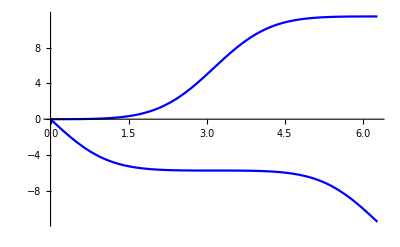

```mathematica
Plot[{A1[0],A1[Pi]}/.{bJ->1,Qx0->0,bmu->1},{theta1,0,2Pi},PlotStyle->{Red,Blue}]
```

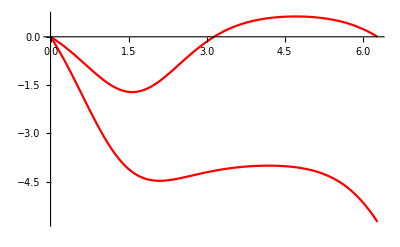

```mathematica
Plot[{A1[Pi/3],A1[Pi/2]}/.{bJ->1,Qx0->0,bmu->1},{theta1,0,2Pi},PlotStyle->{Red}]
```

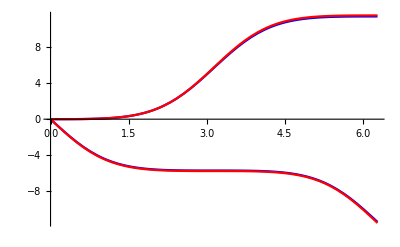

2 | 1 | 1/2 π Cos[2 t1]
4 | 2 | 1/2 π Cos[2 t1]
6 | 3 | 15/32 π Cos[2 t1]
8 | 4 | 7/16 π Cos[2 t1]
10 | 5 | 105/256 π Cos[2 t1]
12 | 6 | 99/256 π Cos[2 t1]
14 | 7 | (3003 π Cos[2 t1])/8192
16 | 8 | (715 π Cos[2 t1])/2048
18 | 9 | (21879 π Cos[2 t1])/65536
20 | 10 | (20995 π Cos[2 t1])/65536

```mathematica
Show[%153,%157]
```